```mathematica
NSolve[Cos[Sqrt[x]] + Sinc[Sqrt[x]]/4==1 && x>0 && x<100Pi,x]
```

{{x→0.479845},{x→39.4784},{x→40.4717},{x→157.914},{x→158.912}}

```mathematica
NSolve[Cos[Sqrt[x]] + Sinc[Sqrt[x]]/4==-1 && x>0 && x<100Pi,x]
```

{{x→9.8696},{x→10.8447},{x→88.8264},{x→89.8234},{x→246.74},{x→247.739}}

```mathematica
10.8447-9.8696
```

0.9751

```mathematica
89.8234-88.8264
```

0.997

```mathematica
40.4717-39.4784
```

0.9933

```mathematica
f[x_] := ArcCos[Cos[Sqrt[x]] + Sinc[Sqrt[x]]/4]
```

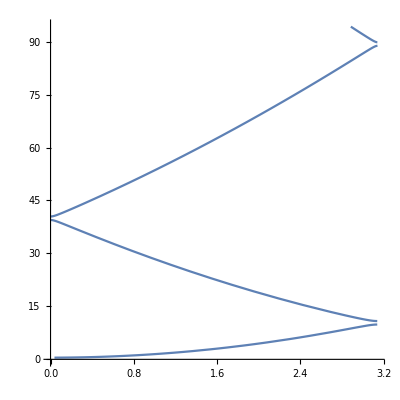

```mathematica
ParametricPlot[{f[x],x}, {x,0,30Pi},AspectRatio->1]
```

```mathematica
f2[x_] := ArcCos[Cos[Sqrt[x]]]
```

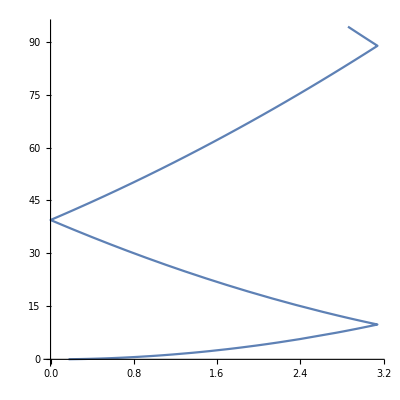

```mathematica
ParametricPlot[{f2[x],x}, {x,0,30Pi},AspectRatio->1]
```

```mathematica
NSolve[Cos[Sqrt[x]]==1 && x>=0 && x<100Pi,x]
```

{{x→0.}}

```mathematica
NSolve[Cos[Sqrt[x]]==-1 && x>=0 && x<100Pi,x]
```

{}

```mathematica
Pi^2
```

π^2

```mathematica
N[Pi^2]
```

9.8696

```mathematica
N[4 Pi^2]
```

39.4784

```mathematica
N[9 Pi^2]
```

88.8264

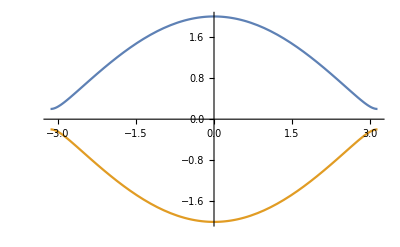

```mathematica
Plot[{Sqrt[0.04 + 4 (Cos[x/2])^2],-Sqrt[0.04 + 4 (Cos[x/2])^2]}, {x,-Pi, Pi}]
```

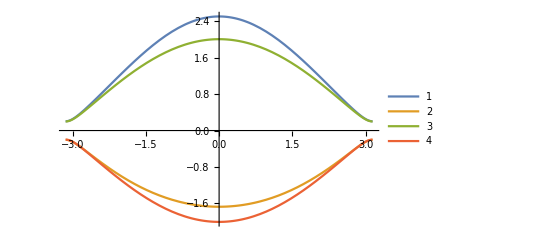

```mathematica
Plot[{(0.4 (Cos[x/2])^2 + Sqrt[0.16 (Cos[x/2])^4 + (4  (Cos[x/2])^2 + 0.04)(1-0.04)])/(1-0.04), (0.4 (Cos[x/2])^2 - Sqrt[0.16 (Cos[x/2])^4 + (4  (Cos[x/2])^2 + 0.04)(1-0.04)])/(1-0.04),Sqrt[0.04 + 4 (Cos[x/2])^2],-Sqrt[0.04 + 4 (Cos[x/2])^2]}, {x,-Pi, Pi},PlotLegends->Automatic]
```

```mathematica
Plot[(0.2 Cos[x] - Sqrt[0.04 (Cos[x])^2 - (4  (Cos[x])^2 + 0.04)(1-0.04)])/(1-0.04), {x,-Pi, Pi}]
```

-Graphics-

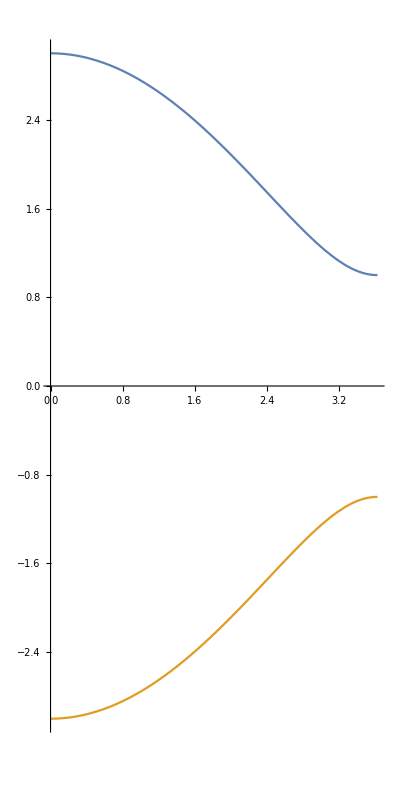

```mathematica
Plot[{Sqrt[1+4 (Cos[Sqrt[3]x/4])^2 + 4 Cos[Sqrt[3] x/4] Cos[Sqrt[3] x/4]],-Sqrt[1+4 (Cos[Sqrt[3]x/4])^2 + 4 Cos[Sqrt[3] x/4] Cos[Sqrt[3] x/4]]},{x,0,2 Pi/ Sqrt[3]},AspectRatio->2]
```

```mathematica
Sqrt[1+4 (Cos[Sqrt[3]x/4])^2 + 4 Cos[Sqrt[3] x/4] Cos[Sqrt[3] x/4]], x= 2Pi/Sqrt[3]
```

```mathematica
ff[x_]:=Sqrt[1+4 (Cos[Sqrt[3]x/4])^2 + 4 Cos[Sqrt[3] x/4] Cos[Sqrt[3] x/4]]
```

```mathematica
ff[2Pi/Sqrt[3]]
```

1

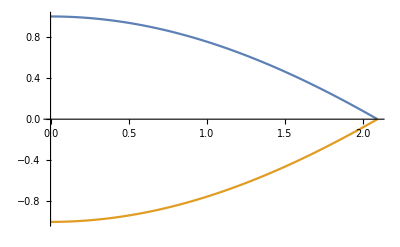

```mathematica
Plot[{Sqrt[1+4 (Cos[Pi/2+ x/4])^2 + 4 Cos[Pi/2+ x/4] Cos[Pi/2 - 3 x/4]],-Sqrt[1+4 (Cos[Pi/2+ x/4])^2 + 4 Cos[Pi/2+ x/4] Cos[Pi/2 - 3 x/4]]},{x,0,2 Pi/ 3}]
```

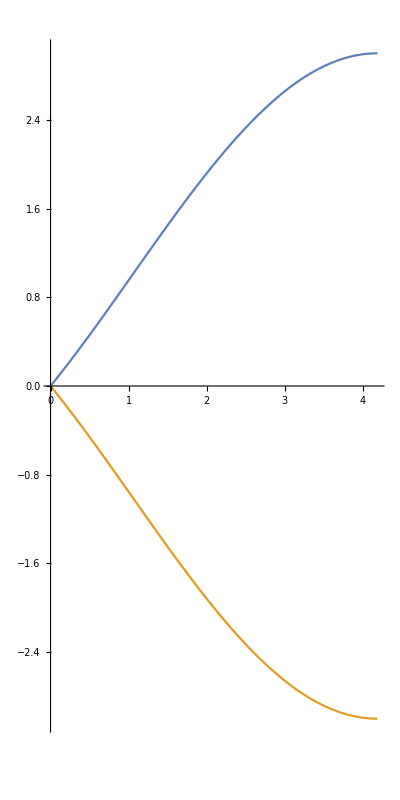

```mathematica
Plot[{Sqrt[1+4 (Cos[Pi/2+ Pi/6-x/2])^2 + 4 Cos[Pi/2+ Pi/6-x/2]],-Sqrt[1+4 (Cos[Pi/2+ Pi/6-x/2])^2 + 4 Cos[Pi/2+ Pi/6-x/2]]},{x,0,4 Pi/ 3},AspectRatio->2]
```

```mathematica
3*3
```

9

```mathematica
3*Sqrt[3]/2 * 2.46 * 10^(-8) / ( 6.582 * 10^(-16))
```

```mathematica
9.710221026935823*^7/29979245800
```

0.00323898

```mathematica
Eigenvalues[{{1/2 ((kx+2)^2+(ky+2)^2+(kz+2)^2),0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1.626346e-01,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00},{0.000000e+00,1/2 ((kx+2)^2+(ky+2)^2+(kz+1)^2),0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00},{0.000000e+00,0.000000e+00,1/2 ((kx+2)^2+(ky+2)^2+(kz+0)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00},{-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+2)^2+(ky+2)^2+(kz+-1)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00},{-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+2)^2+(ky+2)^2+(kz+-2)^2),-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00},{0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1/2 ((kx+2)^2+(ky+1)^2+(kz+2)^2),0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1.626346e-01,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00},{0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+2)^2+(ky+1)^2+(kz+1)^2),0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00},{-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+2)^2+(ky+1)^2+(kz+0)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00},{-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+2)^2+(ky+1)^2+(kz+-1)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00},{-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+2)^2+(ky+1)^2+(kz+-2)^2),-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00},{0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1/2 ((kx+2)^2+(ky+0)^2+(kz+2)^2),0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1.626346e-01,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00},{-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+2)^2+(ky+0)^2+(kz+1)^2),0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00},{-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+2)^2+(ky+0)^2+(kz+0)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00},{-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+2)^2+(ky+0)^2+(kz+-1)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00},{-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+2)^2+(ky+0)^2+(kz+-2)^2),-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00},{-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1/2 ((kx+2)^2+(ky+-1)^2+(kz+2)^2),0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1.626346e-01,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00},{-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+2)^2+(ky+-1)^2+(kz+1)^2),0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00},{-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+2)^2+(ky+-1)^2+(kz+0)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00},{-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+2)^2+(ky+-1)^2+(kz+-1)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00},{0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+2)^2+(ky+-1)^2+(kz+-2)^2),-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00},{-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1/2 ((kx+2)^2+(ky+-2)^2+(kz+2)^2),0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00},{-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+2)^2+(ky+-2)^2+(kz+1)^2),0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00},{-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+2)^2+(ky+-2)^2+(kz+0)^2),0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00},{0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+2)^2+(ky+-2)^2+(kz+-1)^2),0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00},{0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+2)^2+(ky+-2)^2+(kz+-2)^2),0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00},{0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1/2 ((kx+1)^2+(ky+2)^2+(kz+2)^2),0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1.626346e-01,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00},{0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1/2 ((kx+1)^2+(ky+2)^2+(kz+1)^2),0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00},{-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+1)^2+(ky+2)^2+(kz+0)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00},{-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+1)^2+(ky+2)^2+(kz+-1)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00},{-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+1)^2+(ky+2)^2+(kz+-2)^2),-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00},{0.000000e+00,-1.626346e-01,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1/2 ((kx+1)^2+(ky+1)^2+(kz+2)^2),0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1.626346e-01,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00},{1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+1)^2+(ky+1)^2+(kz+1)^2),0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00},{-0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+1)^2+(ky+1)^2+(kz+0)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00},{-4.242641e-02,-0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+1)^2+(ky+1)^2+(kz+-1)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00},{-0.000000e+00,-4.242641e-02,-0.000000e+00,1.626346e-01,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+1)^2+(ky+1)^2+(kz+-2)^2),-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00},{-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1/2 ((kx+1)^2+(ky+0)^2+(kz+2)^2),0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1.626346e-01,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00},{-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+1)^2+(ky+0)^2+(kz+1)^2),0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00},{-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+1)^2+(ky+0)^2+(kz+0)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00},{-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+1)^2+(ky+0)^2+(kz+-1)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00},{0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,1.626346e-01,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+1)^2+(ky+0)^2+(kz+-2)^2),-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00},{-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1/2 ((kx+1)^2+(ky+-1)^2+(kz+2)^2),0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1.626346e-01,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00},{-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+1)^2+(ky+-1)^2+(kz+1)^2),0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00},{-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+1)^2+(ky+-1)^2+(kz+0)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00},{0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+1)^2+(ky+-1)^2+(kz+-1)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02},{0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,1.626346e-01,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+1)^2+(ky+-1)^2+(kz+-2)^2),-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00},{-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1/2 ((kx+1)^2+(ky+-2)^2+(kz+2)^2),0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00},{-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+1)^2+(ky+-2)^2+(kz+1)^2),0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00},{0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+1)^2+(ky+-2)^2+(kz+0)^2),0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00},{0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+1)^2+(ky+-2)^2+(kz+-1)^2),0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00},{0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,1.626346e-01,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+1)^2+(ky+-2)^2+(kz+-2)^2),0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00},{0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1/2 ((kx+0)^2+(ky+2)^2+(kz+2)^2),0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1.626346e-01,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00},{-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1/2 ((kx+0)^2+(ky+2)^2+(kz+1)^2),0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00},{-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+0)^2+(ky+2)^2+(kz+0)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00},{-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+0)^2+(ky+2)^2+(kz+-1)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00},{-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+0)^2+(ky+2)^2+(kz+-2)^2),-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00},{-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1/2 ((kx+0)^2+(ky+1)^2+(kz+2)^2),0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1.626346e-01,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00},{-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+0)^2+(ky+1)^2+(kz+1)^2),0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00},{-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+0)^2+(ky+1)^2+(kz+0)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00},{-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+0)^2+(ky+1)^2+(kz+-1)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00},{0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,1.626346e-01,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+0)^2+(ky+1)^2+(kz+-2)^2),-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00},{-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1/2 ((kx+0)^2+(ky+0)^2+(kz+2)^2),0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1.626346e-01,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00},{-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+0)^2+(ky+0)^2+(kz+1)^2),0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,0.000000e+00},{-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+0)^2+(ky+0)^2+(kz+0)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00},{0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+0)^2+(ky+0)^2+(kz+-1)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00},{0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,1.626346e-01,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+0)^2+(ky+0)^2+(kz+-2)^2),-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02},{-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1/2 ((kx+0)^2+(ky+-1)^2+(kz+2)^2),0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1.626346e-01,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00},{-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+0)^2+(ky+-1)^2+(kz+1)^2),0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00},{0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+0)^2+(ky+-1)^2+(kz+0)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00},{0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+0)^2+(ky+-1)^2+(kz+-1)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00},{0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,1.626346e-01,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+0)^2+(ky+-1)^2+(kz+-2)^2),-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00},{-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1/2 ((kx+0)^2+(ky+-2)^2+(kz+2)^2),0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00},{0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+0)^2+(ky+-2)^2+(kz+1)^2),0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00},{0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+0)^2+(ky+-2)^2+(kz+0)^2),0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02},{0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+0)^2+(ky+-2)^2+(kz+-1)^2),0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00},{0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,1.626346e-01,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+0)^2+(ky+-2)^2+(kz+-2)^2),0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00},{-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1/2 ((kx+-1)^2+(ky+2)^2+(kz+2)^2),0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1.626346e-01,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00},{-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1/2 ((kx+-1)^2+(ky+2)^2+(kz+1)^2),0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00},{-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-1)^2+(ky+2)^2+(kz+0)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00},{-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-1)^2+(ky+2)^2+(kz+-1)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00},{0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-1)^2+(ky+2)^2+(kz+-2)^2),-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00},{-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1/2 ((kx+-1)^2+(ky+1)^2+(kz+2)^2),0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1.626346e-01,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00},{-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-1)^2+(ky+1)^2+(kz+1)^2),0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00},{-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-1)^2+(ky+1)^2+(kz+0)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00},{0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-1)^2+(ky+1)^2+(kz+-1)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02},{0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,1.626346e-01,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-1)^2+(ky+1)^2+(kz+-2)^2),-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00},{-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1/2 ((kx+-1)^2+(ky+0)^2+(kz+2)^2),0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1.626346e-01,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00},{-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-1)^2+(ky+0)^2+(kz+1)^2),0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00},{0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-1)^2+(ky+0)^2+(kz+0)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00},{0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-1)^2+(ky+0)^2+(kz+-1)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00},{0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,1.626346e-01,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-1)^2+(ky+0)^2+(kz+-2)^2),-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00},{-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1/2 ((kx+-1)^2+(ky+-1)^2+(kz+2)^2),0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1.626346e-01,-0.000000e+00,-4.242641e-02,-0.000000e+00},{0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-1)^2+(ky+-1)^2+(kz+1)^2),0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00,-4.242641e-02},{0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-1)^2+(ky+-1)^2+(kz+0)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,-0.000000e+00},{0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-1)^2+(ky+-1)^2+(kz+-1)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01},{0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,1.626346e-01,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-1)^2+(ky+-1)^2+(kz+-2)^2),-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00},{0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1/2 ((kx+-1)^2+(ky+-2)^2+(kz+2)^2),0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00},{0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-1)^2+(ky+-2)^2+(kz+1)^2),0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00},{0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-1)^2+(ky+-2)^2+(kz+0)^2),0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00},{0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-1)^2+(ky+-2)^2+(kz+-1)^2),0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00},{-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,1.626346e-01,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-1)^2+(ky+-2)^2+(kz+-2)^2),0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00},{-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1/2 ((kx+-2)^2+(ky+2)^2+(kz+2)^2),0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00},{-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1/2 ((kx+-2)^2+(ky+2)^2+(kz+1)^2),0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00},{-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-2)^2+(ky+2)^2+(kz+0)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00},{0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-2)^2+(ky+2)^2+(kz+-1)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00},{0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-2)^2+(ky+2)^2+(kz+-2)^2),-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00},{-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1/2 ((kx+-2)^2+(ky+1)^2+(kz+2)^2),0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00},{-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-2)^2+(ky+1)^2+(kz+1)^2),0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00},{0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-2)^2+(ky+1)^2+(kz+0)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00},{0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-2)^2+(ky+1)^2+(kz+-1)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00},{0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,1.626346e-01,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-2)^2+(ky+1)^2+(kz+-2)^2),-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00},{-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1/2 ((kx+-2)^2+(ky+0)^2+(kz+2)^2),0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00},{0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-2)^2+(ky+0)^2+(kz+1)^2),0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00},{0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-2)^2+(ky+0)^2+(kz+0)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02},{0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-2)^2+(ky+0)^2+(kz+-1)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00},{0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,1.626346e-01,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-2)^2+(ky+0)^2+(kz+-2)^2),-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00},{0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1/2 ((kx+-2)^2+(ky+-1)^2+(kz+2)^2),0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00},{0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,-4.242641e-02,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-2)^2+(ky+-1)^2+(kz+1)^2),0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00},{0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-4.242641e-02,-0.000000e+00,-4.242641e-02,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-4.242641e-02,0.000000e+00,4.242641e-02,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000
```

```mathematica
Abort
```

```mathematica
Eigenvalues[{{1/2 ((kx+1)^2+(ky+1)^2+(kz+1)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,1.626346e-01,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00},{0.000000e+00,1/2 ((kx+1)^2+(ky+1)^2+(kz+0)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00},{0.000000e+00,0.000000e+00,1/2 ((kx+1)^2+(ky+1)^2+(kz+-1)^2),0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02},{0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+1)^2+(ky+0)^2+(kz+1)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,1.626346e-01,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00},{0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+1)^2+(ky+0)^2+(kz+0)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00},{-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+1)^2+(ky+0)^2+(kz+-1)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00},{0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+1)^2+(ky+-1)^2+(kz+1)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02},{-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+1)^2+(ky+-1)^2+(kz+0)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00},{-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+1)^2+(ky+-1)^2+(kz+-1)^2),-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00},{0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1/2 ((kx+0)^2+(ky+1)^2+(kz+1)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,1.626346e-01,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00},{0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+0)^2+(ky+1)^2+(kz+0)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01,0.000000e+00,-0.000000e+00,-0.000000e+00},{-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+0)^2+(ky+1)^2+(kz+-1)^2),0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00},{0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+0)^2+(ky+0)^2+(kz+1)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,1.626346e-01,-0.000000e+00},{1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+0)^2+(ky+0)^2+(kz+0)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,1.626346e-01},{-0.000000e+00,1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+0)^2+(ky+0)^2+(kz+-1)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00},{-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+0)^2+(ky+-1)^2+(kz+1)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00},{-0.000000e+00,-0.000000e+00,0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+0)^2+(ky+-1)^2+(kz+0)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00},{-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+0)^2+(ky+-1)^2+(kz+-1)^2),-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00},{0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1/2 ((kx+-1)^2+(ky+1)^2+(kz+1)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,-1.000000e-02},{-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-1)^2+(ky+1)^2+(kz+0)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00},{-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-1)^2+(ky+1)^2+(kz+-1)^2),0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00},{-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-1)^2+(ky+0)^2+(kz+1)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00},{-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-1)^2+(ky+0)^2+(kz+0)^2),0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00},{-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-1)^2+(ky+0)^2+(kz+-1)^2),0.000000e+00,0.000000e+00,0.000000e+00},{-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1.000000e-02,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-1)^2+(ky+-1)^2+(kz+1)^2),0.000000e+00,0.000000e+00},{-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,0.000000e+00,1.626346e-01,0.000000e+00,-1.626346e-01,0.000000e+00,0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-1)^2+(ky+-1)^2+(kz+0)^2),0.000000e+00},{-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,-0.000000e+00,-0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,-0.000000e+00,1.626346e-01,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,-1.000000e-02,-0.000000e+00,0.000000e+00,-0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,0.000000e+00,1/2 ((kx+-1)^2+(ky+-1)^2+(kz+-1)^2)}}]
```

{Root[0.341712+0.523051 e-1.51989 e^2-2.51864 e^3-5.42087 e^4-0.864767 e^5+1. e^6+3.17386×10^-17 e kx-3.17386×10^-17 e^2 kx-6.34773×10^-17 e^3 kx-7.93466×10^-18 e^4 kx+0.214407 kx^2+0.435875 e kx^2+1.80669 e^2 kx^2+1.38973 e^3 kx^2-0.150557 e^4 kx^2-1.09452 e^5 kx^2+2.3804×10^-17 e kx^3+1.58693×10^-17 e^2 kx^3-3.96733×10^-18 e^3 kx^3-0.0524851 kx^4-0.159821 e kx^4+0.357636 e^2 kx^4+0.454643 e^3 kx^4+0.299492 e^4 kx^4+7.93466×10^-18 e kx^5+3.96733×10^-18 e^2 kx^5-0.0591853 kx^6-0.0799105 e kx^6-0.0704074 e^2 kx^6+0.0236295 e^3 kx^6-0.00767734 kx^8-0.00726459 e kx^8-0.0129314 e^2 kx^8+0.000837528 kx^10+0.000139588 kx^12-1.26955×10^-16 e^2 ky+2.53909×10^-16 e^3 ky+1.26955×10^-16 e^4 ky+0.3487 e kx ky-0.464934 e^2 kx ky+0.116233 e^3 kx ky-2.3804×10^-17 e kx^2 ky-0.116233 e kx^3 ky-7.93466×10^-18 e^2 kx^4 ky-0.0290584 e kx^5 ky+1.98367×10^-18 e^2 kx^6 ky+0.415414 ky^2+0.610226 e ky^2+1.38015 e^2 ky^2+1.29521 e^3 ky^2-0.141624 e^4 ky^2-1.09452 e^5 ky^2+1.58693×10^-17 e^2 kx ky^2-0.0647689 kx^2 ky^2-0.116233 e kx^2 ky^2+0.772131 e^2 kx^2 ky^2+0.814769 e^3 kx^2 ky^2+0.598985 e^4 kx^2 ky^2+7.93466×10^-18 e kx^3 ky^2+4.95916×10^-18 e^2 kx^3 ky^2-0.142938 kx^4 ky^2-0.210673 e kx^4 ky^2-0.163963 e^2 kx^4 ky^2+0.0708884 e^3 kx^4 ky^2-0.028476 kx^6 ky^2-0.0290584 e kx^6 ky^2-0.0517258 e^2 kx^6 ky^2+0.00362929 kx^8 ky^2+0.000837528 kx^10 ky^2-2.77713×10^-17 e^2 kx^2 ky^3-0.0581167 e kx^3 ky^3-3.96733×10^-18 e kx^4 ky^3+1.98367×10^-18 e^2 kx^4 ky^3+0.0435515 ky^4+0.0435875 e ky^4+0.432362 e^2 ky^4+0.360125 e^3 ky^4+0.299492 e^4 ky^4+1.98367×10^-18 e kx ky^4+3.96733×10^-18 e^2 kx ky^4-0.130654 kx^2 ky^4-0.181615 e kx^2 ky^4-0.116704 e^2 kx^2 ky^4+0.0708884 e^3 kx^2 ky^4-0.0415972 kx^4 ky^4-0.0435875 e kx^4 ky^4-0.0775887 e^2 kx^4 ky^4+0.00614187 kx^6 ky^4+0.00209382 kx^8 ky^4+3.96733×10^-18 e ky^5-9.91833×10^-18 e^2 ky^5-0.0290584 e kx ky^5-1.98367×10^-18 e kx^2 ky^5+5.951×10^-18 e^2 kx^2 ky^5-0.037968 ky^6-0.0508521 e ky^6-0.0231484 e^2 ky^6+0.0236295 e^3 ky^6-0.028476 kx^2 ky^6-0.0290584 e kx^2 ky^6-0.0517258 e^2 kx^2 ky^6+0.00502517 kx^4 ky^6+0.00279176 kx^6 ky^6+1.98367×10^-18 e^2 ky^7-0.00767734 ky^8-0.00726459 e ky^8-0.0129314 e^2 ky^8+0.00195423 kx^2 ky^8+0.00209382 kx^4 ky^8+0.000279176 ky^10+0.000837528 kx^2 ky^10+0.000139588 ky^12-1.26955×10^-16 e^2 kz+2.53909×10^-16 e^3 kz+1.26955×10^-16 e^4 kz+0.3487 e kx kz-0.464934 e^2 kx kz+0.116233 e^3 kx kz-2.3804×10^-17 e kx^2 kz-0.116233 e kx^3 kz-7.93466×10^-18 e^2 kx^4 kz-0.0290584 e kx^5 kz+1.98367×10^-18 e^2 kx^6 kz+0.241497 e ky kz+1.01798 e^2 ky kz+9.52159×10^-17 e^3 ky kz+1.58693×10^-17 e kx ky kz-3.17386×10^-17 e^2 kx ky kz+0.406817 e kx^2 ky kz+0.261838 e^2 kx^2 ky kz+0.0223822 e kx^4 ky kz-0.232467 e kx ky^2 kz-3.17386×10^-17 e^2 kx^2 ky^2 kz-0.0581167 e kx^3 ky^2 kz+1.98367×10^-18 e^2 kx^4 ky^2 kz+0.263879 e ky^3 kz+0.261838 e^2 ky^3 kz+0.0447644 e kx^2 ky^3 kz-7.93466×10^-18 e^2 ky^4 kz-0.0290584 e kx ky^4 kz+1.98367×10^-18 e^2 kx^2 ky^4 kz+0.0223822 e ky^5 kz+1.98367×10^-18 e^2 ky^6 kz+0.415414 kz^2+0.610226 e kz^2+1.38015 e^2 kz^2+1.29521 e^3 kz^2-0.141624 e^4 kz^2-1.09452 e^5 kz^2+1.58693×10^-17 e^2 kx kz^2-0.0647689 kx^2 kz^2-0.116233 e kx^2 kz^2+0.772131 e^2 kx^2 kz^2+0.814769 e^3 kx^2 kz^2+0.598985 e^4 kx^2 kz^2+7.93466×10^-18 e kx^3 kz^2+4.95916×10^-18 e^2 kx^3 kz^2-0.142938 kx^4 kz^2-0.210673 e kx^4 kz^2-0.163963 e^2 kx^4 kz^2+0.0708884 e^3 kx^4 kz^2-0.028476 kx^6 kz^2-0.0290584 e kx^6 kz^2-0.0517258 e^2 kx^6 kz^2+0.00362929 kx^8 kz^2+0.000837528 kx^10 kz^2-0.232467 e kx ky kz^2-3.17386×10^-17 e^2 kx^2 ky kz^2-0.0581167 e kx^3 ky kz^2-1.98367×10^-18 e kx^4 ky kz^2+5.951×10^-18 e^2 kx^4 ky kz^2+0.0781693 ky^2 kz^2+0.0871751 e ky^2 kz^2+0.864725 e^2 ky^2 kz^2+0.720251 e^3 ky^2 kz^2+0.598985 e^4 ky^2 kz^2+3.96733×10^-18 e kx ky^2 kz^2+7.93466×10^-18 e^2 kx ky^2 kz^2-0.243442 kx^2 ky^2 kz^2-0.36323 e kx^2 ky^2 kz^2-0.233409 e^2 kx^2 ky^2 kz^2+0.141777 e^3 kx^2 ky^2 kz^2-0.0921281 kx^4 ky^2 kz^2-0.0871751 e kx^4 ky^2 kz^2-0.155177 e^2 kx^4 ky^2 kz^2+0.0122837 kx^6 ky^2 kz^2+0.00418764 kx^8 ky^2 kz^2-1.58693×10^-17 e^2 ky^3 kz^2-0.0581167 e kx ky^3 kz^2-7.93466×10^-18 e kx^2 ky^3 kz^2+3.96733×10^-18 e^2 kx^2 ky^3 kz^2-0.131771 ky^4 kz^2-0.152556 e ky^4 kz^2-0.0694453 e^2 ky^4 kz^2+0.0708884 e^3 ky^4 kz^2-0.103295 kx^2 ky^4 kz^2-0.0871751 e kx^2 ky^4 kz^2-0.155177 e^2 kx^2 ky^4 kz^2+0.0150755 kx^4 ky^4 kz^2+0.00837528 kx^6 ky^4 kz^2-1.98367×10^-18 e ky^5 kz^2+5.951×10^-18 e^2 ky^5 kz^2-0.039643 ky^6 kz^2-0.0290584 e ky^6 kz^2-0.0517258 e^2 ky^6 kz^2+0.00781693 kx^2 ky^6 kz^2+0.00837528 kx^4 ky^6 kz^2+0.00139588 ky^8 kz^2+0.00418764 kx^2 ky^8 kz^2+0.000837528 ky^10 kz^2-2.77713×10^-17 e^2 kx^2 kz^3-0.0581167 e kx^3 kz^3-3.96733×10^-18 e kx^4 kz^3+1.98367×10^-18 e^2 kx^4 kz^3+0.263879 e ky kz^3+0.261838 e^2 ky kz^3+0.0447644 e kx^2 ky kz^3-1.58693×10^-17 e^2 ky^2 kz^3-0.0581167 e kx ky^2 kz^3-7.93466×10^-18 e kx^2 ky^2 kz^3+3.96733×10^-18 e^2 kx^2 ky^2 kz^3+0.0447644 e ky^3 kz^3-3.96733×10^-18 e ky^4 kz^3+1.98367×10^-18 e^2 ky^4 kz^3+0.0435515 kz^4+0.0435875 e kz^4+0.432362 e^2 kz^4+0.360125 e^3 kz^4+0.299492 e^4 kz^4+1.98367×10^-18 e kx kz^4+3.96733×10^-18 e^2 kx kz^4-0.130654 kx^2 kz^4-0.181615 e kx^2 kz^4-0.116704 e^2 kx^2 kz^4+0.0708884 e^3 kx^2 kz^4-0.0415972 kx^4 kz^4-0.0435875 e kx^4 kz^4-0.0775887 e^2 kx^4 kz^4+0.00614187 kx^6 kz^4+0.00209382 kx^8 kz^4-7.93466×10^-18 e^2 ky kz^4-0.0290584 e kx ky kz^4-3.96733×10^-18 e kx^2 ky kz^4+1.98367×10^-18 e^2 kx^2 ky kz^4-0.131771 ky^2 kz^4-0.152556 e ky^2 kz^4-0.0694453 e^2 ky^2 kz^4+0.0708884 e^3 ky^2 kz^4-0.103295 kx^2 ky^2 kz^4-0.0871751 e kx^2 ky^2 kz^4-0.155177 e^2 kx^2 ky^2 kz^4+0.0150755 kx^4 ky^2 kz^4+0.00837528 kx^6 ky^2 kz^4-3.96733×10^-18 e ky^3 kz^4+1.98367×10^-18 e^2 ky^3 kz^4-0.0639313 ky^4 kz^4-0.0435875 e ky^4 kz^4-0.0775887 e^2 ky^4 kz^4+0.0117254 kx^2 ky^4 kz^4+0.0125629 kx^4 ky^4 kz^4+0.00279176 ky^6 kz^4+0.00837528 kx^2 ky^6 kz^4+0.00209382 ky^8 kz^4+3.96733×10^-18 e kz^5-9.91833×10^-18 e^2 kz^5-0.0290584 e kx kz^5-1.98367×10^-18 e kx^2 kz^5+5.951×10^-18 e^2 kx^2 kz^5+0.0223822 e ky kz^5-1.98367×10^-18 e ky^2 kz^5+5.951×10^-18 e^2 ky^2 kz^5-0.037968 kz^6-0.0508521 e kz^6-0.0231484 e^2 kz^6+0.0236295 e^3 kz^6-0.028476 kx^2 kz^6-0.0290584 e kx^2 kz^6-0.0517258 e^2 kx^2 kz^6+0.00502517 kx^4 kz^6+0.00279176 kx^6 kz^6+1.98367×10^-18 e^2 ky kz^6-0.039643 ky^2 kz^6-0.0290584 e ky^2 kz^6-0.0517258 e^2 ky^2 kz^6+0.00781693 kx^2 ky^2 kz^6+0.00837528 kx^4 ky^2 kz^6+0.00279176 ky^4 kz^6+0.00837528 kx^2 ky^4 kz^6+0.00279176 ky^6 kz^6+1.98367×10^-18 e^2 kz^7-0.00767734 kz^8-0.00726459 e kz^8-0.0129314 e^2 kz^8+0.00195423 kx^2 kz^8+0.00209382 kx^4 kz^8+0.00139588 ky^2 kz^8+0.00418764 kx^2 ky^2 kz^8+0.00209382 ky^4 kz^8+0.000279176 kz^10+0.000837528 kx^2 kz^10+0.000837528 ky^2 kz^10+0.000139588 kz^12+(-0.58962-0.871751 e-3.43471 e^2-2.77946 e^3+0.283247 e^4+2.18904 e^5-4.7608×10^-17 e kx-3.17386×10^-17 e^2 kx+7.93466×10^-18 e^3 kx+0.317144 kx^2+0.639284 e kx^2-1.39481 e^2 kx^2-1.81857 e^3 kx^2-1.19797 e^4 kx^2-3.17386×10^-17 e kx^3-1.58693×10^-17 e^2 kx^3+0.364046 kx^4+0.479463 e kx^4+0.431378 e^2 kx^4-0.141777 e^3 kx^4+0.0524851 kx^6+0.0581167 e kx^6+0.103452 e^2 kx^6-0.00949199 kx^8-0.00167506 kx^10-1.58693×10^-17 e ky+0.232467 e kx ky+6.34773×10^-17 e^2 kx^2 ky+0.116233 e kx^3 ky+3.96733×10^-18 e kx^4 ky-1.1902×10^-17 e^2 kx^4 ky+0.129538 ky^2+0.232467 e ky^2-1.54426 e^2 ky^2-1.62954 e^3 ky^2-1.19797 e^4 ky^2-1.58693×10^-17 e kx ky^2-9.91833×10^-18 e^2 kx ky^2+0.625354 kx^2 ky^2+0.842693 e kx^2 ky^2+0.67372 e^2 kx^2 ky^2-0.283554 e^3 kx^2 ky^2+0.152989 kx^4 ky^2+0.17435 e kx^4 ky^2+0.310355 e^2 kx^4 ky^2-0.0335011 kx^6 ky^2-0.00837528 kx^8 ky^2+5.55426×10^-17 e^2 ky^3+0.116233 e kx ky^3+1.58693×10^-17 e kx^2 ky^3-7.93466×10^-18 e^2 kx^2 ky^3+0.28811 ky^4+0.36323 e ky^4+0.242342 e^2 ky^4-0.141777 e^3 ky^4+0.157455 kx^2 ky^4+0.17435 e kx^2 ky^4+0.310355 e^2 kx^2 ky^4-0.0435515 kx^4 ky^4-0.0167506 kx^6 ky^4+3.96733×10^-18 e ky^5-1.1902×10^-17 e^2 ky^5+0.0569519 ky^6+0.0581167 e ky^6+0.103452 e^2 ky^6-0.0245675 kx^2 ky^6-0.0167506 kx^4 ky^6-0.00502517 ky^8-0.00837528 kx^2 ky^8-0.00167506 ky^10-1.58693×10^-17 e kz+0.232467 e kx kz+6.34773×10^-17 e^2 kx^2 kz+0.116233 e kx^3 kz+7.93466×10^-18 e kx^4 kz-3.96733×10^-18 e^2 kx^4 kz-0.527758 e ky kz-0.523676 e^2 ky kz-0.0895288 e kx^2 ky kz+6.34773×10^-17 e^2 ky^2 kz+0.116233 e kx ky^2 kz+1.58693×10^-17 e kx^2 ky^2 kz-7.93466×10^-18 e^2 kx^2 ky^2 kz-0.0895288 e ky^3 kz+7.93466×10^-18 e ky^4 kz-3.96733×10^-18 e^2 ky^4 kz+0.129538 kz^2+0.232467 e kz^2-1.54426 e^2 kz^2-1.62954 e^3 kz^2-1.19797 e^4 kz^2-1.58693×10^-17 e kx kz^2-9.91833×10^-18 e^2 kx kz^2+0.625354 kx^2 kz^2+0.842693 e kx^2 kz^2+0.67372 e^2 kx^2 kz^2-0.283554 e^3 kx^2 kz^2+0.152989 kx^4 kz^2+0.17435 e kx^4 kz^2+0.310355 e^2 kx^4 kz^2-0.0335011 kx^6 kz^2-0.00837528 kx^8 kz^2+3.17386×10^-17 e^2 ky kz^2+0.116233 e kx ky kz^2+1.58693×10^-17 e kx^2 ky kz^2-7.93466×10^-18 e^2 kx^2 ky kz^2+0.611954 ky^2 kz^2+0.726459 e ky^2 kz^2+0.484684 e^2 ky^2 kz^2-0.283554 e^3 ky^2 kz^2+0.350645 kx^2 ky^2 kz^2+0.3487 e kx^2 ky^2 kz^2+0.620709 e^2 kx^2 ky^2 kz^2-0.0871029 kx^4 ky^2 kz^2-0.0335011 kx^6 ky^2 kz^2+1.58693×10^-17 e ky^3 kz^2-7.93466×10^-18 e^2 ky^3 kz^2+0.20659 ky^4 kz^2+0.17435 e ky^4 kz^2+0.310355 e^2 ky^4 kz^2-0.0737025 kx^2 ky^4 kz^2-0.0502517 kx^4 ky^4 kz^2-0.0201007 ky^6 kz^2-0.0335011 kx^2 ky^6 kz^2-0.00837528 ky^8 kz^2-1.58693×10^-17 e kz^3+5.55426×10^-17 e^2 kz^3+0.116233 e kx kz^3+1.58693×10^-17 e kx^2 kz^3-7.93466×10^-18 e^2 kx^2 kz^3-0.0895288 e ky kz^3+1.58693×10^-17 e ky^2 kz^3-7.93466×10^-18 e^2 ky^2 kz^3+0.28811 kz^4+0.36323 e kz^4+0.242342 e^2 kz^4-0.141777 e^3 kz^4+0.157455 kx^2 kz^4+0.17435 e kx^2 kz^4+0.310355 e^2 kx^2 kz^4-0.0435515 kx^4 kz^4-0.0167506 kx^6 kz^4-3.96733×10^-18 e^2 ky kz^4+0.20659 ky^2 kz^4+0.17435 e ky^2 kz^4+0.310355 e^2 ky^2 kz^4-0.0737025 kx^2 ky^2 kz^4-0.0502517 kx^4 ky^2 kz^4-0.030151 ky^4 kz^4-0.0502517 kx^2 ky^4 kz^4-0.0167506 ky^6 kz^4+3.96733×10^-18 e kz^5-1.1902×10^-17 e^2 kz^5+0.0569519 kz^6+0.0581167 e kz^6+0.103452 e^2 kz^6-0.0245675 kx^2 kz^6-0.0167506 kx^4 kz^6-0.0201007 ky^2 kz^6-0.0335011 kx^2 ky^2 kz^6-0.0167506 ky^4 kz^6-0.00502517 kz^8-0.00837528 kx^2 kz^8-0.00837528 ky^2 kz^8-0.00167506 kz^10) #1+(-0.424348-0.639284 e+1.35907 e^2+1.81857 e^3+1.19797 e^4+3.17386×10^-17 e kx+1.58693×10^-17 e^2 kx-0.745959 kx^2-0.958926 e kx^2-0.880623 e^2 kx^2+0.283554 e^3 kx^2-0.130654 kx^4-0.17435 e kx^4-0.310355 e^2 kx^4+0.0424348 kx^6+0.00837528 kx^8-3.17386×10^-17 e^2 ky-0.116233 e kx ky-1.58693×10^-17 e kx^2 ky+7.93466×10^-18 e^2 kx^2 ky-0.678956 ky^2-0.842693 e ky^2-0.691588 e^2 ky^2+0.283554 e^3 ky^2-0.270242 kx^2 ky^2-0.3487 e kx^2 ky^2-0.620709 e^2 kx^2 ky^2+0.113904 kx^4 ky^2+0.0335011 kx^6 ky^2-1.58693×10^-17 e ky^3+7.93466×10^-18 e^2 ky^3-0.148522 ky^4-0.17435 e ky^4-0.310355 e^2 ky^4+0.100503 kx^2 ky^4+0.0502517 kx^4 ky^4+0.0290343 ky^6+0.0335011 kx^2 ky^6+0.00837528 ky^8+1.58693×10^-17 e kz-6.34773×10^-17 e^2 kz-0.116233 e kx kz-7.93466×10^-18 e kx^2 kz+2.3804×10^-17 e^2 kx^2 kz+0.0895288 e ky kz-7.93466×10^-18 e ky^2 kz+2.3804×10^-17 e^2 ky^2 kz-0.678956 kz^2-0.842693 e kz^2-0.691588 e^2 kz^2+0.283554 e^3 kz^2-0.270242 kx^2 kz^2-0.3487 e kx^2 kz^2-0.620709 e^2 kx^2 kz^2+0.113904 kx^4 kz^2+0.0335011 kx^6 kz^2+7.93466×10^-18 e^2 ky kz^2-0.332778 ky^2 kz^2-0.3487 e ky^2 kz^2-0.620709 e^2 ky^2 kz^2+0.201007 kx^2 ky^2 kz^2+0.100503 kx^4 ky^2 kz^2+0.0871029 ky^4 kz^2+0.100503 kx^2 ky^4 kz^2+0.0335011 ky^6 kz^2-1.58693×10^-17 e kz^3+7.93466×10^-18 e^2 kz^3-0.148522 kz^4-0.17435 e kz^4-0.310355 e^2 kz^4+0.100503 kx^2 kz^4+0.0502517 kx^4 kz^4+0.0871029 ky^2 kz^4+0.100503 kx^2 ky^2 kz^4+0.0502517 ky^4 kz^4+0.0290343 kz^6+0.0335011 kx^2 kz^6+0.0335011 ky^2 kz^6+0.00837528 kz^8) #1^2+(0.509217+0.639284 e+0.598994 e^2-0.189036 e^3+0.138471 kx^2+0.232467 e kx^2+0.413806 e^2 kx^2-0.0938032 kx^4-0.0223341 kx^6-1.58693×10^-17 e^2 ky+0.156339 ky^2+0.232467 e ky^2+0.413806 e^2 ky^2-0.169739 kx^2 ky^2-0.0670023 kx^4 ky^2-0.0759359 ky^4-0.0670023 kx^2 ky^4-0.0223341 ky^6-1.58693×10^-17 e^2 kz+0.156339 kz^2+0.232467 e kz^2+0.413806 e^2 kz^2-0.169739 kx^2 kz^2-0.0670023 kx^4 kz^2-0.151872 ky^2 kz^2-0.134005 kx^2 ky^2 kz^2-0.0670023 ky^4 kz^2-0.0759359 kz^4-0.0670023 kx^2 kz^4-0.0670023 ky^2 kz^4-0.0223341 kz^6) #1^3+(-0.0513684-0.116233 e-0.206903 e^2+0.102737 kx^2+0.0335011 kx^4+0.0938032 ky^2+0.0670023 kx^2 ky^2+0.0335011 ky^4+0.0938032 kz^2+0.0670023 kx^2 kz^2+0.0670023 ky^2 kz^2+0.0335011 kz^4) #1^4+(-0.0446682-0.0268009 kx^2-0.0268009 ky^2-0.0268009 kz^2) #1^5+0.00893364 #1^6&,1],Root[0.341712+0.523051 e-1.51989 e^2-2.51864 e^3-5.42087 e^4-0.864767 e^5+1. e^6+3.17386×10^-17 e kx-3.17386×10^-17 e^2 kx-6.34773×10^-17 e^3 kx-7.93466×10^-18 e^4 kx+0.214407 kx^2+0.435875 e kx^2+1.80669 e^2 kx^2+1.38973 e^3 kx^2-0.150557 e^4 kx^2-1.09452 e^5 kx^2+2.3804×10^-17 e kx^3+1.58693×10^-17 e^2 kx^3-3.96733×10^-18 e^3 kx^3-0.0524851 kx^4-0.159821 e kx^4+0.357636 e^2 kx^4+0.454643 e^3 kx^4+0.299492 e^4 kx^4+7.93466×10^-18 e kx^5+3.96733×10^-18 e^2 kx^5-0.0591853 kx^6-0.0799105 e kx^6-0.0704074 e^2 kx^6+0.0236295 e^3 kx^6-0.00767734 kx^8-0.00726459 e kx^8-0.0129314 e^2 kx^8+0.000837528 kx^10+0.000139588 kx^12-1.26955×10^-16 e^2 ky+2.53909×10^-16 e^3 ky+1.26955×10^-16 e^4 ky+0.3487 e kx ky-0.464934 e^2 kx ky+0.116233 e^3 kx ky-2.3804×10^-17 e kx^2 ky-0.116233 e kx^3 ky-7.93466×10^-18 e^2 kx^4 ky-0.0290584 e kx^5 ky+1.98367×10^-18 e^2 kx^6 ky+0.415414 ky^2+0.610226 e ky^2+1.38015 e^2 ky^2+1.29521 e^3 ky^2-0.141624 e^4 ky^2-1.09452 e^5 ky^2+1.58693×10^-17 e^2 kx ky^2-0.0647689 kx^2 ky^2-0.116233 e kx^2 ky^2+0.772131 e^2 kx^2 ky^2+0.814769 e^3 kx^2 ky^2+0.598985 e^4 kx^2 ky^2+7.93466×10^-18 e kx^3 ky^2+4.95916×10^-18 e^2 kx^3 ky^2-0.142938 kx^4 ky^2-0.210673 e kx^4 ky^2-0.163963 e^2 kx^4 ky^2+0.0708884 e^3 kx^4 ky^2-0.028476 kx^6 ky^2-0.0290584 e kx^6 ky^2-0.0517258 e^2 kx^6 ky^2+0.00362929 kx^8 ky^2+0.000837528 kx^10 ky^2-2.77713×10^-17 e^2 kx^2 ky^3-0.0581167 e kx^3 ky^3-3.96733×10^-18 e kx^4 ky^3+1.98367×10^-18 e^2 kx^4 ky^3+0.0435515 ky^4+0.0435875 e ky^4+0.432362 e^2 ky^4+0.360125 e^3 ky^4+0.299492 e^4 ky^4+1.98367×10^-18 e kx ky^4+3.96733×10^-18 e^2 kx ky^4-0.130654 kx^2 ky^4-0.181615 e kx^2 ky^4-0.116704 e^2 kx^2 ky^4+0.0708884 e^3 kx^2 ky^4-0.0415972 kx^4 ky^4-0.0435875 e kx^4 ky^4-0.0775887 e^2 kx^4 ky^4+0.00614187 kx^6 ky^4+0.00209382 kx^8 ky^4+3.96733×10^-18 e ky^5-9.91833×10^-18 e^2 ky^5-0.0290584 e kx ky^5-1.98367×10^-18 e kx^2 ky^5+5.951×10^-18 e^2 kx^2 ky^5-0.037968 ky^6-0.0508521 e ky^6-0.0231484 e^2 ky^6+0.0236295 e^3 ky^6-0.028476 kx^2 ky^6-0.0290584 e kx^2 ky^6-0.0517258 e^2 kx^2 ky^6+0.00502517 kx^4 ky^6+0.00279176 kx^6 ky^6+1.98367×10^-18 e^2 ky^7-0.00767734 ky^8-0.00726459 e ky^8-0.0129314 e^2 ky^8+0.00195423 kx^2 ky^8+0.00209382 kx^4 ky^8+0.000279176 ky^10+0.000837528 kx^2 ky^10+0.000139588 ky^12-1.26955×10^-16 e^2 kz+2.53909×10^-16 e^3 kz+1.26955×10^-16 e^4 kz+0.3487 e kx kz-0.464934 e^2 kx kz+0.116233 e^3 kx kz-2.3804×10^-17 e kx^2 kz-0.116233 e kx^3 kz-7.93466×10^-18 e^2 kx^4 kz-0.0290584 e kx^5 kz+1.98367×10^-18 e^2 kx^6 kz+0.241497 e ky kz+1.01798 e^2 ky kz+9.52159×10^-17 e^3 ky kz+1.58693×10^-17 e kx ky kz-3.17386×10^-17 e^2 kx ky kz+0.406817 e kx^2 ky kz+0.261838 e^2 kx^2 ky kz+0.0223822 e kx^4 ky kz-0.232467 e kx ky^2 kz-3.17386×10^-17 e^2 kx^2 ky^2 kz-0.0581167 e kx^3 ky^2 kz+1.98367×10^-18 e^2 kx^4 ky^2 kz+0.263879 e ky^3 kz+0.261838 e^2 ky^3 kz+0.0447644 e kx^2 ky^3 kz-7.93466×10^-18 e^2 ky^4 kz-0.0290584 e kx ky^4 kz+1.98367×10^-18 e^2 kx^2 ky^4 kz+0.0223822 e ky^5 kz+1.98367×10^-18 e^2 ky^6 kz+0.415414 kz^2+0.610226 e kz^2+1.38015 e^2 kz^2+1.29521 e^3 kz^2-0.141624 e^4 kz^2-1.09452 e^5 kz^2+1.58693×10^-17 e^2 kx kz^2-0.0647689 kx^2 kz^2-0.116233 e kx^2 kz^2+0.772131 e^2 kx^2 kz^2+0.814769 e^3 kx^2 kz^2+0.598985 e^4 kx^2 kz^2+7.93466×10^-18 e kx^3 kz^2+4.95916×10^-18 e^2 kx^3 kz^2-0.142938 kx^4 kz^2-0.210673 e kx^4 kz^2-0.163963 e^2 kx^4 kz^2+0.0708884 e^3 kx^4 kz^2-0.028476 kx^6 kz^2-0.0290584 e kx^6 kz^2-0.0517258 e^2 kx^6 kz^2+0.00362929 kx^8 kz^2+0.000837528 kx^10 kz^2-0.232467 e kx ky kz^2-3.17386×10^-17 e^2 kx^2 ky kz^2-0.0581167 e kx^3 ky kz^2-1.98367×10^-18 e kx^4 ky kz^2+5.951×10^-18 e^2 kx^4 ky kz^2+0.0781693 ky^2 kz^2+0.0871751 e ky^2 kz^2+0.864725 e^2 ky^2 kz^2+0.720251 e^3 ky^2 kz^2+0.598985 e^4 ky^2 kz^2+3.96733×10^-18 e kx ky^2 kz^2+7.93466×10^-18 e^2 kx ky^2 kz^2-0.243442 kx^2 ky^2 kz^2-0.36323 e kx^2 ky^2 kz^2-0.233409 e^2 kx^2 ky^2 kz^2+0.141777 e^3 kx^2 ky^2 kz^2-0.0921281 kx^4 ky^2 kz^2-0.0871751 e kx^4 ky^2 kz^2-0.155177 e^2 kx^4 ky^2 kz^2+0.0122837 kx^6 ky^2 kz^2+0.00418764 kx^8 ky^2 kz^2-1.58693×10^-17 e^2 ky^3 kz^2-0.0581167 e kx ky^3 kz^2-7.93466×10^-18 e kx^2 ky^3 kz^2+3.96733×10^-18 e^2 kx^2 ky^3 kz^2-0.131771 ky^4 kz^2-0.152556 e ky^4 kz^2-0.0694453 e^2 ky^4 kz^2+0.0708884 e^3 ky^4 kz^2-0.103295 kx^2 ky^4 kz^2-0.0871751 e kx^2 ky^4 kz^2-0.155177 e^2 kx^2 ky^4 kz^2+0.0150755 kx^4 ky^4 kz^2+0.00837528 kx^6 ky^4 kz^2-1.98367×10^-18 e ky^5 kz^2+5.951×10^-18 e^2 ky^5 kz^2-0.039643 ky^6 kz^2-0.0290584 e ky^6 kz^2-0.0517258 e^2 ky^6 kz^2+0.00781693 kx^2 ky^6 kz^2+0.00837528 kx^4 ky^6 kz^2+0.00139588 ky^8 kz^2+0.00418764 kx^2 ky^8 kz^2+0.000837528 ky^10 kz^2-2.77713×10^-17 e^2 kx^2 kz^3-0.0581167 e kx^3 kz^3-3.96733×10^-18 e kx^4 kz^3+1.98367×10^-18 e^2 kx^4 kz^3+0.263879 e ky kz^3+0.261838 e^2 ky kz^3+0.0447644 e kx^2 ky kz^3-1.58693×10^-17 e^2 ky^2 kz^3-0.0581167 e kx ky^2 kz^3-7.93466×10^-18 e kx^2 ky^2 kz^3+3.96733×10^-18 e^2 kx^2 ky^2 kz^3+0.0447644 e ky^3 kz^3-3.96733×10^-18 e ky^4 kz^3+1.98367×10^-18 e^2 ky^4 kz^3+0.0435515 kz^4+0.0435875 e kz^4+0.432362 e^2 kz^4+0.360125 e^3 kz^4+0.299492 e^4 kz^4+1.98367×10^-18 e kx kz^4+3.96733×10^-18 e^2 kx kz^4-0.130654 kx^2 kz^4-0.181615 e kx^2 kz^4-0.116704 e^2 kx^2 kz^4+0.0708884 e^3 kx^2 kz^4-0.0415972 kx^4 kz^4-0.0435875 e kx^4 kz^4-0.0775887 e^2 kx^4 kz^4+0.00614187 kx^6 kz^4+0.00209382 kx^8 kz^4-7.93466×10^-18 e^2 ky kz^4-0.0290584 e kx ky kz^4-3.96733×10^-18 e kx^2 ky kz^4+1.98367×10^-18 e^2 kx^2 ky kz^4-0.131771 ky^2 kz^4-0.152556 e ky^2 kz^4-0.0694453 e^2 ky^2 kz^4+0.0708884 e^3 ky^2 kz^4-0.103295 kx^2 ky^2 kz^4-0.0871751 e kx^2 ky^2 kz^4-0.155177 e^2 kx^2 ky^2 kz^4+0.0150755 kx^4 ky^2 kz^4+0.00837528 kx^6 ky^2 kz^4-3.96733×10^-18 e ky^3 kz^4+1.98367×10^-18 e^2 ky^3 kz^4-0.0639313 ky^4 kz^4-0.0435875 e ky^4 kz^4-0.0775887 e^2 ky^4 kz^4+0.0117254 kx^2 ky^4 kz^4+0.0125629 kx^4 ky^4 kz^4+0.00279176 ky^6 kz^4+0.00837528 kx^2 ky^6 kz^4+0.00209382 ky^8 kz^4+3.96733×10^-18 e kz^5-9.91833×10^-18 e^2 kz^5-0.0290584 e kx kz^5-1.98367×10^-18 e kx^2 kz^5+5.951×10^-18 e^2 kx^2 kz^5+0.0223822 e ky kz^5-1.98367×10^-18 e ky^2 kz^5+5.951×10^-18 e^2 ky^2 kz^5-0.037968 kz^6-0.0508521 e kz^6-0.0231484 e^2 kz^6+0.0236295 e^3 kz^6-0.028476 kx^2 kz^6-0.0290584 e kx^2 kz^6-0.0517258 e^2 kx^2 kz^6+0.00502517 kx^4 kz^6+0.00279176 kx^6 kz^6+1.98367×10^-18 e^2 ky kz^6-0.039643 ky^2 kz^6-0.0290584 e ky^2 kz^6-0.0517258 e^2 ky^2 kz^6+0.00781693 kx^2 ky^2 kz^6+0.00837528 kx^4 ky^2 kz^6+0.00279176 ky^4 kz^6+0.00837528 kx^2 ky^4 kz^6+0.00279176 ky^6 kz^6+1.98367×10^-18 e^2 kz^7-0.00767734 kz^8-0.00726459 e kz^8-0.0129314 e^2 kz^8+0.00195423 kx^2 kz^8+0.00209382 kx^4 kz^8+0.00139588 ky^2 kz^8+0.00418764 kx^2 ky^2 kz^8+0.00209382 ky^4 kz^8+0.000279176 kz^10+0.000837528 kx^2 kz^10+0.000837528 ky^2 kz^10+0.000139588 kz^12+(-0.58962-0.871751 e-3.43471 e^2-2.77946 e^3+0.283247 e^4+2.18904 e^5-4.7608×10^-17 e kx-3.17386×10^-17 e^2 kx+7.93466×10^-18 e^3 kx+0.317144 kx^2+0.639284 e kx^2-1.39481 e^2 kx^2-1.81857 e^3 kx^2-1.19797 e^4 kx^2-3.17386×10^-17 e kx^3-1.58693×10^-17 e^2 kx^3+0.364046 kx^4+0.479463 e kx^4+0.431378 e^2 kx^4-0.141777 e^3 kx^4+0.0524851 kx^6+0.0581167 e kx^6+0.103452 e^2 kx^6-0.00949199 kx^8-0.00167506 kx^10-1.58693×10^-17 e ky+0.232467 e kx ky+6.34773×10^-17 e^2 kx^2 ky+0.116233 e kx^3 ky+3.96733×10^-18 e kx^4 ky-1.1902×10^-17 e^2 kx^4 ky+0.129538 ky^2+0.232467 e ky^2-1.54426 e^2 ky^2-1.62954 e^3 ky^2-1.19797 e^4 ky^2-1.58693×10^-17 e kx ky^2-9.91833×10^-18 e^2 kx ky^2+0.625354 kx^2 ky^2+0.842693 e kx^2 ky^2+0.67372 e^2 kx^2 ky^2-0.283554 e^3 kx^2 ky^2+0.152989 kx^4 ky^2+0.17435 e kx^4 ky^2+0.310355 e^2 kx^4 ky^2-0.0335011 kx^6 ky^2-0.00837528 kx^8 ky^2+5.55426×10^-17 e^2 ky^3+0.116233 e kx ky^3+1.58693×10^-17 e kx^2 ky^3-7.93466×10^-18 e^2 kx^2 ky^3+0.28811 ky^4+0.36323 e ky^4+0.242342 e^2 ky^4-0.141777 e^3 ky^4+0.157455 kx^2 ky^4+0.17435 e kx^2 ky^4+0.310355 e^2 kx^2 ky^4-0.0435515 kx^4 ky^4-0.0167506 kx^6 ky^4+3.96733×10^-18 e ky^5-1.1902×10^-17 e^2 ky^5+0.0569519 ky^6+0.0581167 e ky^6+0.103452 e^2 ky^6-0.0245675 kx^2 ky^6-0.0167506 kx^4 ky^6-0.00502517 ky^8-0.00837528 kx^2 ky^8-0.00167506 ky^10-1.58693×10^-17 e kz+0.232467 e kx kz+6.34773×10^-17 e^2 kx^2 kz+0.116233 e kx^3 kz+7.93466×10^-18 e kx^4 kz-3.96733×10^-18 e^2 kx^4 kz-0.527758 e ky kz-0.523676 e^2 ky kz-0.0895288 e kx^2 ky kz+6.34773×10^-17 e^2 ky^2 kz+0.116233 e kx ky^2 kz+1.58693×10^-17 e kx^2 ky^2 kz-7.93466×10^-18 e^2 kx^2 ky^2 kz-0.0895288 e ky^3 kz+7.93466×10^-18 e ky^4 kz-3.96733×10^-18 e^2 ky^4 kz+0.129538 kz^2+0.232467 e kz^2-1.54426 e^2 kz^2-1.62954 e^3 kz^2-1.19797 e^4 kz^2-1.58693×10^-17 e kx kz^2-9.91833×10^-18 e^2 kx kz^2+0.625354 kx^2 kz^2+0.842693 e kx^2 kz^2+0.67372 e^2 kx^2 kz^2-0.283554 e^3 kx^2 kz^2+0.152989 kx^4 kz^2+0.17435 e kx^4 kz^2+0.310355 e^2 kx^4 kz^2-0.0335011 kx^6 kz^2-0.00837528 kx^8 kz^2+3.17386×10^-17 e^2 ky kz^2+0.116233 e kx ky kz^2+1.58693×10^-17 e kx^2 ky kz^2-7.93466×10^-18 e^2 kx^2 ky kz^2+0.611954 ky^2 kz^2+0.726459 e ky^2 kz^2+0.484684 e^2 ky^2 kz^2-0.283554 e^3 ky^2 kz^2+0.350645 kx^2 ky^2 kz^2+0.3487 e kx^2 ky^2 kz^2+0.620709 e^2 kx^2 ky^2 kz^2-0.0871029 kx^4 ky^2 kz^2-0.0335011 kx^6 ky^2 kz^2+1.58693×10^-17 e ky^3 kz^2-7.93466×10^-18 e^2 ky^3 kz^2+0.20659 ky^4 kz^2+0.17435 e ky^4 kz^2+0.310355 e^2 ky^4 kz^2-0.0737025 kx^2 ky^4 kz^2-0.0502517 kx^4 ky^4 kz^2-0.0201007 ky^6 kz^2-0.0335011 kx^2 ky^6 kz^2-0.00837528 ky^8 kz^2-1.58693×10^-17 e kz^3+5.55426×10^-17 e^2 kz^3+0.116233 e kx kz^3+1.58693×10^-17 e kx^2 kz^3-7.93466×10^-18 e^2 kx^2 kz^3-0.0895288 e ky kz^3+1.58693×10^-17 e ky^2 kz^3-7.93466×10^-18 e^2 ky^2 kz^3+0.28811 kz^4+0.36323 e kz^4+0.242342 e^2 kz^4-0.141777 e^3 kz^4+0.157455 kx^2 kz^4+0.17435 e kx^2 kz^4+0.310355 e^2 kx^2 kz^4-0.0435515 kx^4 kz^4-0.0167506 kx^6 kz^4-3.96733×10^-18 e^2 ky kz^4+0.20659 ky^2 kz^4+0.17435 e ky^2 kz^4+0.310355 e^2 ky^2 kz^4-0.0737025 kx^2 ky^2 kz^4-0.0502517 kx^4 ky^2 kz^4-0.030151 ky^4 kz^4-0.0502517 kx^2 ky^4 kz^4-0.0167506 ky^6 kz^4+3.96733×10^-18 e kz^5-1.1902×10^-17 e^2 kz^5+0.0569519 kz^6+0.0581167 e kz^6+0.103452 e^2 kz^6-0.0245675 kx^2 kz^6-0.0167506 kx^4 kz^6-0.0201007 ky^2 kz^6-0.0335011 kx^2 ky^2 kz^6-0.0167506 ky^4 kz^6-0.00502517 kz^8-0.00837528 kx^2 kz^8-0.00837528 ky^2 kz^8-0.00167506 kz^10) #1+(-0.424348-0.639284 e+1.35907 e^2+1.81857 e^3+1.19797 e^4+3.17386×10^-17 e kx+1.58693×10^-17 e^2 kx-0.745959 kx^2-0.958926 e kx^2-0.880623 e^2 kx^2+0.283554 e^3 kx^2-0.130654 kx^4-0.17435 e kx^4-0.310355 e^2 kx^4+0.0424348 kx^6+0.00837528 kx^8-3.17386×10^-17 e^2 ky-0.116233 e kx ky-1.58693×10^-17 e kx^2 ky+7.93466×10^-18 e^2 kx^2 ky-0.678956 ky^2-0.842693 e ky^2-0.691588 e^2 ky^2+0.283554 e^3 ky^2-0.270242 kx^2 ky^2-0.3487 e kx^2 ky^2-0.620709 e^2 kx^2 ky^2+0.113904 kx^4 ky^2+0.0335011 kx^6 ky^2-1.58693×10^-17 e ky^3+7.93466×10^-18 e^2 ky^3-0.148522 ky^4-0.17435 e ky^4-0.310355 e^2 ky^4+0.100503 kx^2 ky^4+0.0502517 kx^4 ky^4+0.0290343 ky^6+0.0335011 kx^2 ky^6+0.00837528 ky^8+1.58693×10^-17 e kz-6.34773×10^-17 e^2 kz-0.116233 e kx kz-7.93466×10^-18 e kx^2 kz+2.3804×10^-17 e^2 kx^2 kz+0.0895288 e ky kz-7.93466×10^-18 e ky^2 kz+2.3804×10^-17 e^2 ky^2 kz-0.678956 kz^2-0.842693 e kz^2-0.691588 e^2 kz^2+0.283554 e^3 kz^2-0.270242 kx^2 kz^2-0.3487 e kx^2 kz^2-0.620709 e^2 kx^2 kz^2+0.113904 kx^4 kz^2+0.0335011 kx^6 kz^2+7.93466×10^-18 e^2 ky kz^2-0.332778 ky^2 kz^2-0.3487 e ky^2 kz^2-0.620709 e^2 ky^2 kz^2+0.201007 kx^2 ky^2 kz^2+0.100503 kx^4 ky^2 kz^2+0.0871029 ky^4 kz^2+0.100503 kx^2 ky^4 kz^2+0.0335011 ky^6 kz^2-1.58693×10^-17 e kz^3+7.93466×10^-18 e^2 kz^3-0.148522 kz^4-0.17435 e kz^4-0.310355 e^2 kz^4+0.100503 kx^2 kz^4+0.0502517 kx^4 kz^4+0.0871029 ky^2 kz^4+0.100503 kx^2 ky^2 kz^4+0.0502517 ky^4 kz^4+0.0290343 kz^6+0.0335011 kx^2 kz^6+0.0335011 ky^2 kz^6+0.00837528 kz^8) #1^2+(0.509217+0.639284 e+0.598994 e^2-0.189036 e^3+0.138471 kx^2+0.232467 e kx^2+0.413806 e^2 kx^2-0.0938032 kx^4-0.0223341 kx^6-1.58693×10^-17 e^2 ky+0.156339 ky^2+0.232467 e ky^2+0.413806 e^2 ky^2-0.169739 kx^2 ky^2-0.0670023 kx^4 ky^2-0.0759359 ky^4-0.0670023 kx^2 ky^4-0.0223341 ky^6-1.58693×10^-17 e^2 kz+0.156339 kz^2+0.232467 e kz^2+0.413806 e^2 kz^2-0.169739 kx^2 kz^2-0.0670023 kx^4 kz^2-0.151872 ky^2 kz^2-0.134005 kx^2 ky^2 kz^2-0.0670023 ky^4 kz^2-0.0759359 kz^4-0.0670023 kx^2 kz^4-0.0670023 ky^2 kz^4-0.0223341 kz^6) #1^3+(-0.0513684-0.116233 e-0.206903 e^2+0.102737 kx^2+0.0335011 kx^4+0.0938032 ky^2+0.0670023 kx^2 ky^2+0.0335011 ky^4+0.0938032 kz^2+0.0670023 kx^2 kz^2+0.0670023 ky^2 kz^2+0.0335011 kz^4) #1^4+(-0.0446682-0.0268009 kx^2-0.0268009 ky^2-0.0268009 kz^2) #1^5+0.00893364 #1^6&,2],Root[0.341712+0.523051 e-1.51989 e^2-2.51864 e^3-5.42087 e^4-0.864767 e^5+1. e^6+3.17386×10^-17 e kx-3.17386×10^-17 e^2 kx-6.34773×10^-17 e^3 kx-7.93466×10^-18 e^4 kx+0.214407 kx^2+0.435875 e kx^2+1.80669 e^2 kx^2+1.38973 e^3 kx^2-0.150557 e^4 kx^2-1.09452 e^5 kx^2+2.3804×10^-17 e kx^3+1.58693×10^-17 e^2 kx^3-3.96733×10^-18 e^3 kx^3-0.0524851 kx^4-0.159821 e kx^4+0.357636 e^2 kx^4+0.454643 e^3 kx^4+0.299492 e^4 kx^4+7.93466×10^-18 e kx^5+3.96733×10^-18 e^2 kx^5-0.0591853 kx^6-0.0799105 e kx^6-0.0704074 e^2 kx^6+0.0236295 e^3 kx^6-0.00767734 kx^8-0.00726459 e kx^8-0.0129314 e^2 kx^8+0.000837528 kx^10+0.000139588 kx^12-1.26955×10^-16 e^2 ky+2.53909×10^-16 e^3 ky+1.26955×10^-16 e^4 ky+0.3487 e kx ky-0.464934 e^2 kx ky+0.116233 e^3 kx ky-2.3804×10^-17 e kx^2 ky-0.116233 e kx^3 ky-7.93466×10^-18 e^2 kx^4 ky-0.0290584 e kx^5 ky+1.98367×10^-18 e^2 kx^6 ky+0.415414 ky^2+0.610226 e ky^2+1.38015 e^2 ky^2+1.29521 e^3 ky^2-0.141624 e^4 ky^2-1.09452 e^5 ky^2+1.58693×10^-17 e^2 kx ky^2-0.0647689 kx^2 ky^2-0.116233 e kx^2 ky^2+0.772131 e^2 kx^2 ky^2+0.814769 e^3 kx^2 ky^2+0.598985 e^4 kx^2 ky^2+7.93466×10^-18 e kx^3 ky^2+4.95916×10^-18 e^2 kx^3 ky^2-0.142938 kx^4 ky^2-0.210673 e kx^4 ky^2-0.163963 e^2 kx^4 ky^2+0.0708884 e^3 kx^4 ky^2-0.028476 kx^6 ky^2-0.0290584 e kx^6 ky^2-0.0517258 e^2 kx^6 ky^2+0.00362929 kx^8 ky^2+0.000837528 kx^10 ky^2-2.77713×10^-17 e^2 kx^2 ky^3-0.0581167 e kx^3 ky^3-3.96733×10^-18 e kx^4 ky^3+1.98367×10^-18 e^2 kx^4 ky^3+0.0435515 ky^4+0.0435875 e ky^4+0.432362 e^2 ky^4+0.360125 e^3 ky^4+0.299492 e^4 ky^4+1.98367×10^-18 e kx ky^4+3.96733×10^-18 e^2 kx ky^4-0.130654 kx^2 ky^4-0.181615 e kx^2 ky^4-0.116704 e^2 kx^2 ky^4+0.0708884 e^3 kx^2 ky^4-0.0415972 kx^4 ky^4-0.0435875 e kx^4 ky^4-0.0775887 e^2 kx^4 ky^4+0.00614187 kx^6 ky^4+0.00209382 kx^8 ky^4+3.96733×10^-18 e ky^5-9.91833×10^-18 e^2 ky^5-0.0290584 e kx ky^5-1.98367×10^-18 e kx^2 ky^5+5.951×10^-18 e^2 kx^2 ky^5-0.037968 ky^6-0.0508521 e ky^6-0.0231484 e^2 ky^6+0.0236295 e^3 ky^6-0.028476 kx^2 ky^6-0.0290584 e kx^2 ky^6-0.0517258 e^2 kx^2 ky^6+0.00502517 kx^4 ky^6+0.00279176 kx^6 ky^6+1.98367×10^-18 e^2 ky^7-0.00767734 ky^8-0.00726459 e ky^8-0.0129314 e^2 ky^8+0.00195423 kx^2 ky^8+0.00209382 kx^4 ky^8+0.000279176 ky^10+0.000837528 kx^2 ky^10+0.000139588 ky^12-1.26955×10^-16 e^2 kz+2.53909×10^-16 e^3 kz+1.26955×10^-16 e^4 kz+0.3487 e kx kz-0.464934 e^2 kx kz+0.116233 e^3 kx kz-2.3804×10^-17 e kx^2 kz-0.116233 e kx^3 kz-7.93466×10^-18 e^2 kx^4 kz-0.0290584 e kx^5 kz+1.98367×10^-18 e^2 kx^6 kz+0.241497 e ky kz+1.01798 e^2 ky kz+9.52159×10^-17 e^3 ky kz+1.58693×10^-17 e kx ky kz-3.17386×10^-17 e^2 kx ky kz+0.406817 e kx^2 ky kz+0.261838 e^2 kx^2 ky kz+0.0223822 e kx^4 ky kz-0.232467 e kx ky^2 kz-3.17386×10^-17 e^2 kx^2 ky^2 kz-0.0581167 e kx^3 ky^2 kz+1.98367×10^-18 e^2 kx^4 ky^2 kz+0.263879 e ky^3 kz+0.261838 e^2 ky^3 kz+0.0447644 e kx^2 ky^3 kz-7.93466×10^-18 e^2 ky^4 kz-0.0290584 e kx ky^4 kz+1.98367×10^-18 e^2 kx^2 ky^4 kz+0.0223822 e ky^5 kz+1.98367×10^-18 e^2 ky^6 kz+0.415414 kz^2+0.610226 e kz^2+1.38015 e^2 kz^2+1.29521 e^3 kz^2-0.141624 e^4 kz^2-1.09452 e^5 kz^2+1.58693×10^-17 e^2 kx kz^2-0.0647689 kx^2 kz^2-0.116233 e kx^2 kz^2+0.772131 e^2 kx^2 kz^2+0.814769 e^3 kx^2 kz^2+0.598985 e^4 kx^2 kz^2+7.93466×10^-18 e kx^3 kz^2+4.95916×10^-18 e^2 kx^3 kz^2-0.142938 kx^4 kz^2-0.210673 e kx^4 kz^2-0.163963 e^2 kx^4 kz^2+0.0708884 e^3 kx^4 kz^2-0.028476 kx^6 kz^2-0.0290584 e kx^6 kz^2-0.0517258 e^2 kx^6 kz^2+0.00362929 kx^8 kz^2+0.000837528 kx^10 kz^2-0.232467 e kx ky kz^2-3.17386×10^-17 e^2 kx^2 ky kz^2-0.0581167 e kx^3 ky kz^2-1.98367×10^-18 e kx^4 ky kz^2+5.951×10^-18 e^2 kx^4 ky kz^2+0.0781693 ky^2 kz^2+0.0871751 e ky^2 kz^2+0.864725 e^2 ky^2 kz^2+0.720251 e^3 ky^2 kz^2+0.598985 e^4 ky^2 kz^2+3.96733×10^-18 e kx ky^2 kz^2+7.93466×10^-18 e^2 kx ky^2 kz^2-0.243442 kx^2 ky^2 kz^2-0.36323 e kx^2 ky^2 kz^2-0.233409 e^2 kx^2 ky^2 kz^2+0.141777 e^3 kx^2 ky^2 kz^2-0.0921281 kx^4 ky^2 kz^2-0.0871751 e kx^4 ky^2 kz^2-0.155177 e^2 kx^4 ky^2 kz^2+0.0122837 kx^6 ky^2 kz^2+0.00418764 kx^8 ky^2 kz^2-1.58693×10^-17 e^2 ky^3 kz^2-0.0581167 e kx ky^3 kz^2-7.93466×10^-18 e kx^2 ky^3 kz^2+3.96733×10^-18 e^2 kx^2 ky^3 kz^2-0.131771 ky^4 kz^2-0.152556 e ky^4 kz^2-0.0694453 e^2 ky^4 kz^2+0.0708884 e^3 ky^4 kz^2-0.103295 kx^2 ky^4 kz^2-0.0871751 e kx^2 ky^4 kz^2-0.155177 e^2 kx^2 ky^4 kz^2+0.0150755 kx^4 ky^4 kz^2+0.00837528 kx^6 ky^4 kz^2-1.98367×10^-18 e ky^5 kz^2+5.951×10^-18 e^2 ky^5 kz^2-0.039643 ky^6 kz^2-0.0290584 e ky^6 kz^2-0.0517258 e^2 ky^6 kz^2+0.00781693 kx^2 ky^6 kz^2+0.00837528 kx^4 ky^6 kz^2+0.00139588 ky^8 kz^2+0.00418764 kx^2 ky^8 kz^2+0.000837528 ky^10 kz^2-2.77713×10^-17 e^2 kx^2 kz^3-0.0581167 e kx^3 kz^3-3.96733×10^-18 e kx^4 kz^3+1.98367×10^-18 e^2 kx^4 kz^3+0.263879 e ky kz^3+0.261838 e^2 ky kz^3+0.0447644 e kx^2 ky kz^3-1.58693×10^-17 e^2 ky^2 kz^3-0.0581167 e kx ky^2 kz^3-7.93466×10^-18 e kx^2 ky^2 kz^3+3.96733×10^-18 e^2 kx^2 ky^2 kz^3+0.0447644 e ky^3 kz^3-3.96733×10^-18 e ky^4 kz^3+1.98367×10^-18 e^2 ky^4 kz^3+0.0435515 kz^4+0.0435875 e kz^4+0.432362 e^2 kz^4+0.360125 e^3 kz^4+0.299492 e^4 kz^4+1.98367×10^-18 e kx kz^4+3.96733×10^-18 e^2 kx kz^4-0.130654 kx^2 kz^4-0.181615 e kx^2 kz^4-0.116704 e^2 kx^2 kz^4+0.0708884 e^3 kx^2 kz^4-0.0415972 kx^4 kz^4-0.0435875 e kx^4 kz^4-0.0775887 e^2 kx^4 kz^4+0.00614187 kx^6 kz^4+0.00209382 kx^8 kz^4-7.93466×10^-18 e^2 ky kz^4-0.0290584 e kx ky kz^4-3.96733×10^-18 e kx^2 ky kz^4+1.98367×10^-18 e^2 kx^2 ky kz^4-0.131771 ky^2 kz^4-0.152556 e ky^2 kz^4-0.0694453 e^2 ky^2 kz^4+0.0708884 e^3 ky^2 kz^4-0.103295 kx^2 ky^2 kz^4-0.0871751 e kx^2 ky^2 kz^4-0.155177 e^2 kx^2 ky^2 kz^4+0.0150755 kx^4 ky^2 kz^4+0.00837528 kx^6 ky^2 kz^4-3.96733×10^-18 e ky^3 kz^4+1.98367×10^-18 e^2 ky^3 kz^4-0.0639313 ky^4 kz^4-0.0435875 e ky^4 kz^4-0.0775887 e^2 ky^4 kz^4+0.0117254 kx^2 ky^4 kz^4+0.0125629 kx^4 ky^4 kz^4+0.00279176 ky^6 kz^4+0.00837528 kx^2 ky^6 kz^4+0.00209382 ky^8 kz^4+3.96733×10^-18 e kz^5-9.91833×10^-18 e^2 kz^5-0.0290584 e kx kz^5-1.98367×10^-18 e kx^2 kz^5+5.951×10^-18 e^2 kx^2 kz^5+0.0223822 e ky kz^5-1.98367×10^-18 e ky^2 kz^5+5.951×10^-18 e^2 ky^2 kz^5-0.037968 kz^6-0.0508521 e kz^6-0.0231484 e^2 kz^6+0.0236295 e^3 kz^6-0.028476 kx^2 kz^6-0.0290584 e kx^2 kz^6-0.0517258 e^2 kx^2 kz^6+0.00502517 kx^4 kz^6+0.00279176 kx^6 kz^6+1.98367×10^-18 e^2 ky kz^6-0.039643 ky^2 kz^6-0.0290584 e ky^2 kz^6-0.0517258 e^2 ky^2 kz^6+0.00781693 kx^2 ky^2 kz^6+0.00837528 kx^4 ky^2 kz^6+0.00279176 ky^4 kz^6+0.00837528 kx^2 ky^4 kz^6+0.00279176 ky^6 kz^6+1.98367×10^-18 e^2 kz^7-0.00767734 kz^8-0.00726459 e kz^8-0.0129314 e^2 kz^8+0.00195423 kx^2 kz^8+0.00209382 kx^4 kz^8+0.00139588 ky^2 kz^8+0.00418764 kx^2 ky^2 kz^8+0.00209382 ky^4 kz^8+0.000279176 kz^10+0.000837528 kx^2 kz^10+0.000837528 ky^2 kz^10+0.000139588 kz^12+(-0.58962-0.871751 e-3.43471 e^2-2.77946 e^3+0.283247 e^4+2.18904 e^5-4.7608×10^-17 e kx-3.17386×10^-17 e^2 kx+7.93466×10^-18 e^3 kx+0.317144 kx^2+0.639284 e kx^2-1.39481 e^2 kx^2-1.81857 e^3 kx^2-1.19797 e^4 kx^2-3.17386×10^-17 e kx^3-1.58693×10^-17 e^2 kx^3+0.364046 kx^4+0.479463 e kx^4+0.431378 e^2 kx^4-0.141777 e^3 kx^4+0.0524851 kx^6+0.0581167 e kx^6+0.103452 e^2 kx^6-0.00949199 kx^8-0.00167506 kx^10-1.58693×10^-17 e ky+0.232467 e kx ky+6.34773×10^-17 e^2 kx^2 ky+0.116233 e kx^3 ky+3.96733×10^-18 e kx^4 ky-1.1902×10^-17 e^2 kx^4 ky+0.129538 ky^2+0.232467 e ky^2-1.54426 e^2 ky^2-1.62954 e^3 ky^2-1.19797 e^4 ky^2-1.58693×10^-17 e kx ky^2-9.91833×10^-18 e^2 kx ky^2+0.625354 kx^2 ky^2+0.842693 e kx^2 ky^2+0.67372 e^2 kx^2 ky^2-0.283554 e^3 kx^2 ky^2+0.152989 kx^4 ky^2+0.17435 e kx^4 ky^2+0.310355 e^2 kx^4 ky^2-0.0335011 kx^6 ky^2-0.00837528 kx^8 ky^2+5.55426×10^-17 e^2 ky^3+0.116233 e kx ky^3+1.58693×10^-17 e kx^2 ky^3-7.93466×10^-18 e^2 kx^2 ky^3+0.28811 ky^4+0.36323 e ky^4+0.242342 e^2 ky^4-0.141777 e^3 ky^4+0.157455 kx^2 ky^4+0.17435 e kx^2 ky^4+0.310355 e^2 kx^2 ky^4-0.0435515 kx^4 ky^4-0.0167506 kx^6 ky^4+3.96733×10^-18 e ky^5-1.1902×10^-17 e^2 ky^5+0.0569519 ky^6+0.0581167 e ky^6+0.103452 e^2 ky^6-0.0245675 kx^2 ky^6-0.0167506 kx^4 ky^6-0.00502517 ky^8-0.00837528 kx^2 ky^8-0.00167506 ky^10-1.58693×10^-17 e kz+0.232467 e kx kz+6.34773×10^-17 e^2 kx^2 kz+0.116233 e kx^3 kz+7.93466×10^-18 e kx^4 kz-3.96733×10^-18 e^2 kx^4 kz-0.527758 e ky kz-0.523676 e^2 ky kz-0.0895288 e kx^2 ky kz+6.34773×10^-17 e^2 ky^2 kz+0.116233 e kx ky^2 kz+1.58693×10^-17 e kx^2 ky^2 kz-7.93466×10^-18 e^2 kx^2 ky^2 kz-0.0895288 e ky^3 kz+7.93466×10^-18 e ky^4 kz-3.96733×10^-18 e^2 ky^4 kz+0.129538 kz^2+0.232467 e kz^2-1.54426 e^2 kz^2-1.62954 e^3 kz^2-1.19797 e^4 kz^2-1.58693×10^-17 e kx kz^2-9.91833×10^-18 e^2 kx kz^2+0.625354 kx^2 kz^2+0.842693 e kx^2 kz^2+0.67372 e^2 kx^2 kz^2-0.283554 e^3 kx^2 kz^2+0.152989 kx^4 kz^2+0.17435 e kx^4 kz^2+0.310355 e^2 kx^4 kz^2-0.0335011 kx^6 kz^2-0.00837528 kx^8 kz^2+3.17386×10^-17 e^2 ky kz^2+0.116233 e kx ky kz^2+1.58693×10^-17 e kx^2 ky kz^2-7.93466×10^-18 e^2 kx^2 ky kz^2+0.611954 ky^2 kz^2+0.726459 e ky^2 kz^2+0.484684 e^2 ky^2 kz^2-0.283554 e^3 ky^2 kz^2+0.350645 kx^2 ky^2 kz^2+0.3487 e kx^2 ky^2 kz^2+0.620709 e^2 kx^2 ky^2 kz^2-0.0871029 kx^4 ky^2 kz^2-0.0335011 kx^6 ky^2 kz^2+1.58693×10^-17 e ky^3 kz^2-7.93466×10^-18 e^2 ky^3 kz^2+0.20659 ky^4 kz^2+0.17435 e ky^4 kz^2+0.310355 e^2 ky^4 kz^2-0.0737025 kx^2 ky^4 kz^2-0.0502517 kx^4 ky^4 kz^2-0.0201007 ky^6 kz^2-0.0335011 kx^2 ky^6 kz^2-0.00837528 ky^8 kz^2-1.58693×10^-17 e kz^3+5.55426×10^-17 e^2 kz^3+0.116233 e kx kz^3+1.58693×10^-17 e kx^2 kz^3-7.93466×10^-18 e^2 kx^2 kz^3-0.0895288 e ky kz^3+1.58693×10^-17 e ky^2 kz^3-7.93466×10^-18 e^2 ky^2 kz^3+0.28811 kz^4+0.36323 e kz^4+0.242342 e^2 kz^4-0.141777 e^3 kz^4+0.157455 kx^2 kz^4+0.17435 e kx^2 kz^4+0.310355 e^2 kx^2 kz^4-0.0435515 kx^4 kz^4-0.0167506 kx^6 kz^4-3.96733×10^-18 e^2 ky kz^4+0.20659 ky^2 kz^4+0.17435 e ky^2 kz^4+0.310355 e^2 ky^2 kz^4-0.0737025 kx^2 ky^2 kz^4-0.0502517 kx^4 ky^2 kz^4-0.030151 ky^4 kz^4-0.0502517 kx^2 ky^4 kz^4-0.0167506 ky^6 kz^4+3.96733×10^-18 e kz^5-1.1902×10^-17 e^2 kz^5+0.0569519 kz^6+0.0581167 e kz^6+0.103452 e^2 kz^6-0.0245675 kx^2 kz^6-0.0167506 kx^4 kz^6-0.0201007 ky^2 kz^6-0.0335011 kx^2 ky^2 kz^6-0.0167506 ky^4 kz^6-0.00502517 kz^8-0.00837528 kx^2 kz^8-0.00837528 ky^2 kz^8-0.00167506 kz^10) #1+(-0.424348-0.639284 e+1.35907 e^2+1.81857 e^3+1.19797 e^4+3.17386×10^-17 e kx+1.58693×10^-17 e^2 kx-0.745959 kx^2-0.958926 e kx^2-0.880623 e^2 kx^2+0.283554 e^3 kx^2-0.130654 kx^4-0.17435 e kx^4-0.310355 e^2 kx^4+0.0424348 kx^6+0.00837528 kx^8-3.17386×10^-17 e^2 ky-0.116233 e kx ky-1.58693×10^-17 e kx^2 ky+7.93466×10^-18 e^2 kx^2 ky-0.678956 ky^2-0.842693 e ky^2-0.691588 e^2 ky^2+0.283554 e^3 ky^2-0.270242 kx^2 ky^2-0.3487 e kx^2 ky^2-0.620709 e^2 kx^2 ky^2+0.113904 kx^4 ky^2+0.0335011 kx^6 ky^2-1.58693×10^-17 e ky^3+7.93466×10^-18 e^2 ky^3-0.148522 ky^4-0.17435 e ky^4-0.310355 e^2 ky^4+0.100503 kx^2 ky^4+0.0502517 kx^4 ky^4+0.0290343 ky^6+0.0335011 kx^2 ky^6+0.00837528 ky^8+1.58693×10^-17 e kz-6.34773×10^-17 e^2 kz-0.116233 e kx kz-7.93466×10^-18 e kx^2 kz+2.3804×10^-17 e^2 kx^2 kz+0.0895288 e ky kz-7.93466×10^-18 e ky^2 kz+2.3804×10^-17 e^2 ky^2 kz-0.678956 kz^2-0.842693 e kz^2-0.691588 e^2 kz^2+0.283554 e^3 kz^2-0.270242 kx^2 kz^2-0.3487 e kx^2 kz^2-0.620709 e^2 kx^2 kz^2+0.113904 kx^4 kz^2+0.0335011 kx^6 kz^2+7.93466×10^-18 e^2 ky kz^2-0.332778 ky^2 kz^2-0.3487 e ky^2 kz^2-0.620709 e^2 ky^2 kz^2+0.201007 kx^2 ky^2 kz^2+0.100503 kx^4 ky^2 kz^2+0.0871029 ky^4 kz^2+0.100503 kx^2 ky^4 kz^2+0.0335011 ky^6 kz^2-1.58693×10^-17 e kz^3+7.93466×10^-18 e^2 kz^3-0.148522 kz^4-0.17435 e kz^4-0.310355 e^2 kz^4+0.100503 kx^2 kz^4+0.0502517 kx^4 kz^4+0.0871029 ky^2 kz^4+0.100503 kx^2 ky^2 kz^4+0.0502517 ky^4 kz^4+0.0290343 kz^6+0.0335011 kx^2 kz^6+0.0335011 ky^2 kz^6+0.00837528 kz^8) #1^2+(0.509217+0.639284 e+0.598994 e^2-0.189036 e^3+0.138471 kx^2+0.232467 e kx^2+0.413806 e^2 kx^2-0.0938032 kx^4-0.0223341 kx^6-1.58693×10^-17 e^2 ky+0.156339 ky^2+0.232467 e ky^2+0.413806 e^2 ky^2-0.169739 kx^2 ky^2-0.0670023 kx^4 ky^2-0.0759359 ky^4-0.0670023 kx^2 ky^4-0.0223341 ky^6-1.58693×10^-17 e^2 kz+0.156339 kz^2+0.232467 e kz^2+0.413806 e^2 kz^2-0.169739 kx^2 kz^2-0.0670023 kx^4 kz^2-0.151872 ky^2 kz^2-0.134005 kx^2 ky^2 kz^2-0.0670023 ky^4 kz^2-0.0759359 kz^4-0.0670023 kx^2 kz^4-0.0670023 ky^2 kz^4-0.0223341 kz^6) #1^3+(-0.0513684-0.116233 e-0.206903 e^2+0.102737 kx^2+0.0335011 kx^4+0.0938032 ky^2+0.0670023 kx^2 ky^2+0.0335011 ky^4+0.0938032 kz^2+0.0670023 kx^2 kz^2+0.0670023 ky^2 kz^2+0.0335011 kz^4) #1^4+(-0.0446682-0.0268009 kx^2-0.0268009 ky^2-0.0268009 kz^2) #1^5+0.00893364 #1^6&,3],Root[0.341712+0.523051 e-1.51989 e^2-2.51864 e^3-5.42087 e^4-0.864767 e^5+1. e^6+3.17386×10^-17 e kx-3.17386×10^-17 e^2 kx-6.34773×10^-17 e^3 kx-7.93466×10^-18 e^4 kx+0.214407 kx^2+0.435875 e kx^2+1.80669 e^2 kx^2+1.38973 e^3 kx^2-0.150557 e^4 kx^2-1.09452 e^5 kx^2+2.3804×10^-17 e kx^3+1.58693×10^-17 e^2 kx^3-3.96733×10^-18 e^3 kx^3-0.0524851 kx^4-0.159821 e kx^4+0.357636 e^2 kx^4+0.454643 e^3 kx^4+0.299492 e^4 kx^4+7.93466×10^-18 e kx^5+3.96733×10^-18 e^2 kx^5-0.0591853 kx^6-0.0799105 e kx^6-0.0704074 e^2 kx^6+0.0236295 e^3 kx^6-0.00767734 kx^8-0.00726459 e kx^8-0.0129314 e^2 kx^8+0.000837528 kx^10+0.000139588 kx^12-1.26955×10^-16 e^2 ky+2.53909×10^-16 e^3 ky+1.26955×10^-16 e^4 ky+0.3487 e kx ky-0.464934 e^2 kx ky+0.116233 e^3 kx ky-2.3804×10^-17 e kx^2 ky-0.116233 e kx^3 ky-7.93466×10^-18 e^2 kx^4 ky-0.0290584 e kx^5 ky+1.98367×10^-18 e^2 kx^6 ky+0.415414 ky^2+0.610226 e ky^2+1.38015 e^2 ky^2+1.29521 e^3 ky^2-0.141624 e^4 ky^2-1.09452 e^5 ky^2+1.58693×10^-17 e^2 kx ky^2-0.0647689 kx^2 ky^2-0.116233 e kx^2 ky^2+0.772131 e^2 kx^2 ky^2+0.814769 e^3 kx^2 ky^2+0.598985 e^4 kx^2 ky^2+7.93466×10^-18 e kx^3 ky^2+4.95916×10^-18 e^2 kx^3 ky^2-0.142938 kx^4 ky^2-0.210673 e kx^4 ky^2-0.163963 e^2 kx^4 ky^2+0.0708884 e^3 kx^4 ky^2-0.028476 kx^6 ky^2-0.0290584 e kx^6 ky^2-0.0517258 e^2 kx^6 ky^2+0.00362929 kx^8 ky^2+0.000837528 kx^10 ky^2-2.77713×10^-17 e^2 kx^2 ky^3-0.0581167 e kx^3 ky^3-3.96733×10^-18 e kx^4 ky^3+1.98367×10^-18 e^2 kx^4 ky^3+0.0435515 ky^4+0.0435875 e ky^4+0.432362 e^2 ky^4+0.360125 e^3 ky^4+0.299492 e^4 ky^4+1.98367×10^-18 e kx ky^4+3.96733×10^-18 e^2 kx ky^4-0.130654 kx^2 ky^4-0.181615 e kx^2 ky^4-0.116704 e^2 kx^2 ky^4+0.0708884 e^3 kx^2 ky^4-0.0415972 kx^4 ky^4-0.0435875 e kx^4 ky^4-0.0775887 e^2 kx^4 ky^4+0.00614187 kx^6 ky^4+0.00209382 kx^8 ky^4+3.96733×10^-18 e ky^5-9.91833×10^-18 e^2 ky^5-0.0290584 e kx ky^5-1.98367×10^-18 e kx^2 ky^5+5.951×10^-18 e^2 kx^2 ky^5-0.037968 ky^6-0.0508521 e ky^6-0.0231484 e^2 ky^6+0.0236295 e^3 ky^6-0.028476 kx^2 ky^6-0.0290584 e kx^2 ky^6-0.0517258 e^2 kx^2 ky^6+0.00502517 kx^4 ky^6+0.00279176 kx^6 ky^6+1.98367×10^-18 e^2 ky^7-0.00767734 ky^8-0.00726459 e ky^8-0.0129314 e^2 ky^8+0.00195423 kx^2 ky^8+0.00209382 kx^4 ky^8+0.000279176 ky^10+0.000837528 kx^2 ky^10+0.000139588 ky^12-1.26955×10^-16 e^2 kz+2.53909×10^-16 e^3 kz+1.26955×10^-16 e^4 kz+0.3487 e kx kz-0.464934 e^2 kx kz+0.116233 e^3 kx kz-2.3804×10^-17 e kx^2 kz-0.116233 e kx^3 kz-7.93466×10^-18 e^2 kx^4 kz-0.0290584 e kx^5 kz+1.98367×10^-18 e^2 kx^6 kz+0.241497 e ky kz+1.01798 e^2 ky kz+9.52159×10^-17 e^3 ky kz+1.58693×10^-17 e kx ky kz-3.17386×10^-17 e^2 kx ky kz+0.406817 e kx^2 ky kz+0.261838 e^2 kx^2 ky kz+0.0223822 e kx^4 ky kz-0.232467 e kx ky^2 kz-3.17386×10^-17 e^2 kx^2 ky^2 kz-0.0581167 e kx^3 ky^2 kz+1.98367×10^-18 e^2 kx^4 ky^2 kz+0.263879 e ky^3 kz+0.261838 e^2 ky^3 kz+0.0447644 e kx^2 ky^3 kz-7.93466×10^-18 e^2 ky^4 kz-0.0290584 e kx ky^4 kz+1.98367×10^-18 e^2 kx^2 ky^4 kz+0.0223822 e ky^5 kz+1.98367×10^-18 e^2 ky^6 kz+0.415414 kz^2+0.610226 e kz^2+1.38015 e^2 kz^2+1.29521 e^3 kz^2-0.141624 e^4 kz^2-1.09452 e^5 kz^2+1.58693×10^-17 e^2 kx kz^2-0.0647689 kx^2 kz^2-0.116233 e kx^2 kz^2+0.772131 e^2 kx^2 kz^2+0.814769 e^3 kx^2 kz^2+0.598985 e^4 kx^2 kz^2+7.93466×10^-18 e kx^3 kz^2+4.95916×10^-18 e^2 kx^3 kz^2-0.142938 kx^4 kz^2-0.210673 e kx^4 kz^2-0.163963 e^2 kx^4 kz^2+0.0708884 e^3 kx^4 kz^2-0.028476 kx^6 kz^2-0.0290584 e kx^6 kz^2-0.0517258 e^2 kx^6 kz^2+0.00362929 kx^8 kz^2+0.000837528 kx^10 kz^2-0.232467 e kx ky kz^2-3.17386×10^-17 e^2 kx^2 ky kz^2-0.0581167 e kx^3 ky kz^2-1.98367×10^-18 e kx^4 ky kz^2+5.951×10^-18 e^2 kx^4 ky kz^2+0.0781693 ky^2 kz^2+0.0871751 e ky^2 kz^2+0.864725 e^2 ky^2 kz^2+0.720251 e^3 ky^2 kz^2+0.598985 e^4 ky^2 kz^2+3.96733×10^-18 e kx ky^2 kz^2+7.93466×10^-18 e^2 kx ky^2 kz^2-0.243442 kx^2 ky^2 kz^2-0.36323 e kx^2 ky^2 kz^2-0.233409 e^2 kx^2 ky^2 kz^2+0.141777 e^3 kx^2 ky^2 kz^2-0.0921281 kx^4 ky^2 kz^2-0.0871751 e kx^4 ky^2 kz^2-0.155177 e^2 kx^4 ky^2 kz^2+0.0122837 kx^6 ky^2 kz^2+0.00418764 kx^8 ky^2 kz^2-1.58693×10^-17 e^2 ky^3 kz^2-0.0581167 e kx ky^3 kz^2-7.93466×10^-18 e kx^2 ky^3 kz^2+3.96733×10^-18 e^2 kx^2 ky^3 kz^2-0.131771 ky^4 kz^2-0.152556 e ky^4 kz^2-0.0694453 e^2 ky^4 kz^2+0.0708884 e^3 ky^4 kz^2-0.103295 kx^2 ky^4 kz^2-0.0871751 e kx^2 ky^4 kz^2-0.155177 e^2 kx^2 ky^4 kz^2+0.0150755 kx^4 ky^4 kz^2+0.00837528 kx^6 ky^4 kz^2-1.98367×10^-18 e ky^5 kz^2+5.951×10^-18 e^2 ky^5 kz^2-0.039643 ky^6 kz^2-0.0290584 e ky^6 kz^2-0.0517258 e^2 ky^6 kz^2+0.00781693 kx^2 ky^6 kz^2+0.00837528 kx^4 ky^6 kz^2+0.00139588 ky^8 kz^2+0.00418764 kx^2 ky^8 kz^2+0.000837528 ky^10 kz^2-2.77713×10^-17 e^2 kx^2 kz^3-0.0581167 e kx^3 kz^3-3.96733×10^-18 e kx^4 kz^3+1.98367×10^-18 e^2 kx^4 kz^3+0.263879 e ky kz^3+0.261838 e^2 ky kz^3+0.0447644 e kx^2 ky kz^3-1.58693×10^-17 e^2 ky^2 kz^3-0.0581167 e kx ky^2 kz^3-7.93466×10^-18 e kx^2 ky^2 kz^3+3.96733×10^-18 e^2 kx^2 ky^2 kz^3+0.0447644 e ky^3 kz^3-3.96733×10^-18 e ky^4 kz^3+1.98367×10^-18 e^2 ky^4 kz^3+0.0435515 kz^4+0.0435875 e kz^4+0.432362 e^2 kz^4+0.360125 e^3 kz^4+0.299492 e^4 kz^4+1.98367×10^-18 e kx kz^4+3.96733×10^-18 e^2 kx kz^4-0.130654 kx^2 kz^4-0.181615 e kx^2 kz^4-0.116704 e^2 kx^2 kz^4+0.0708884 e^3 kx^2 kz^4-0.0415972 kx^4 kz^4-0.0435875 e kx^4 kz^4-0.0775887 e^2 kx^4 kz^4+0.00614187 kx^6 kz^4+0.00209382 kx^8 kz^4-7.93466×10^-18 e^2 ky kz^4-0.0290584 e kx ky kz^4-3.96733×10^-18 e kx^2 ky kz^4+1.98367×10^-18 e^2 kx^2 ky kz^4-0.131771 ky^2 kz^4-0.152556 e ky^2 kz^4-0.0694453 e^2 ky^2 kz^4+0.0708884 e^3 ky^2 kz^4-0.103295 kx^2 ky^2 kz^4-0.0871751 e kx^2 ky^2 kz^4-0.155177 e^2 kx^2 ky^2 kz^4+0.0150755 kx^4 ky^2 kz^4+0.00837528 kx^6 ky^2 kz^4-3.96733×10^-18 e ky^3 kz^4+1.98367×10^-18 e^2 ky^3 kz^4-0.0639313 ky^4 kz^4-0.0435875 e ky^4 kz^4-0.0775887 e^2 ky^4 kz^4+0.0117254 kx^2 ky^4 kz^4+0.0125629 kx^4 ky^4 kz^4+0.00279176 ky^6 kz^4+0.00837528 kx^2 ky^6 kz^4+0.00209382 ky^8 kz^4+3.96733×10^-18 e kz^5-9.91833×10^-18 e^2 kz^5-0.0290584 e kx kz^5-1.98367×10^-18 e kx^2 kz^5+5.951×10^-18 e^2 kx^2 kz^5+0.0223822 e ky kz^5-1.98367×10^-18 e ky^2 kz^5+5.951×10^-18 e^2 ky^2 kz^5-0.037968 kz^6-0.0508521 e kz^6-0.0231484 e^2 kz^6+0.0236295 e^3 kz^6-0.028476 kx^2 kz^6-0.0290584 e kx^2 kz^6-0.0517258 e^2 kx^2 kz^6+0.00502517 kx^4 kz^6+0.00279176 kx^6 kz^6+1.98367×10^-18 e^2 ky kz^6-0.039643 ky^2 kz^6-0.0290584 e ky^2 kz^6-0.0517258 e^2 ky^2 kz^6+0.00781693 kx^2 ky^2 kz^6+0.00837528 kx^4 ky^2 kz^6+0.00279176 ky^4 kz^6+0.00837528 kx^2 ky^4 kz^6+0.00279176 ky^6 kz^6+1.98367×10^-18 e^2 kz^7-0.00767734 kz^8-0.00726459 e kz^8-0.0129314 e^2 kz^8+0.00195423 kx^2 kz^8+0.00209382 kx^4 kz^8+0.00139588 ky^2 kz^8+0.00418764 kx^2 ky^2 kz^8+0.00209382 ky^4 kz^8+0.000279176 kz^10+0.000837528 kx^2 kz^10+0.000837528 ky^2 kz^10+0.000139588 kz^12+(-0.58962-0.871751 e-3.43471 e^2-2.77946 e^3+0.283247 e^4+2.18904 e^5-4.7608×10^-17 e kx-3.17386×10^-17 e^2 kx+7.93466×10^-18 e^3 kx+0.317144 kx^2+0.639284 e kx^2-1.39481 e^2 kx^2-1.81857 e^3 kx^2-1.19797 e^4 kx^2-3.17386×10^-17 e kx^3-1.58693×10^-17 e^2 kx^3+0.364046 kx^4+0.479463 e kx^4+0.431378 e^2 kx^4-0.141777 e^3 kx^4+0.0524851 kx^6+0.0581167 e kx^6+0.103452 e^2 kx^6-0.00949199 kx^8-0.00167506 kx^10-1.58693×10^-17 e ky+0.232467 e kx ky+6.34773×10^-17 e^2 kx^2 ky+0.116233 e kx^3 ky+3.96733×10^-18 e kx^4 ky-1.1902×10^-17 e^2 kx^4 ky+0.129538 ky^2+0.232467 e ky^2-1.54426 e^2 ky^2-1.62954 e^3 ky^2-1.19797 e^4 ky^2-1.58693×10^-17 e kx ky^2-9.91833×10^-18 e^2 kx ky^2+0.625354 kx^2 ky^2+0.842693 e kx^2 ky^2+0.67372 e^2 kx^2 ky^2-0.283554 e^3 kx^2 ky^2+0.152989 kx^4 ky^2+0.17435 e kx^4 ky^2+0.310355 e^2 kx^4 ky^2-0.0335011 kx^6 ky^2-0.00837528 kx^8 ky^2+5.55426×10^-17 e^2 ky^3+0.116233 e kx ky^3+1.58693×10^-17 e kx^2 ky^3-7.93466×10^-18 e^2 kx^2 ky^3+0.28811 ky^4+0.36323 e ky^4+0.242342 e^2 ky^4-0.141777 e^3 ky^4+0.157455 kx^2 ky^4+0.17435 e kx^2 ky^4+0.310355 e^2 kx^2 ky^4-0.0435515 kx^4 ky^4-0.0167506 kx^6 ky^4+3.96733×10^-18 e ky^5-1.1902×10^-17 e^2 ky^5+0.0569519 ky^6+0.0581167 e ky^6+0.103452 e^2 ky^6-0.0245675 kx^2 ky^6-0.0167506 kx^4 ky^6-0.00502517 ky^8-0.00837528 kx^2 ky^8-0.00167506 ky^10-1.58693×10^-17 e kz+0.232467 e kx kz+6.34773×10^-17 e^2 kx^2 kz+0.116233 e kx^3 kz+7.93466×10^-18 e kx^4 kz-3.96733×10^-18 e^2 kx^4 kz-0.527758 e ky kz-0.523676 e^2 ky kz-0.0895288 e kx^2 ky kz+6.34773×10^-17 e^2 ky^2 kz+0.116233 e kx ky^2 kz+1.58693×10^-17 e kx^2 ky^2 kz-7.93466×10^-18 e^2 kx^2 ky^2 kz-0.0895288 e ky^3 kz+7.93466×10^-18 e ky^4 kz-3.96733×10^-18 e^2 ky^4 kz+0.129538 kz^2+0.232467 e kz^2-1.54426 e^2 kz^2-1.62954 e^3 kz^2-1.19797 e^4 kz^2-1.58693×10^-17 e kx kz^2-9.91833×10^-18 e^2 kx kz^2+0.625354 kx^2 kz^2+0.842693 e kx^2 kz^2+0.67372 e^2 kx^2 kz^2-0.283554 e^3 kx^2 kz^2+0.152989 kx^4 kz^2+0.17435 e kx^4 kz^2+0.310355 e^2 kx^4 kz^2-0.0335011 kx^6 kz^2-0.00837528 kx^8 kz^2+3.17386×10^-17 e^2 ky kz^2+0.116233 e kx ky kz^2+1.58693×10^-17 e kx^2 ky kz^2-7.93466×10^-18 e^2 kx^2 ky kz^2+0.611954 ky^2 kz^2+0.726459 e ky^2 kz^2+0.484684 e^2 ky^2 kz^2-0.283554 e^3 ky^2 kz^2+0.350645 kx^2 ky^2 kz^2+0.3487 e kx^2 ky^2 kz^2+0.620709 e^2 kx^2 ky^2 kz^2-0.0871029 kx^4 ky^2 kz^2-0.0335011 kx^6 ky^2 kz^2+1.58693×10^-17 e ky^3 kz^2-7.93466×10^-18 e^2 ky^3 kz^2+0.20659 ky^4 kz^2+0.17435 e ky^4 kz^2+0.310355 e^2 ky^4 kz^2-0.0737025 kx^2 ky^4 kz^2-0.0502517 kx^4 ky^4 kz^2-0.0201007 ky^6 kz^2-0.0335011 kx^2 ky^6 kz^2-0.00837528 ky^8 kz^2-1.58693×10^-17 e kz^3+5.55426×10^-17 e^2 kz^3+0.116233 e kx kz^3+1.58693×10^-17 e kx^2 kz^3-7.93466×10^-18 e^2 kx^2 kz^3-0.0895288 e ky kz^3+1.58693×10^-17 e ky^2 kz^3-7.93466×10^-18 e^2 ky^2 kz^3+0.28811 kz^4+0.36323 e kz^4+0.242342 e^2 kz^4-0.141777 e^3 kz^4+0.157455 kx^2 kz^4+0.17435 e kx^2 kz^4+0.310355 e^2 kx^2 kz^4-0.0435515 kx^4 kz^4-0.0167506 kx^6 kz^4-3.96733×10^-18 e^2 ky kz^4+0.20659 ky^2 kz^4+0.17435 e ky^2 kz^4+0.310355 e^2 ky^2 kz^4-0.0737025 kx^2 ky^2 kz^4-0.0502517 kx^4 ky^2 kz^4-0.030151 ky^4 kz^4-0.0502517 kx^2 ky^4 kz^4-0.0167506 ky^6 kz^4+3.96733×10^-18 e kz^5-1.1902×10^-17 e^2 kz^5+0.0569519 kz^6+0.0581167 e kz^6+0.103452 e^2 kz^6-0.0245675 kx^2 kz^6-0.0167506 kx^4 kz^6-0.0201007 ky^2 kz^6-0.0335011 kx^2 ky^2 kz^6-0.0167506 ky^4 kz^6-0.00502517 kz^8-0.00837528 kx^2 kz^8-0.00837528 ky^2 kz^8-0.00167506 kz^10) #1+(-0.424348-0.639284 e+1.35907 e^2+1.81857 e^3+1.19797 e^4+3.17386×10^-17 e kx+1.58693×10^-17 e^2 kx-0.745959 kx^2-0.958926 e kx^2-0.880623 e^2 kx^2+0.283554 e^3 kx^2-0.130654 kx^4-0.17435 e kx^4-0.310355 e^2 kx^4+0.0424348 kx^6+0.00837528 kx^8-3.17386×10^-17 e^2 ky-0.116233 e kx ky-1.58693×10^-17 e kx^2 ky+7.93466×10^-18 e^2 kx^2 ky-0.678956 ky^2-0.842693 e ky^2-0.691588 e^2 ky^2+0.283554 e^3 ky^2-0.270242 kx^2 ky^2-0.3487 e kx^2 ky^2-0.620709 e^2 kx^2 ky^2+0.113904 kx^4 ky^2+0.0335011 kx^6 ky^2-1.58693×10^-17 e ky^3+7.93466×10^-18 e^2 ky^3-0.148522 ky^4-0.17435 e ky^4-0.310355 e^2 ky^4+0.100503 kx^2 ky^4+0.0502517 kx^4 ky^4+0.0290343 ky^6+0.0335011 kx^2 ky^6+0.00837528 ky^8+1.58693×10^-17 e kz-6.34773×10^-17 e^2 kz-0.116233 e kx kz-7.93466×10^-18 e kx^2 kz+2.3804×10^-17 e^2 kx^2 kz+0.0895288 e ky kz-7.93466×10^-18 e ky^2 kz+2.3804×10^-17 e^2 ky^2 kz-0.678956 kz^2-0.842693 e kz^2-0.691588 e^2 kz^2+0.283554 e^3 kz^2-0.270242 kx^2 kz^2-0.3487 e kx^2 kz^2-0.620709 e^2 kx^2 kz^2+0.113904 kx^4 kz^2+0.0335011 kx^6 kz^2+7.93466×10^-18 e^2 ky kz^2-0.332778 ky^2 kz^2-0.3487 e ky^2 kz^2-0.620709 e^2 ky^2 kz^2+0.201007 kx^2 ky^2 kz^2+0.100503 kx^4 ky^2 kz^2+0.0871029 ky^4 kz^2+0.100503 kx^2 ky^4 kz^2+0.0335011 ky^6 kz^2-1.58693×10^-17 e kz^3+7.93466×10^-18 e^2 kz^3-0.148522 kz^4-0.17435 e kz^4-0.310355 e^2 kz^4+0.100503 kx^2 kz^4+0.0502517 kx^4 kz^4+0.0871029 ky^2 kz^4+0.100503 kx^2 ky^2 kz^4+0.0502517 ky^4 kz^4+0.0290343 kz^6+0.0335011 kx^2 kz^6+0.0335011 ky^2 kz^6+0.00837528 kz^8) #1^2+(0.509217+0.639284 e+0.598994 e^2-0.189036 e^3+0.138471 kx^2+0.232467 e kx^2+0.413806 e^2 kx^2-0.0938032 kx^4-0.0223341 kx^6-1.58693×10^-17 e^2 ky+0.156339 ky^2+0.232467 e ky^2+0.413806 e^2 ky^2-0.169739 kx^2 ky^2-0.0670023 kx^4 ky^2-0.0759359 ky^4-0.0670023 kx^2 ky^4-0.0223341 ky^6-1.58693×10^-17 e^2 kz+0.156339 kz^2+0.232467 e kz^2+0.413806 e^2 kz^2-0.169739 kx^2 kz^2-0.0670023 kx^4 kz^2-0.151872 ky^2 kz^2-0.134005 kx^2 ky^2 kz^2-0.0670023 ky^4 kz^2-0.0759359 kz^4-0.0670023 kx^2 kz^4-0.0670023 ky^2 kz^4-0.0223341 kz^6) #1^3+(-0.0513684-0.116233 e-0.206903 e^2+0.102737 kx^2+0.0335011 kx^4+0.0938032 ky^2+0.0670023 kx^2 ky^2+0.0335011 ky^4+0.0938032 kz^2+0.0670023 kx^2 kz^2+0.0670023 ky^2 kz^2+0.0335011 kz^4) #1^4+(-0.0446682-0.0268009 kx^2-0.0268009 ky^2-0.0268009 kz^2) #1^5+0.00893364 #1^6&,4],Root[0.341712+0.523051 e-1.51989 e^2-2.51864 e^3-5.42087 e^4-0.864767 e^5+1. e^6+3.17386×10^-17 e kx-3.17386×10^-17 e^2 kx-6.34773×10^-17 e^3 kx-7.93466×10^-18 e^4 kx+0.214407 kx^2+0.435875 e kx^2+1.80669 e^2 kx^2+1.38973 e^3 kx^2-0.150557 e^4 kx^2-1.09452 e^5 kx^2+2.3804×10^-17 e kx^3+1.58693×10^-17 e^2 kx^3-3.96733×10^-18 e^3 kx^3-0.0524851 kx^4-0.159821 e kx^4+0.357636 e^2 kx^4+0.454643 e^3 kx^4+0.299492 e^4 kx^4+7.93466×10^-18 e kx^5+3.96733×10^-18 e^2 kx^5-0.0591853 kx^6-0.0799105 e kx^6-0.0704074 e^2 kx^6+0.0236295 e^3 kx^6-0.00767734 kx^8-0.00726459 e kx^8-0.0129314 e^2 kx^8+0.000837528 kx^10+0.000139588 kx^12-1.26955×10^-16 e^2 ky+2.53909×10^-16 e^3 ky+1.26955×10^-16 e^4 ky+0.3487 e kx ky-0.464934 e^2 kx ky+0.116233 e^3 kx ky-2.3804×10^-17 e kx^2 ky-0.116233 e kx^3 ky-7.93466×10^-18 e^2 kx^4 ky-0.0290584 e kx^5 ky+1.98367×10^-18 e^2 kx^6 ky+0.415414 ky^2+0.610226 e ky^2+1.38015 e^2 ky^2+1.29521 e^3 ky^2-0.141624 e^4 ky^2-1.09452 e^5 ky^2+1.58693×10^-17 e^2 kx ky^2-0.0647689 kx^2 ky^2-0.116233 e kx^2 ky^2+0.772131 e^2 kx^2 ky^2+0.814769 e^3 kx^2 ky^2+0.598985 e^4 kx^2 ky^2+7.93466×10^-18 e kx^3 ky^2+4.95916×10^-18 e^2 kx^3 ky^2-0.142938 kx^4 ky^2-0.210673 e kx^4 ky^2-0.163963 e^2 kx^4 ky^2+0.0708884 e^3 kx^4 ky^2-0.028476 kx^6 ky^2-0.0290584 e kx^6 ky^2-0.0517258 e^2 kx^6 ky^2+0.00362929 kx^8 ky^2+0.000837528 kx^10 ky^2-2.77713×10^-17 e^2 kx^2 ky^3-0.0581167 e kx^3 ky^3-3.96733×10^-18 e kx^4 ky^3+1.98367×10^-18 e^2 kx^4 ky^3+0.0435515 ky^4+0.0435875 e ky^4+0.432362 e^2 ky^4+0.360125 e^3 ky^4+0.299492 e^4 ky^4+1.98367×10^-18 e kx ky^4+3.96733×10^-18 e^2 kx ky^4-0.130654 kx^2 ky^4-0.181615 e kx^2 ky^4-0.116704 e^2 kx^2 ky^4+0.0708884 e^3 kx^2 ky^4-0.0415972 kx^4 ky^4-0.0435875 e kx^4 ky^4-0.0775887 e^2 kx^4 ky^4+0.00614187 kx^6 ky^4+0.00209382 kx^8 ky^4+3.96733×10^-18 e ky^5-9.91833×10^-18 e^2 ky^5-0.0290584 e kx ky^5-1.98367×10^-18 e kx^2 ky^5+5.951×10^-18 e^2 kx^2 ky^5-0.037968 ky^6-0.0508521 e ky^6-0.0231484 e^2 ky^6+0.0236295 e^3 ky^6-0.028476 kx^2 ky^6-0.0290584 e kx^2 ky^6-0.0517258 e^2 kx^2 ky^6+0.00502517 kx^4 ky^6+0.00279176 kx^6 ky^6+1.98367×10^-18 e^2 ky^7-0.00767734 ky^8-0.00726459 e ky^8-0.0129314 e^2 ky^8+0.00195423 kx^2 ky^8+0.00209382 kx^4 ky^8+0.000279176 ky^10+0.000837528 kx^2 ky^10+0.000139588 ky^12-1.26955×10^-16 e^2 kz+2.53909×10^-16 e^3 kz+1.26955×10^-16 e^4 kz+0.3487 e kx kz-0.464934 e^2 kx kz+0.116233 e^3 kx kz-2.3804×10^-17 e kx^2 kz-0.116233 e kx^3 kz-7.93466×10^-18 e^2 kx^4 kz-0.0290584 e kx^5 kz+1.98367×10^-18 e^2 kx^6 kz+0.241497 e ky kz+1.01798 e^2 ky kz+9.52159×10^-17 e^3 ky kz+1.58693×10^-17 e kx ky kz-3.17386×10^-17 e^2 kx ky kz+0.406817 e kx^2 ky kz+0.261838 e^2 kx^2 ky kz+0.0223822 e kx^4 ky kz-0.232467 e kx ky^2 kz-3.17386×10^-17 e^2 kx^2 ky^2 kz-0.0581167 e kx^3 ky^2 kz+1.98367×10^-18 e^2 kx^4 ky^2 kz+0.263879 e ky^3 kz+0.261838 e^2 ky^3 kz+0.0447644 e kx^2 ky^3 kz-7.93466×10^-18 e^2 ky^4 kz-0.0290584 e kx ky^4 kz+1.98367×10^-18 e^2 kx^2 ky^4 kz+0.0223822 e ky^5 kz+1.98367×10^-18 e^2 ky^6 kz+0.415414 kz^2+0.610226 e kz^2+1.38015 e^2 kz^2+1.29521 e^3 kz^2-0.141624 e^4 kz^2-1.09452 e^5 kz^2+1.58693×10^-17 e^2 kx kz^2-0.0647689 kx^2 kz^2-0.116233 e kx^2 kz^2+0.772131 e^2 kx^2 kz^2+0.814769 e^3 kx^2 kz^2+0.598985 e^4 kx^2 kz^2+7.93466×10^-18 e kx^3 kz^2+4.95916×10^-18 e^2 kx^3 kz^2-0.142938 kx^4 kz^2-0.210673 e kx^4 kz^2-0.163963 e^2 kx^4 kz^2+0.0708884 e^3 kx^4 kz^2-0.028476 kx^6 kz^2-0.0290584 e kx^6 kz^2-0.0517258 e^2 kx^6 kz^2+0.00362929 kx^8 kz^2+0.000837528 kx^10 kz^2-0.232467 e kx ky kz^2-3.17386×10^-17 e^2 kx^2 ky kz^2-0.0581167 e kx^3 ky kz^2-1.98367×10^-18 e kx^4 ky kz^2+5.951×10^-18 e^2 kx^4 ky kz^2+0.0781693 ky^2 kz^2+0.0871751 e ky^2 kz^2+0.864725 e^2 ky^2 kz^2+0.720251 e^3 ky^2 kz^2+0.598985 e^4 ky^2 kz^2+3.96733×10^-18 e kx ky^2 kz^2+7.93466×10^-18 e^2 kx ky^2 kz^2-0.243442 kx^2 ky^2 kz^2-0.36323 e kx^2 ky^2 kz^2-0.233409 e^2 kx^2 ky^2 kz^2+0.141777 e^3 kx^2 ky^2 kz^2-0.0921281 kx^4 ky^2 kz^2-0.0871751 e kx^4 ky^2 kz^2-0.155177 e^2 kx^4 ky^2 kz^2+0.0122837 kx^6 ky^2 kz^2+0.00418764 kx^8 ky^2 kz^2-1.58693×10^-17 e^2 ky^3 kz^2-0.0581167 e kx ky^3 kz^2-7.93466×10^-18 e kx^2 ky^3 kz^2+3.96733×10^-18 e^2 kx^2 ky^3 kz^2-0.131771 ky^4 kz^2-0.152556 e ky^4 kz^2-0.0694453 e^2 ky^4 kz^2+0.0708884 e^3 ky^4 kz^2-0.103295 kx^2 ky^4 kz^2-0.0871751 e kx^2 ky^4 kz^2-0.155177 e^2 kx^2 ky^4 kz^2+0.0150755 kx^4 ky^4 kz^2+0.00837528 kx^6 ky^4 kz^2-1.98367×10^-18 e ky^5 kz^2+5.951×10^-18 e^2 ky^5 kz^2-0.039643 ky^6 kz^2-0.0290584 e ky^6 kz^2-0.0517258 e^2 ky^6 kz^2+0.00781693 kx^2 ky^6 kz^2+0.00837528 kx^4 ky^6 kz^2+0.00139588 ky^8 kz^2+0.00418764 kx^2 ky^8 kz^2+0.000837528 ky^10 kz^2-2.77713×10^-17 e^2 kx^2 kz^3-0.0581167 e kx^3 kz^3-3.96733×10^-18 e kx^4 kz^3+1.98367×10^-18 e^2 kx^4 kz^3+0.263879 e ky kz^3+0.261838 e^2 ky kz^3+0.0447644 e kx^2 ky kz^3-1.58693×10^-17 e^2 ky^2 kz^3-0.0581167 e kx ky^2 kz^3-7.93466×10^-18 e kx^2 ky^2 kz^3+3.96733×10^-18 e^2 kx^2 ky^2 kz^3+0.0447644 e ky^3 kz^3-3.96733×10^-18 e ky^4 kz^3+1.98367×10^-18 e^2 ky^4 kz^3+0.0435515 kz^4+0.0435875 e kz^4+0.432362 e^2 kz^4+0.360125 e^3 kz^4+0.299492 e^4 kz^4+1.98367×10^-18 e kx kz^4+3.96733×10^-18 e^2 kx kz^4-0.130654 kx^2 kz^4-0.181615 e kx^2 kz^4-0.116704 e^2 kx^2 kz^4+0.0708884 e^3 kx^2 kz^4-0.0415972 kx^4 kz^4-0.0435875 e kx^4 kz^4-0.0775887 e^2 kx^4 kz^4+0.00614187 kx^6 kz^4+0.00209382 kx^8 kz^4-7.93466×10^-18 e^2 ky kz^4-0.0290584 e kx ky kz^4-3.96733×10^-18 e kx^2 ky kz^4+1.98367×10^-18 e^2 kx^2 ky kz^4-0.131771 ky^2 kz^4-0.152556 e ky^2 kz^4-0.0694453 e^2 ky^2 kz^4+0.0708884 e^3 ky^2 kz^4-0.103295 kx^2 ky^2 kz^4-0.0871751 e kx^2 ky^2 kz^4-0.155177 e^2 kx^2 ky^2 kz^4+0.0150755 kx^4 ky^2 kz^4+0.00837528 kx^6 ky^2 kz^4-3.96733×10^-18 e ky^3 kz^4+1.98367×10^-18 e^2 ky^3 kz^4-0.0639313 ky^4 kz^4-0.0435875 e ky^4 kz^4-0.0775887 e^2 ky^4 kz^4+0.0117254 kx^2 ky^4 kz^4+0.0125629 kx^4 ky^4 kz^4+0.00279176 ky^6 kz^4+0.00837528 kx^2 ky^6 kz^4+0.00209382 ky^8 kz^4+3.96733×10^-18 e kz^5-9.91833×10^-18 e^2 kz^5-0.0290584 e kx kz^5-1.98367×10^-18 e kx^2 kz^5+5.951×10^-18 e^2 kx^2 kz^5+0.0223822 e ky kz^5-1.98367×10^-18 e ky^2 kz^5+5.951×10^-18 e^2 ky^2 kz^5-0.037968 kz^6-0.0508521 e kz^6-0.0231484 e^2 kz^6+0.0236295 e^3 kz^6-0.028476 kx^2 kz^6-0.0290584 e kx^2 kz^6-0.0517258 e^2 kx^2 kz^6+0.00502517 kx^4 kz^6+0.00279176 kx^6 kz^6+1.98367×10^-18 e^2 ky kz^6-0.039643 ky^2 kz^6-0.0290584 e ky^2 kz^6-0.0517258 e^2 ky^2 kz^6+0.00781693 kx^2 ky^2 kz^6+0.00837528 kx^4 ky^2 kz^6+0.00279176 ky^4 kz^6+0.00837528 kx^2 ky^4 kz^6+0.00279176 ky^6 kz^6+1.98367×10^-18 e^2 kz^7-0.00767734 kz^8-0.00726459 e kz^8-0.0129314 e^2 kz^8+0.00195423 kx^2 kz^8+0.00209382 kx^4 kz^8+0.00139588 ky^2 kz^8+0.00418764 kx^2 ky^2 kz^8+0.00209382 ky^4 kz^8+0.000279176 kz^10+0.000837528 kx^2 kz^10+0.000837528 ky^2 kz^10+0.000139588 kz^12+(-0.58962-0.871751 e-3.43471 e^2-2.77946 e^3+0.283247 e^4+2.18904 e^5-4.7608×10^-17 e kx-3.17386×10^-17 e^2 kx+7.93466×10^-18 e^3 kx+0.317144 kx^2+0.639284 e kx^2-1.39481 e^2 kx^2-1.81857 e^3 kx^2-1.19797 e^4 kx^2-3.17386×10^-17 e kx^3-1.58693×10^-17 e^2 kx^3+0.364046 kx^4+0.479463 e kx^4+0.431378 e^2 kx^4-0.141777 e^3 kx^4+0.0524851 kx^6+0.0581167 e kx^6+0.103452 e^2 kx^6-0.00949199 kx^8-0.00167506 kx^10-1.58693×10^-17 e ky+0.232467 e kx ky+6.34773×10^-17 e^2 kx^2 ky+0.116233 e kx^3 ky+3.96733×10^-18 e kx^4 ky-1.1902×10^-17 e^2 kx^4 ky+0.129538 ky^2+0.232467 e ky^2-1.54426 e^2 ky^2-1.62954 e^3 ky^2-1.19797 e^4 ky^2-1.58693×10^-17 e kx ky^2-9.91833×10^-18 e^2 kx ky^2+0.625354 kx^2 ky^2+0.842693 e kx^2 ky^2+0.67372 e^2 kx^2 ky^2-0.283554 e^3 kx^2 ky^2+0.152989 kx^4 ky^2+0.17435 e kx^4 ky^2+0.310355 e^2 kx^4 ky^2-0.0335011 kx^6 ky^2-0.00837528 kx^8 ky^2+5.55426×10^-17 e^2 ky^3+0.116233 e kx ky^3+1.58693×10^-17 e kx^2 ky^3-7.93466×10^-18 e^2 kx^2 ky^3+0.28811 ky^4+0.36323 e ky^4+0.242342 e^2 ky^4-0.141777 e^3 ky^4+0.157455 kx^2 ky^4+0.17435 e kx^2 ky^4+0.310355 e^2 kx^2 ky^4-0.0435515 kx^4 ky^4-0.0167506 kx^6 ky^4+3.96733×10^-18 e ky^5-1.1902×10^-17 e^2 ky^5+0.0569519 ky^6+0.0581167 e ky^6+0.103452 e^2 ky^6-0.0245675 kx^2 ky^6-0.0167506 kx^4 ky^6-0.00502517 ky^8-0.00837528 kx^2 ky^8-0.00167506 ky^10-1.58693×10^-17 e kz+0.232467 e kx kz+6.34773×10^-17 e^2 kx^2 kz+0.116233 e kx^3 kz+7.93466×10^-18 e kx^4 kz-3.96733×10^-18 e^2 kx^4 kz-0.527758 e ky kz-0.523676 e^2 ky kz-0.0895288 e kx^2 ky kz+6.34773×10^-17 e^2 ky^2 kz+0.116233 e kx ky^2 kz+1.58693×10^-17 e kx^2 ky^2 kz-7.93466×10^-18 e^2 kx^2 ky^2 kz-0.0895288 e ky^3 kz+7.93466×10^-18 e ky^4 kz-3.96733×10^-18 e^2 ky^4 kz+0.129538 kz^2+0.232467 e kz^2-1.54426 e^2 kz^2-1.62954 e^3 kz^2-1.19797 e^4 kz^2-1.58693×10^-17 e kx kz^2-9.91833×10^-18 e^2 kx kz^2+0.625354 kx^2 kz^2+0.842693 e kx^2 kz^2+0.67372 e^2 kx^2 kz^2-0.283554 e^3 kx^2 kz^2+0.152989 kx^4 kz^2+0.17435 e kx^4 kz^2+0.310355 e^2 kx^4 kz^2-0.0335011 kx^6 kz^2-0.00837528 kx^8 kz^2+3.17386×10^-17 e^2 ky kz^2+0.116233 e kx ky kz^2+1.58693×10^-17 e kx^2 ky kz^2-7.93466×10^-18 e^2 kx^2 ky kz^2+0.611954 ky^2 kz^2+0.726459 e ky^2 kz^2+0.484684 e^2 ky^2 kz^2-0.283554 e^3 ky^2 kz^2+0.350645 kx^2 ky^2 kz^2+0.3487 e kx^2 ky^2 kz^2+0.620709 e^2 kx^2 ky^2 kz^2-0.0871029 kx^4 ky^2 kz^2-0.0335011 kx^6 ky^2 kz^2+1.58693×10^-17 e ky^3 kz^2-7.93466×10^-18 e^2 ky^3 kz^2+0.20659 ky^4 kz^2+0.17435 e ky^4 kz^2+0.310355 e^2 ky^4 kz^2-0.0737025 kx^2 ky^4 kz^2-0.0502517 kx^4 ky^4 kz^2-0.0201007 ky^6 kz^2-0.0335011 kx^2 ky^6 kz^2-0.00837528 ky^8 kz^2-1.58693×10^-17 e kz^3+5.55426×10^-17 e^2 kz^3+0.116233 e kx kz^3+1.58693×10^-17 e kx^2 kz^3-7.93466×10^-18 e^2 kx^2 kz^3-0.0895288 e ky kz^3+1.58693×10^-17 e ky^2 kz^3-7.93466×10^-18 e^2 ky^2 kz^3+0.28811 kz^4+0.36323 e kz^4+0.242342 e^2 kz^4-0.141777 e^3 kz^4+0.157455 kx^2 kz^4+0.17435 e kx^2 kz^4+0.310355 e^2 kx^2 kz^4-0.0435515 kx^4 kz^4-0.0167506 kx^6 kz^4-3.96733×10^-18 e^2 ky kz^4+0.20659 ky^2 kz^4+0.17435 e ky^2 kz^4+0.310355 e^2 ky^2 kz^4-0.0737025 kx^2 ky^2 kz^4-0.0502517 kx^4 ky^2 kz^4-0.030151 ky^4 kz^4-0.0502517 kx^2 ky^4 kz^4-0.0167506 ky^6 kz^4+3.96733×10^-18 e kz^5-1.1902×10^-17 e^2 kz^5+0.0569519 kz^6+0.0581167 e kz^6+0.103452 e^2 kz^6-0.0245675 kx^2 kz^6-0.0167506 kx^4 kz^6-0.0201007 ky^2 kz^6-0.0335011 kx^2 ky^2 kz^6-0.0167506 ky^4 kz^6-0.00502517 kz^8-0.00837528 kx^2 kz^8-0.00837528 ky^2 kz^8-0.00167506 kz^10) #1+(-0.424348-0.639284 e+1.35907 e^2+1.81857 e^3+1.19797 e^4+3.17386×10^-17 e kx+1.58693×10^-17 e^2 kx-0.745959 kx^2-0.958926 e kx^2-0.880623 e^2 kx^2+0.283554 e^3 kx^2-0.130654 kx^4-0.17435 e kx^4-0.310355 e^2 kx^4+0.0424348 kx^6+0.00837528 kx^8-3.17386×10^-17 e^2 ky-0.116233 e kx ky-1.58693×10^-17 e kx^2 ky+7.93466×10^-18 e^2 kx^2 ky-0.678956 ky^2-0.842693 e ky^2-0.691588 e^2 ky^2+0.283554 e^3 ky^2-0.270242 kx^2 ky^2-0.3487 e kx^2 ky^2-0.620709 e^2 kx^2 ky^2+0.113904 kx^4 ky^2+0.0335011 kx^6 ky^2-1.58693×10^-17 e ky^3+7.93466×10^-18 e^2 ky^3-0.148522 ky^4-0.17435 e ky^4-0.310355 e^2 ky^4+0.100503 kx^2 ky^4+0.0502517 kx^4 ky^4+0.0290343 ky^6+0.0335011 kx^2 ky^6+0.00837528 ky^8+1.58693×10^-17 e kz-6.34773×10^-17 e^2 kz-0.116233 e kx kz-7.93466×10^-18 e kx^2 kz+2.3804×10^-17 e^2 kx^2 kz+0.0895288 e ky kz-7.93466×10^-18 e ky^2 kz+2.3804×10^-17 e^2 ky^2 kz-0.678956 kz^2-0.842693 e kz^2-0.691588 e^2 kz^2+0.283554 e^3 kz^2-0.270242 kx^2 kz^2-0.3487 e kx^2 kz^2-0.620709 e^2 kx^2 kz^2+0.113904 kx^4 kz^2+0.0335011 kx^6 kz^2+7.93466×10^-18 e^2 ky kz^2-0.332778 ky^2 kz^2-0.3487 e ky^2 kz^2-0.620709 e^2 ky^2 kz^2+0.201007 kx^2 ky^2 kz^2+0.100503 kx^4 ky^2 kz^2+0.0871029 ky^4 kz^2+0.100503 kx^2 ky^4 kz^2+0.0335011 ky^6 kz^2-1.58693×10^-17 e kz^3+7.93466×10^-18 e^2 kz^3-0.148522 kz^4-0.17435 e kz^4-0.310355 e^2 kz^4+0.100503 kx^2 kz^4+0.0502517 kx^4 kz^4+0.0871029 ky^2 kz^4+0.100503 kx^2 ky^2 kz^4+0.0502517 ky^4 kz^4+0.0290343 kz^6+0.0335011 kx^2 kz^6+0.0335011 ky^2 kz^6+0.00837528 kz^8) #1^2+(0.509217+0.639284 e+0.598994 e^2-0.189036 e^3+0.138471 kx^2+0.232467 e kx^2+0.413806 e^2 kx^2-0.0938032 kx^4-0.0223341 kx^6-1.58693×10^-17 e^2 ky+0.156339 ky^2+0.232467 e ky^2+0.413806 e^2 ky^2-0.169739 kx^2 ky^2-0.0670023 kx^4 ky^2-0.0759359 ky^4-0.0670023 kx^2 ky^4-0.0223341 ky^6-1.58693×10^-17 e^2 kz+0.156339 kz^2+0.232467 e kz^2+0.413806 e^2 kz^2-0.169739 kx^2 kz^2-0.0670023 kx^4 kz^2-0.151872 ky^2 kz^2-0.134005 kx^2 ky^2 kz^2-0.0670023 ky^4 kz^2-0.0759359 kz^4-0.0670023 kx^2 kz^4-0.0670023 ky^2 kz^4-0.0223341 kz^6) #1^3+(-0.0513684-0.116233 e-0.206903 e^2+0.102737 kx^2+0.0335011 kx^4+0.0938032 ky^2+0.0670023 kx^2 ky^2+0.0335011 ky^4+0.0938032 kz^2+0.0670023 kx^2 kz^2+0.0670023 ky^2 kz^2+0.0335011 kz^4) #1^4+(-0.0446682-0.0268009 kx^2-0.0268009 ky^2-0.0268009 kz^2) #1^5+0.00893364 #1^6&,5],Root[0.341712+0.523051 e-1.51989 e^2-2.51864 e^3-5.42087 e^4-0.864767 e^5+1. e^6+3.17386×10^-17 e kx-3.17386×10^-17 e^2 kx-6.34773×10^-17 e^3 kx-7.93466×10^-18 e^4 kx+0.214407 kx^2+0.435875 e kx^2+1.80669 e^2 kx^2+1.38973 e^3 kx^2-0.150557 e^4 kx^2-1.09452 e^5 kx^2+2.3804×10^-17 e kx^3+1.58693×10^-17 e^2 kx^3-3.96733×10^-18 e^3 kx^3-0.0524851 kx^4-0.159821 e kx^4+0.357636 e^2 kx^4+0.454643 e^3 kx^4+0.299492 e^4 kx^4+7.93466×10^-18 e kx^5+3.96733×10^-18 e^2 kx^5-0.0591853 kx^6-0.0799105 e kx^6-0.0704074 e^2 kx^6+0.0236295 e^3 kx^6-0.00767734 kx^8-0.00726459 e kx^8-0.0129314 e^2 kx^8+0.000837528 kx^10+0.000139588 kx^12-1.26955×10^-16 e^2 ky+2.53909×10^-16 e^3 ky+1.26955×10^-16 e^4 ky+0.3487 e kx ky-0.464934 e^2 kx ky+0.116233 e^3 kx ky-2.3804×10^-17 e kx^2 ky-0.116233 e kx^3 ky-7.93466×10^-18 e^2 kx^4 ky-0.0290584 e kx^5 ky+1.98367×10^-18 e^2 kx^6 ky+0.415414 ky^2+0.610226 e ky^2+1.38015 e^2 ky^2+1.29521 e^3 ky^2-0.141624 e^4 ky^2-1.09452 e^5 ky^2+1.58693×10^-17 e^2 kx ky^2-0.0647689 kx^2 ky^2-0.116233 e kx^2 ky^2+0.772131 e^2 kx^2 ky^2+0.814769 e^3 kx^2 ky^2+0.598985 e^4 kx^2 ky^2+7.93466×10^-18 e kx^3 ky^2+4.95916×10^-18 e^2 kx^3 ky^2-0.142938 kx^4 ky^2-0.210673 e kx^4 ky^2-0.163963 e^2 kx^4 ky^2+0.0708884 e^3 kx^4 ky^2-0.028476 kx^6 ky^2-0.0290584 e kx^6 ky^2-0.0517258 e^2 kx^6 ky^2+0.00362929 kx^8 ky^2+0.000837528 kx^10 ky^2-2.77713×10^-17 e^2 kx^2 ky^3-0.0581167 e kx^3 ky^3-3.96733×10^-18 e kx^4 ky^3+1.98367×10^-18 e^2 kx^4 ky^3+0.0435515 ky^4+0.0435875 e ky^4+0.432362 e^2 ky^4+0.360125 e^3 ky^4+0.299492 e^4 ky^4+1.98367×10^-18 e kx ky^4+3.96733×10^-18 e^2 kx ky^4-0.130654 kx^2 ky^4-0.181615 e kx^2 ky^4-0.116704 e^2 kx^2 ky^4+0.0708884 e^3 kx^2 ky^4-0.0415972 kx^4 ky^4-0.0435875 e kx^4 ky^4-0.0775887 e^2 kx^4 ky^4+0.00614187 kx^6 ky^4+0.00209382 kx^8 ky^4+3.96733×10^-18 e ky^5-9.91833×10^-18 e^2 ky^5-0.0290584 e kx ky^5-1.98367×10^-18 e kx^2 ky^5+5.951×10^-18 e^2 kx^2 ky^5-0.037968 ky^6-0.0508521 e ky^6-0.0231484 e^2 ky^6+0.0236295 e^3 ky^6-0.028476 kx^2 ky^6-0.0290584 e kx^2 ky^6-0.0517258 e^2 kx^2 ky^6+0.00502517 kx^4 ky^6+0.00279176 kx^6 ky^6+1.98367×10^-18 e^2 ky^7-0.00767734 ky^8-0.00726459 e ky^8-0.0129314 e^2 ky^8+0.00195423 kx^2 ky^8+0.00209382 kx^4 ky^8+0.000279176 ky^10+0.000837528 kx^2 ky^10+0.000139588 ky^12-1.26955×10^-16 e^2 kz+2.53909×10^-16 e^3 kz+1.26955×10^-16 e^4 kz+0.3487 e kx kz-0.464934 e^2 kx kz+0.116233 e^3 kx kz-2.3804×10^-17 e kx^2 kz-0.116233 e kx^3 kz-7.93466×10^-18 e^2 kx^4 kz-0.0290584 e kx^5 kz+1.98367×10^-18 e^2 kx^6 kz+0.241497 e ky kz+1.01798 e^2 ky kz+9.52159×10^-17 e^3 ky kz+1.58693×10^-17 e kx ky kz-3.17386×10^-17 e^2 kx ky kz+0.406817 e kx^2 ky kz+0.261838 e^2 kx^2 ky kz+0.0223822 e kx^4 ky kz-0.232467 e kx ky^2 kz-3.17386×10^-17 e^2 kx^2 ky^2 kz-0.0581167 e kx^3 ky^2 kz+1.98367×10^-18 e^2 kx^4 ky^2 kz+0.263879 e ky^3 kz+0.261838 e^2 ky^3 kz+0.0447644 e kx^2 ky^3 kz-7.93466×10^-18 e^2 ky^4 kz-0.0290584 e kx ky^4 kz+1.98367×10^-18 e^2 kx^2 ky^4 kz+0.0223822 e ky^5 kz+1.98367×10^-18 e^2 ky^6 kz+0.415414 kz^2+0.610226 e kz^2+1.38015 e^2 kz^2+1.29521 e^3 kz^2-0.141624 e^4 kz^2-1.09452 e^5 kz^2+1.58693×10^-17 e^2 kx kz^2-0.0647689 kx^2 kz^2-0.116233 e kx^2 kz^2+0.772131 e^2 kx^2 kz^2+0.814769 e^3 kx^2 kz^2+0.598985 e^4 kx^2 kz^2+7.93466×10^-18 e kx^3 kz^2+4.95916×10^-18 e^2 kx^3 kz^2-0.142938 kx^4 kz^2-0.210673 e kx^4 kz^2-0.163963 e^2 kx^4 kz^2+0.0708884 e^3 kx^4 kz^2-0.028476 kx^6 kz^2-0.0290584 e kx^6 kz^2-0.0517258 e^2 kx^6 kz^2+0.00362929 kx^8 kz^2+0.000837528 kx^10 kz^2-0.232467 e kx ky kz^2-3.17386×10^-17 e^2 kx^2 ky kz^2-0.0581167 e kx^3 ky kz^2-1.98367×10^-18 e kx^4 ky kz^2+5.951×10^-18 e^2 kx^4 ky kz^2+0.0781693 ky^2 kz^2+0.0871751 e ky^2 kz^2+0.864725 e^2 ky^2 kz^2+0.720251 e^3 ky^2 kz^2+0.598985 e^4 ky^2 kz^2+3.96733×10^-18 e kx ky^2 kz^2+7.93466×10^-18 e^2 kx ky^2 kz^2-0.243442 kx^2 ky^2 kz^2-0.36323 e kx^2 ky^2 kz^2-0.233409 e^2 kx^2 ky^2 kz^2+0.141777 e^3 kx^2 ky^2 kz^2-0.0921281 kx^4 ky^2 kz^2-0.0871751 e kx^4 ky^2 kz^2-0.155177 e^2 kx^4 ky^2 kz^2+0.0122837 kx^6 ky^2 kz^2+0.00418764 kx^8 ky^2 kz^2-1.58693×10^-17 e^2 ky^3 kz^2-0.0581167 e kx ky^3 kz^2-7.93466×10^-18 e kx^2 ky^3 kz^2+3.96733×10^-18 e^2 kx^2 ky^3 kz^2-0.131771 ky^4 kz^2-0.152556 e ky^4 kz^2-0.0694453 e^2 ky^4 kz^2+0.0708884 e^3 ky^4 kz^2-0.103295 kx^2 ky^4 kz^2-0.0871751 e kx^2 ky^4 kz^2-0.155177 e^2 kx^2 ky^4 kz^2+0.0150755 kx^4 ky^4 kz^2+0.00837528 kx^6 ky^4 kz^2-1.98367×10^-18 e ky^5 kz^2+5.951×10^-18 e^2 ky^5 kz^2-0.039643 ky^6 kz^2-0.0290584 e ky^6 kz^2-0.0517258 e^2 ky^6 kz^2+0.00781693 kx^2 ky^6 kz^2+0.00837528 kx^4 ky^6 kz^2+0.00139588 ky^8 kz^2+0.00418764 kx^2 ky^8 kz^2+0.000837528 ky^10 kz^2-2.77713×10^-17 e^2 kx^2 kz^3-0.0581167 e kx^3 kz^3-3.96733×10^-18 e kx^4 kz^3+1.98367×10^-18 e^2 kx^4 kz^3+0.263879 e ky kz^3+0.261838 e^2 ky kz^3+0.0447644 e kx^2 ky kz^3-1.58693×10^-17 e^2 ky^2 kz^3-0.0581167 e kx ky^2 kz^3-7.93466×10^-18 e kx^2 ky^2 kz^3+3.96733×10^-18 e^2 kx^2 ky^2 kz^3+0.0447644 e ky^3 kz^3-3.96733×10^-18 e ky^4 kz^3+1.98367×10^-18 e^2 ky^4 kz^3+0.0435515 kz^4+0.0435875 e kz^4+0.432362 e^2 kz^4+0.360125 e^3 kz^4+0.299492 e^4 kz^4+1.98367×10^-18 e kx kz^4+3.96733×10^-18 e^2 kx kz^4-0.130654 kx^2 kz^4-0.181615 e kx^2 kz^4-0.116704 e^2 kx^2 kz^4+0.0708884 e^3 kx^2 kz^4-0.0415972 kx^4 kz^4-0.0435875 e kx^4 kz^4-0.0775887 e^2 kx^4 kz^4+0.00614187 kx^6 kz^4+0.00209382 kx^8 kz^4-7.93466×10^-18 e^2 ky kz^4-0.0290584 e kx ky kz^4-3.96733×10^-18 e kx^2 ky kz^4+1.98367×10^-18 e^2 kx^2 ky kz^4-0.131771 ky^2 kz^4-0.152556 e ky^2 kz^4-0.0694453 e^2 ky^2 kz^4+0.0708884 e^3 ky^2 kz^4-0.103295 kx^2 ky^2 kz^4-0.0871751 e kx^2 ky^2 kz^4-0.155177 e^2 kx^2 ky^2 kz^4+0.0150755 kx^4 ky^2 kz^4+0.00837528 kx^6 ky^2 kz^4-3.96733×10^-18 e ky^3 kz^4+1.98367×10^-18 e^2 ky^3 kz^4-0.0639313 ky^4 kz^4-0.0435875 e ky^4 kz^4-0.0775887 e^2 ky^4 kz^4+0.0117254 kx^2 ky^4 kz^4+0.0125629 kx^4 ky^4 kz^4+0.00279176 ky^6 kz^4+0.00837528 kx^2 ky^6 kz^4+0.00209382 ky^8 kz^4+3.96733×10^-18 e kz^5-9.91833×10^-18 e^2 kz^5-0.0290584 e kx kz^5-1.98367×10^-18 e kx^2 kz^5+5.951×10^-18 e^2 kx^2 kz^5+0.0223822 e ky kz^5-1.98367×10^-18 e ky^2 kz^5+5.951×10^-18 e^2 ky^2 kz^5-0.037968 kz^6-0.0508521 e kz^6-0.0231484 e^2 kz^6+0.0236295 e^3 kz^6-0.028476 kx^2 kz^6-0.0290584 e kx^2 kz^6-0.0517258 e^2 kx^2 kz^6+0.00502517 kx^4 kz^6+0.00279176 kx^6 kz^6+1.98367×10^-18 e^2 ky kz^6-0.039643 ky^2 kz^6-0.0290584 e ky^2 kz^6-0.0517258 e^2 ky^2 kz^6+0.00781693 kx^2 ky^2 kz^6+0.00837528 kx^4 ky^2 kz^6+0.00279176 ky^4 kz^6+0.00837528 kx^2 ky^4 kz^6+0.00279176 ky^6 kz^6+1.98367×10^-18 e^2 kz^7-0.00767734 kz^8-0.00726459 e kz^8-0.0129314 e^2 kz^8+0.00195423 kx^2 kz^8+0.00209382 kx^4 kz^8+0.00139588 ky^2 kz^8+0.00418764 kx^2 ky^2 kz^8+0.00209382 ky^4 kz^8+0.000279176 kz^10+0.000837528 kx^2 kz^10+0.000837528 ky^2 kz^10+0.000139588 kz^12+(-0.58962-0.871751 e-3.43471 e^2-2.77946 e^3+0.283247 e^4+2.18904 e^5-4.7608×10^-17 e kx-3.17386×10^-17 e^2 kx+7.93466×10^-18 e^3 kx+0.317144 kx^2+0.639284 e kx^2-1.39481 e^2 kx^2-1.81857 e^3 kx^2-1.19797 e^4 kx^2-3.17386×10^-17 e kx^3-1.58693×10^-17 e^2 kx^3+0.364046 kx^4+0.479463 e kx^4+0.431378 e^2 kx^4-0.141777 e^3 kx^4+0.0524851 kx^6+0.0581167 e kx^6+0.103452 e^2 kx^6-0.00949199 kx^8-0.00167506 kx^10-1.58693×10^-17 e ky+0.232467 e kx ky+6.34773×10^-17 e^2 kx^2 ky+0.116233 e kx^3 ky+3.96733×10^-18 e kx^4 ky-1.1902×10^-17 e^2 kx^4 ky+0.129538 ky^2+0.232467 e ky^2-1.54426 e^2 ky^2-1.62954 e^3 ky^2-1.19797 e^4 ky^2-1.58693×10^-17 e kx ky^2-9.91833×10^-18 e^2 kx ky^2+0.625354 kx^2 ky^2+0.842693 e kx^2 ky^2+0.67372 e^2 kx^2 ky^2-0.283554 e^3 kx^2 ky^2+0.152989 kx^4 ky^2+0.17435 e kx^4 ky^2+0.310355 e^2 kx^4 ky^2-0.0335011 kx^6 ky^2-0.00837528 kx^8 ky^2+5.55426×10^-17 e^2 ky^3+0.116233 e kx ky^3+1.58693×10^-17 e kx^2 ky^3-7.93466×10^-18 e^2 kx^2 ky^3+0.28811 ky^4+0.36323 e ky^4+0.242342 e^2 ky^4-0.141777 e^3 ky^4+0.157455 kx^2 ky^4+0.17435 e kx^2 ky^4+0.310355 e^2 kx^2 ky^4-0.0435515 kx^4 ky^4-0.0167506 kx^6 ky^4+3.96733×10^-18 e ky^5-1.1902×10^-17 e^2 ky^5+0.0569519 ky^6+0.0581167 e ky^6+0.103452 e^2 ky^6-0.0245675 kx^2 ky^6-0.0167506 kx^4 ky^6-0.00502517 ky^8-0.00837528 kx^2 ky^8-0.00167506 ky^10-1.58693×10^-17 e kz+0.232467 e kx kz+6.34773×10^-17 e^2 kx^2 kz+0.116233 e kx^3 kz+7.93466×10^-18 e kx^4 kz-3.96733×10^-18 e^2 kx^4 kz-0.527758 e ky kz-0.523676 e^2 ky kz-0.0895288 e kx^2 ky kz+6.34773×10^-17 e^2 ky^2 kz+0.116233 e kx ky^2 kz+1.58693×10^-17 e kx^2 ky^2 kz-7.93466×10^-18 e^2 kx^2 ky^2 kz-0.0895288 e ky^3 kz+7.93466×10^-18 e ky^4 kz-3.96733×10^-18 e^2 ky^4 kz+0.129538 kz^2+0.232467 e kz^2-1.54426 e^2 kz^2-1.62954 e^3 kz^2-1.19797 e^4 kz^2-1.58693×10^-17 e kx kz^2-9.91833×10^-18 e^2 kx kz^2+0.625354 kx^2 kz^2+0.842693 e kx^2 kz^2+0.67372 e^2 kx^2 kz^2-0.283554 e^3 kx^2 kz^2+0.152989 kx^4 kz^2+0.17435 e kx^4 kz^2+0.310355 e^2 kx^4 kz^2-0.0335011 kx^6 kz^2-0.00837528 kx^8 kz^2+3.17386×10^-17 e^2 ky kz^2+0.116233 e kx ky kz^2+1.58693×10^-17 e kx^2 ky kz^2-7.93466×10^-18 e^2 kx^2 ky kz^2+0.611954 ky^2 kz^2+0.726459 e ky^2 kz^2+0.484684 e^2 ky^2 kz^2-0.283554 e^3 ky^2 kz^2+0.350645 kx^2 ky^2 kz^2+0.3487 e kx^2 ky^2 kz^2+0.620709 e^2 kx^2 ky^2 kz^2-0.0871029 kx^4 ky^2 kz^2-0.0335011 kx^6 ky^2 kz^2+1.58693×10^-17 e ky^3 kz^2-7.93466×10^-18 e^2 ky^3 kz^2+0.20659 ky^4 kz^2+0.17435 e ky^4 kz^2+0.310355 e^2 ky^4 kz^2-0.0737025 kx^2 ky^4 kz^2-0.0502517 kx^4 ky^4 kz^2-0.0201007 ky^6 kz^2-0.0335011 kx^2 ky^6 kz^2-0.00837528 ky^8 kz^2-1.58693×10^-17 e kz^3+5.55426×10^-17 e^2 kz^3+0.116233 e kx kz^3+1.58693×10^-17 e kx^2 kz^3-7.93466×10^-18 e^2 kx^2 kz^3-0.0895288 e ky kz^3+1.58693×10^-17 e ky^2 kz^3-7.93466×10^-18 e^2 ky^2 kz^3+0.28811 kz^4+0.36323 e kz^4+0.242342 e^2 kz^4-0.141777 e^3 kz^4+0.157455 kx^2 kz^4+0.17435 e kx^2 kz^4+0.310355 e^2 kx^2 kz^4-0.0435515 kx^4 kz^4-0.0167506 kx^6 kz^4-3.96733×10^-18 e^2 ky kz^4+0.20659 ky^2 kz^4+0.17435 e ky^2 kz^4+0.310355 e^2 ky^2 kz^4-0.0737025 kx^2 ky^2 kz^4-0.0502517 kx^4 ky^2 kz^4-0.030151 ky^4 kz^4-0.0502517 kx^2 ky^4 kz^4-0.0167506 ky^6 kz^4+3.96733×10^-18 e kz^5-1.1902×10^-17 e^2 kz^5+0.0569519 kz^6+0.0581167 e kz^6+0.103452 e^2 kz^6-0.0245675 kx^2 kz^6-0.0167506 kx^4 kz^6-0.0201007 ky^2 kz^6-0.0335011 kx^2 ky^2 kz^6-0.0167506 ky^4 kz^6-0.00502517 kz^8-0.00837528 kx^2 kz^8-0.00837528 ky^2 kz^8-0.00167506 kz^10) #1+(-0.424348-0.639284 e+1.35907 e^2+1.81857 e^3+1.19797 e^4+3.17386×10^-17 e kx+1.58693×10^-17 e^2 kx-0.745959 kx^2-0.958926 e kx^2-0.880623 e^2 kx^2+0.283554 e^3 kx^2-0.130654 kx^4-0.17435 e kx^4-0.310355 e^2 kx^4+0.0424348 kx^6+0.00837528 kx^8-3.17386×10^-17 e^2 ky-0.116233 e kx ky-1.58693×10^-17 e kx^2 ky+7.93466×10^-18 e^2 kx^2 ky-0.678956 ky^2-0.842693 e ky^2-0.691588 e^2 ky^2+0.283554 e^3 ky^2-0.270242 kx^2 ky^2-0.3487 e kx^2 ky^2-0.620709 e^2 kx^2 ky^2+0.113904 kx^4 ky^2+0.0335011 kx^6 ky^2-1.58693×10^-17 e ky^3+7.93466×10^-18 e^2 ky^3-0.148522 ky^4-0.17435 e ky^4-0.310355 e^2 ky^4+0.100503 kx^2 ky^4+0.0502517 kx^4 ky^4+0.0290343 ky^6+0.0335011 kx^2 ky^6+0.00837528 ky^8+1.58693×10^-17 e kz-6.34773×10^-17 e^2 kz-0.116233 e kx kz-7.93466×10^-18 e kx^2 kz+2.3804×10^-17 e^2 kx^2 kz+0.0895288 e ky kz-7.93466×10^-18 e ky^2 kz+2.3804×10^-17 e^2 ky^2 kz-0.678956 kz^2-0.842693 e kz^2-0.691588 e^2 kz^2+0.283554 e^3 kz^2-0.270242 kx^2 kz^2-0.3487 e kx^2 kz^2-0.620709 e^2 kx^2 kz^2+0.113904 kx^4 kz^2+0.0335011 kx^6 kz^2+7.93466×10^-18 e^2 ky kz^2-0.332778 ky^2 kz^2-0.3487 e ky^2 kz^2-0.620709 e^2 ky^2 kz^2+0.201007 kx^2 ky^2 kz^2+0.100503 kx^4 ky^2 kz^2+0.0871029 ky^4 kz^2+0.100503 kx^2 ky^4 kz^2+0.0335011 ky^6 kz^2-1.58693×10^-17 e kz^3+7.93466×10^-18 e^2 kz^3-0.148522 kz^4-0.17435 e kz^4-0.310355 e^2 kz^4+0.100503 kx^2 kz^4+0.0502517 kx^4 kz^4+0.0871029 ky^2 kz^4+0.100503 kx^2 ky^2 kz^4+0.0502517 ky^4 kz^4+0.0290343 kz^6+0.0335011 kx^2 kz^6+0.0335011 ky^2 kz^6+0.00837528 kz^8) #1^2+(0.509217+0.639284 e+0.598994 e^2-0.189036 e^3+0.138471 kx^2+0.232467 e kx^2+0.413806 e^2 kx^2-0.0938032 kx^4-0.0223341 kx^6-1.58693×10^-17 e^2 ky+0.156339 ky^2+0.232467 e ky^2+0.413806 e^2 ky^2-0.169739 kx^2 ky^2-0.0670023 kx^4 ky^2-0.0759359 ky^4-0.0670023 kx^2 ky^4-0.0223341 ky^6-1.58693×10^-17 e^2 kz+0.156339 kz^2+0.232467 e kz^2+0.413806 e^2 kz^2-0.169739 kx^2 kz^2-0.0670023 kx^4 kz^2-0.151872 ky^2 kz^2-0.134005 kx^2 ky^2 kz^2-0.0670023 ky^4 kz^2-0.0759359 kz^4-0.0670023 kx^2 kz^4-0.0670023 ky^2 kz^4-0.0223341 kz^6) #1^3+(-0.0513684-0.116233 e-0.206903 e^2+0.102737 kx^2+0.0335011 kx^4+0.0938032 ky^2+0.0670023 kx^2 ky^2+0.0335011 ky^4+0.0938032 kz^2+0.0670023 kx^2 kz^2+0.0670023 ky^2 kz^2+0.0335011 kz^4) #1^4+(-0.0446682-0.0268009 kx^2-0.0268009 ky^2-0.0268009 kz^2) #1^5+0.00893364 #1^6&,6],Root[0.341712+0.523051 e-1.51989 e^2-2.51864 e^3-5.42087 e^4-0.864767 e^5+1. e^6+1.26955×10^-16 e^3 kx+0.415414 kx^2+0.610226 e kx^2+1.38015 e^2 kx^2+1.29521 e^3 kx^2-0.141624 e^4 kx^2-1.09452 e^5 kx^2-1.58693×10^-17 e kx^3+1.58693×10^-17 e^3 kx^3+0.0435515 kx^4+0.0435875 e kx^4+0.432362 e^2 kx^4+0.360125 e^3 kx^4+0.299492 e^4 kx^4-9.91833×10^-18 e^2 kx^5-0.037968 kx^6-0.0508521 e kx^6-0.0231484 e^2 kx^6+0.0236295 e^3 kx^6+1.98367×10^-18 e^2 kx^7-0.00767734 kx^8-0.00726459 e kx^8-0.0129314 e^2 kx^8+0.000279176 kx^10+0.000139588 kx^12+3.17386×10^-17 e ky+8.72813×10^-17 e^2 ky+3.17386×10^-17 e^3 ky+7.93466×10^-18 e^4 ky+0.3487 e kx ky-0.464934 e^2 kx ky+0.116233 e^3 kx ky+7.93466×10^-18 e kx^2 ky+1.98367×10^-18 e kx^4 ky-0.0290584 e kx^5 ky+0.214407 ky^2+0.435875 e ky^2+1.80669 e^2 ky^2+1.38973 e^3 ky^2-0.150557 e^4 ky^2-1.09452 e^5 ky^2-1.58693×10^-17 e kx ky^2-1.58693×10^-17 e^2 kx ky^2+1.58693×10^-17 e^3 kx ky^2-0.0647689 kx^2 ky^2-0.116233 e kx^2 ky^2+0.772131 e^2 kx^2 ky^2+0.814769 e^3 kx^2 ky^2+0.598985 e^4 kx^2 ky^2-2.77713×10^-17 e^2 kx^3 ky^2-0.130654 kx^4 ky^2-0.181615 e kx^4 ky^2-0.116704 e^2 kx^4 ky^2+0.0708884 e^3 kx^4 ky^2+1.98367×10^-18 e^2 kx^5 ky^2-0.028476 kx^6 ky^2-0.0290584 e kx^6 ky^2-0.0517258 e^2 kx^6 ky^2+0.00195423 kx^8 ky^2+0.000837528 kx^10 ky^2+2.3804×10^-17 e ky^3-7.93466×10^-18 e^3 ky^3-0.116233 e kx ky^3+3.96733×10^-18 e kx^2 ky^3-2.9755×10^-18 e^2 kx^2 ky^3-0.0581167 e kx^3 ky^3-0.0524851 ky^4-0.159821 e ky^4+0.357636 e^2 ky^4+0.454643 e^3 ky^4+0.299492 e^4 ky^4-7.93466×10^-18 e^2 kx ky^4-0.142938 kx^2 ky^4-0.210673 e kx^2 ky^4-0.163963 e^2 kx^2 ky^4+0.0708884 e^3 kx^2 ky^4+1.98367×10^-18 e^2 kx^3 ky^4-0.0415972 kx^4 ky^4-0.0435875 e kx^4 ky^4-0.0775887 e^2 kx^4 ky^4+0.00502517 kx^6 ky^4+0.00209382 kx^8 ky^4+3.96733×10^-18 e ky^5-0.0290584 e kx ky^5-0.0591853 ky^6-0.0799105 e ky^6-0.0704074 e^2 ky^6+0.0236295 e^3 ky^6+1.98367×10^-18 e^2 kx ky^6-0.028476 kx^2 ky^6-0.0290584 e kx^2 ky^6-0.0517258 e^2 kx^2 ky^6+0.00614187 kx^4 ky^6+0.00279176 kx^6 ky^6-0.00767734 ky^8-0.00726459 e ky^8-0.0129314 e^2 ky^8+0.00362929 kx^2 ky^8+0.00209382 kx^4 ky^8+0.000837528 ky^10+0.000837528 kx^2 ky^10+0.000139588 ky^12+1.26955×10^-16 e^3 kz+0.241497 e kx kz+1.01798 e^2 kx kz-3.17386×10^-17 e^3 kx kz+1.58693×10^-17 e^2 kx^2 kz+1.58693×10^-17 e^3 kx^2 kz+0.263879 e kx^3 kz+0.261838 e^2 kx^3 kz-7.93466×10^-18 e^2 kx^4 kz+0.0223822 e kx^5 kz+1.98367×10^-18 e^2 kx^6 kz+0.3487 e ky kz-0.464934 e^2 ky kz+0.116233 e^3 ky kz+1.58693×10^-17 e kx ky kz-0.232467 e kx^2 ky kz-0.0290584 e kx^4 ky kz+1.58693×10^-17 e ky^2 kz-1.58693×10^-17 e^2 ky^2 kz+1.58693×10^-17 e^3 ky^2 kz+0.406817 e kx ky^2 kz+0.261838 e^2 kx ky^2 kz-3.17386×10^-17 e^2 kx^2 ky^2 kz+0.0447644 e kx^3 ky^2 kz+1.98367×10^-18 e^2 kx^4 ky^2 kz-0.116233 e ky^3 kz-0.0581167 e kx^2 ky^3 kz-7.93466×10^-18 e^2 ky^4 kz+0.0223822 e kx ky^4 kz+1.98367×10^-18 e^2 kx^2 ky^4 kz-0.0290584 e ky^5 kz+1.98367×10^-18 e^2 ky^6 kz+0.415414 kz^2+0.610226 e kz^2+1.38015 e^2 kz^2+1.29521 e^3 kz^2-0.141624 e^4 kz^2-1.09452 e^5 kz^2-1.58693×10^-17 e kx kz^2+1.58693×10^-17 e^2 kx kz^2+1.58693×10^-17 e^3 kx kz^2+0.0781693 kx^2 kz^2+0.0871751 e kx^2 kz^2+0.864725 e^2 kx^2 kz^2+0.720251 e^3 kx^2 kz^2+0.598985 e^4 kx^2 kz^2-1.58693×10^-17 e^2 kx^3 kz^2-0.131771 kx^4 kz^2-0.152556 e kx^4 kz^2-0.0694453 e^2 kx^4 kz^2+0.0708884 e^3 kx^4 kz^2-1.98367×10^-18 e kx^5 kz^2+5.951×10^-18 e^2 kx^5 kz^2-0.039643 kx^6 kz^2-0.0290584 e kx^6 kz^2-0.0517258 e^2 kx^6 kz^2+0.00139588 kx^8 kz^2+0.000837528 kx^10 kz^2+7.93466×10^-18 e ky kz^2-0.232467 e kx ky kz^2+3.96733×10^-18 e kx^2 ky kz^2-0.0581167 e kx^3 ky kz^2-0.0647689 ky^2 kz^2-0.116233 e ky^2 kz^2+0.772131 e^2 ky^2 kz^2+0.814769 e^3 ky^2 kz^2+0.598985 e^4 ky^2 kz^2-3.17386×10^-17 e^2 kx ky^2 kz^2-0.243442 kx^2 ky^2 kz^2-0.36323 e kx^2 ky^2 kz^2-0.233409 e^2 kx^2 ky^2 kz^2+0.141777 e^3 kx^2 ky^2 kz^2-3.96733×10^-18 e kx^3 ky^2 kz^2+1.1902×10^-17 e^2 kx^3 ky^2 kz^2-0.103295 kx^4 ky^2 kz^2-0.0871751 e kx^4 ky^2 kz^2-0.155177 e^2 kx^4 ky^2 kz^2+0.00781693 kx^6 ky^2 kz^2+0.00418764 kx^8 ky^2 kz^2+3.96733×10^-18 e ky^3 kz^2-2.9755×10^-18 e^2 ky^3 kz^2-0.0581167 e kx ky^3 kz^2-0.142938 ky^4 kz^2-0.210673 e ky^4 kz^2-0.163963 e^2 ky^4 kz^2+0.0708884 e^3 ky^4 kz^2-1.98367×10^-18 e kx ky^4 kz^2+5.951×10^-18 e^2 kx ky^4 kz^2-0.0921281 kx^2 ky^4 kz^2-0.0871751 e kx^2 ky^4 kz^2-0.155177 e^2 kx^2 ky^4 kz^2+0.0150755 kx^4 ky^4 kz^2+0.00837528 kx^6 ky^4 kz^2-0.028476 ky^6 kz^2-0.0290584 e ky^6 kz^2-0.0517258 e^2 ky^6 kz^2+0.0122837 kx^2 ky^6 kz^2+0.00837528 kx^4 ky^6 kz^2+0.00362929 ky^8 kz^2+0.00418764 kx^2 ky^8 kz^2+0.000837528 ky^10 kz^2+1.58693×10^-17 e^3 kz^3+0.263879 e kx kz^3+0.261838 e^2 kx kz^3-1.58693×10^-17 e^2 kx^2 kz^3+0.0447644 e kx^3 kz^3-3.96733×10^-18 e kx^4 kz^3+1.98367×10^-18 e^2 kx^4 kz^3-0.0581167 e kx^2 ky kz^3-2.77713×10^-17 e^2 ky^2 kz^3+0.0447644 e kx ky^2 kz^3-7.93466×10^-18 e kx^2 ky^2 kz^3+3.96733×10^-18 e^2 kx^2 ky^2 kz^3-0.0581167 e ky^3 kz^3-3.96733×10^-18 e ky^4 kz^3+1.98367×10^-18 e^2 ky^4 kz^3+0.0435515 kz^4+0.0435875 e kz^4+0.432362 e^2 kz^4+0.360125 e^3 kz^4+0.299492 e^4 kz^4-7.93466×10^-18 e^2 kx kz^4-0.131771 kx^2 kz^4-0.152556 e kx^2 kz^4-0.0694453 e^2 kx^2 kz^4+0.0708884 e^3 kx^2 kz^4-3.96733×10^-18 e kx^3 kz^4+1.98367×10^-18 e^2 kx^3 kz^4-0.0639313 kx^4 kz^4-0.0435875 e kx^4 kz^4-0.0775887 e^2 kx^4 kz^4+0.00279176 kx^6 kz^4+0.00209382 kx^8 kz^4+1.98367×10^-18 e ky kz^4-0.0290584 e kx ky kz^4-0.130654 ky^2 kz^4-0.181615 e ky^2 kz^4-0.116704 e^2 ky^2 kz^4+0.0708884 e^3 ky^2 kz^4-3.96733×10^-18 e kx ky^2 kz^4+1.98367×10^-18 e^2 kx ky^2 kz^4-0.103295 kx^2 ky^2 kz^4-0.0871751 e kx^2 ky^2 kz^4-0.155177 e^2 kx^2 ky^2 kz^4+0.0117254 kx^4 ky^2 kz^4+0.00837528 kx^6 ky^2 kz^4-0.0415972 ky^4 kz^4-0.0435875 e ky^4 kz^4-0.0775887 e^2 ky^4 kz^4+0.0150755 kx^2 ky^4 kz^4+0.0125629 kx^4 ky^4 kz^4+0.00614187 ky^6 kz^4+0.00837528 kx^2 ky^6 kz^4+0.00209382 ky^8 kz^4+3.96733×10^-18 e kz^5-9.91833×10^-18 e^2 kz^5+0.0223822 e kx kz^5-1.98367×10^-18 e kx^2 kz^5+5.951×10^-18 e^2 kx^2 kz^5-0.0290584 e ky kz^5-1.98367×10^-18 e ky^2 kz^5+5.951×10^-18 e^2 ky^2 kz^5-0.037968 kz^6-0.0508521 e kz^6-0.0231484 e^2 kz^6+0.0236295 e^3 kz^6+1.98367×10^-18 e^2 kx kz^6-0.039643 kx^2 kz^6-0.0290584 e kx^2 kz^6-0.0517258 e^2 kx^2 kz^6+0.00279176 kx^4 kz^6+0.00279176 kx^6 kz^6-0.028476 ky^2 kz^6-0.0290584 e ky^2 kz^6-0.0517258 e^2 ky^2 kz^6+0.00781693 kx^2 ky^2 kz^6+0.00837528 kx^4 ky^2 kz^6+0.00502517 ky^4 kz^6+0.00837528 kx^2 ky^4 kz^6+0.00279176 ky^6 kz^6+1.98367×10^-18 e^2 kz^7-0.00767734 kz^8-0.00726459 e kz^8-0.0129314 e^2 kz^8+0.00139588 kx^2 kz^8+0.00209382 kx^4 kz^8+0.00195423 ky^2 kz^8+0.00418764 kx^2 ky^2 kz^8+0.00209382 ky^4 kz^8+0.000279176 kz^10+0.000837528 kx^2 kz^10+0.000837528 ky^2 kz^10+0.000139588 kz^12+(-0.58962-0.871751 e-3.43471 e^2-2.77946 e^3+0.283247 e^4+2.18904 e^5+3.17386×10^-17 e kx+3.17386×10^-17 e^2 kx-3.17386×10^-17 e^3 kx+0.129538 kx^2+0.232467 e kx^2-1.54426 e^2 kx^2-1.62954 e^3 kx^2-1.19797 e^4 kx^2+2.3804×10^-17 e^2 kx^3+0.28811 kx^4+0.36323 e kx^4+0.242342 e^2 kx^4-0.141777 e^3 kx^4+3.96733×10^-18 e kx^5-1.1902×10^-17 e^2 kx^5+0.0569519 kx^6+0.0581167 e kx^6+0.103452 e^2 kx^6-0.00502517 kx^8-0.00167506 kx^10-4.7608×10^-17 e ky+1.58693×10^-17 e^3 ky+0.232467 e kx ky-7.93466×10^-18 e kx^2 ky+5.951×10^-18 e^2 kx^2 ky+0.116233 e kx^3 ky+0.317144 ky^2+0.639284 e ky^2-1.39481 e^2 ky^2-1.81857 e^3 ky^2-1.19797 e^4 ky^2+3.17386×10^-17 e^2 kx ky^2+0.625354 kx^2 ky^2+0.842693 e kx^2 ky^2+0.67372 e^2 kx^2 ky^2-0.283554 e^3 kx^2 ky^2+7.93466×10^-18 e kx^3 ky^2-2.3804×10^-17 e^2 kx^3 ky^2+0.157455 kx^4 ky^2+0.17435 e kx^4 ky^2+0.310355 e^2 kx^4 ky^2-0.0245675 kx^6 ky^2-0.00837528 kx^8 ky^2-1.58693×10^-17 e ky^3+0.116233 e kx ky^3+0.364046 ky^4+0.479463 e ky^4+0.431378 e^2 ky^4-0.141777 e^3 ky^4+3.96733×10^-18 e kx ky^4-1.1902×10^-17 e^2 kx ky^4+0.152989 kx^2 ky^4+0.17435 e kx^2 ky^4+0.310355 e^2 kx^2 ky^4-0.0435515 kx^4 ky^4-0.0167506 kx^6 ky^4+0.0524851 ky^6+0.0581167 e ky^6+0.103452 e^2 ky^6-0.0335011 kx^2 ky^6-0.0167506 kx^4 ky^6-0.00949199 ky^8-0.00837528 kx^2 ky^8-0.00167506 ky^10-3.17386×10^-17 e kz+3.17386×10^-17 e^2 kz-3.17386×10^-17 e^3 kz-0.527758 e kx kz-0.523676 e^2 kx kz+6.34773×10^-17 e^2 kx^2 kz-0.0895288 e kx^3 kz+7.93466×10^-18 e kx^4 kz-3.96733×10^-18 e^2 kx^4 kz+0.232467 e ky kz+0.116233 e kx^2 ky kz+6.34773×10^-17 e^2 ky^2 kz-0.0895288 e kx ky^2 kz+1.58693×10^-17 e kx^2 ky^2 kz-7.93466×10^-18 e^2 kx^2 ky^2 kz+0.116233 e ky^3 kz+7.93466×10^-18 e ky^4 kz-3.96733×10^-18 e^2 ky^4 kz+0.129538 kz^2+0.232467 e kz^2-1.54426 e^2 kz^2-1.62954 e^3 kz^2-1.19797 e^4 kz^2+3.17386×10^-17 e^2 kx kz^2+0.611954 kx^2 kz^2+0.726459 e kx^2 kz^2+0.484684 e^2 kx^2 kz^2-0.283554 e^3 kx^2 kz^2+1.58693×10^-17 e kx^3 kz^2-7.93466×10^-18 e^2 kx^3 kz^2+0.20659 kx^4 kz^2+0.17435 e kx^4 kz^2+0.310355 e^2 kx^4 kz^2-0.0201007 kx^6 kz^2-0.00837528 kx^8 kz^2-7.93466×10^-18 e ky kz^2+5.951×10^-18 e^2 ky kz^2+0.116233 e kx ky kz^2+0.625354 ky^2 kz^2+0.842693 e ky^2 kz^2+0.67372 e^2 ky^2 kz^2-0.283554 e^3 ky^2 kz^2+1.58693×10^-17 e kx ky^2 kz^2-7.93466×10^-18 e^2 kx ky^2 kz^2+0.350645 kx^2 ky^2 kz^2+0.3487 e kx^2 ky^2 kz^2+0.620709 e^2 kx^2 ky^2 kz^2-0.0737025 kx^4 ky^2 kz^2-0.0335011 kx^6 ky^2 kz^2+0.152989 ky^4 kz^2+0.17435 e ky^4 kz^2+0.310355 e^2 ky^4 kz^2-0.0871029 kx^2 ky^4 kz^2-0.0502517 kx^4 ky^4 kz^2-0.0335011 ky^6 kz^2-0.0335011 kx^2 ky^6 kz^2-0.00837528 ky^8 kz^2-1.58693×10^-17 e kz^3+5.55426×10^-17 e^2 kz^3-0.0895288 e kx kz^3+1.58693×10^-17 e kx^2 kz^3-7.93466×10^-18 e^2 kx^2 kz^3+0.116233 e ky kz^3+1.58693×10^-17 e ky^2 kz^3-7.93466×10^-18 e^2 ky^2 kz^3+0.28811 kz^4+0.36323 e kz^4+0.242342 e^2 kz^4-0.141777 e^3 kz^4-3.96733×10^-18 e^2 kx kz^4+0.20659 kx^2 kz^4+0.17435 e kx^2 kz^4+0.310355 e^2 kx^2 kz^4-0.030151 kx^4 kz^4-0.0167506 kx^6 kz^4+0.157455 ky^2 kz^4+0.17435 e ky^2 kz^4+0.310355 e^2 ky^2 kz^4-0.0737025 kx^2 ky^2 kz^4-0.0502517 kx^4 ky^2 kz^4-0.0435515 ky^4 kz^4-0.0502517 kx^2 ky^4 kz^4-0.0167506 ky^6 kz^4+3.96733×10^-18 e kz^5-1.1902×10^-17 e^2 kz^5+0.0569519 kz^6+0.0581167 e kz^6+0.103452 e^2 kz^6-0.0201007 kx^2 kz^6-0.0167506 kx^4 kz^6-0.0245675 ky^2 kz^6-0.0335011 kx^2 ky^2 kz^6-0.0167506 ky^4 kz^6-0.00502517 kz^8-0.00837528 kx^2 kz^8-0.00837528 ky^2 kz^8-0.00167506 kz^10) #1+(-0.424348-0.639284 e+1.35907 e^2+1.81857 e^3+1.19797 e^4-3.17386×10^-17 e^2 kx-0.678956 kx^2-0.842693 e kx^2-0.691588 e^2 kx^2+0.283554 e^3 kx^2-1.58693×10^-17 e kx^3+7.93466×10^-18 e^2 kx^3-0.148522 kx^4-0.17435 e kx^4-0.310355 e^2 kx^4+0.0290343 kx^6+0.00837528 kx^8+1.58693×10^-17 e ky-0.116233 e kx ky-0.745959 ky^2-0.958926 e ky^2-0.880623 e^2 ky^2+0.283554 e^3 ky^2-1.58693×10^-17 e kx ky^2+7.93466×10^-18 e^2 kx ky^2-0.270242 kx^2 ky^2-0.3487 e kx^2 ky^2-0.620709 e^2 kx^2 ky^2+0.100503 kx^4 ky^2+0.0335011 kx^6 ky^2-0.130654 ky^4-0.17435 e ky^4-0.310355 e^2 ky^4+0.113904 kx^2 ky^4+0.0502517 kx^4 ky^4+0.0424348 ky^6+0.0335011 kx^2 ky^6+0.00837528 ky^8+1.58693×10^-17 e kz-6.34773×10^-17 e^2 kz+0.0895288 e kx kz-7.93466×10^-18 e kx^2 kz+2.3804×10^-17 e^2 kx^2 kz-0.116233 e ky kz-7.93466×10^-18 e ky^2 kz+2.3804×10^-17 e^2 ky^2 kz-0.678956 kz^2-0.842693 e kz^2-0.691588 e^2 kz^2+0.283554 e^3 kz^2+7.93466×10^-18 e^2 kx kz^2-0.332778 kx^2 kz^2-0.3487 e kx^2 kz^2-0.620709 e^2 kx^2 kz^2+0.0871029 kx^4 kz^2+0.0335011 kx^6 kz^2-0.270242 ky^2 kz^2-0.3487 e ky^2 kz^2-0.620709 e^2 ky^2 kz^2+0.201007 kx^2 ky^2 kz^2+0.100503 kx^4 ky^2 kz^2+0.113904 ky^4 kz^2+0.100503 kx^2 ky^4 kz^2+0.0335011 ky^6 kz^2-1.58693×10^-17 e kz^3+7.93466×10^-18 e^2 kz^3-0.148522 kz^4-0.17435 e kz^4-0.310355 e^2 kz^4+0.0871029 kx^2 kz^4+0.0502517 kx^4 kz^4+0.100503 ky^2 kz^4+0.100503 kx^2 ky^2 kz^4+0.0502517 ky^4 kz^4+0.0290343 kz^6+0.0335011 kx^2 kz^6+0.0335011 ky^2 kz^6+0.00837528 kz^8) #1^2+(0.509217+0.639284 e+0.598994 e^2-0.189036 e^3-1.58693×10^-17 e^2 kx+0.156339 kx^2+0.232467 e kx^2+0.413806 e^2 kx^2-0.0759359 kx^4-0.0223341 kx^6+0.138471 ky^2+0.232467 e ky^2+0.413806 e^2 ky^2-0.169739 kx^2 ky^2-0.0670023 kx^4 ky^2-0.0938032 ky^4-0.0670023 kx^2 ky^4-0.0223341 ky^6-1.58693×10^-17 e^2 kz+0.156339 kz^2+0.232467 e kz^2+0.413806 e^2 kz^2-0.151872 kx^2 kz^2-0.0670023 kx^4 kz^2-0.169739 ky^2 kz^2-0.134005 kx^2 ky^2 kz^2-0.0670023 ky^4 kz^2-0.0759359 kz^4-0.0670023 kx^2 kz^4-0.0670023 ky^2 kz^4-0.0223341 kz^6) #1^3+(-0.0513684-0.116233 e-0.206903 e^2+0.0938032 kx^2+0.0335011 kx^4+0.102737 ky^2+0.0670023 kx^2 ky^2+0.0335011 ky^4+0.0938032 kz^2+0.0670023 kx^2 kz^2+0.0670023 ky^2 kz^2+0.0335011 kz^4) #1^4+(-0.0446682-0.0268009 kx^2-0.0268009 ky^2-0.0268009 kz^2) #1^5+0.00893364 #1^6&,1],Root[0.341712+0.523051 e-1.51989 e^2-2.51864 e^3-5.42087 e^4-0.864767 e^5+1. e^6+1.26955×10^-16 e^3 kx+0.415414 kx^2+0.610226 e kx^2+1.38015 e^2 kx^2+1.29521 e^3 kx^2-0.141624 e^4 kx^2-1.09452 e^5 kx^2-1.58693×10^-17 e kx^3+1.58693×10^-17 e^3 kx^3+0.0435515 kx^4+0.0435875 e kx^4+0.432362 e^2 kx^4+0.360125 e^3 kx^4+0.299492 e^4 kx^4-9.91833×10^-18 e^2 kx^5-0.037968 kx^6-0.0508521 e kx^6-0.0231484 e^2 kx^6+0.0236295 e^3 kx^6+1.98367×10^-18 e^2 kx^7-0.00767734 kx^8-0.00726459 e kx^8-0.0129314 e^2 kx^8+0.000279176 kx^10+0.000139588 kx^12+3.17386×10^-17 e ky+8.72813×10^-17 e^2 ky+3.17386×10^-17 e^3 ky+7.93466×10^-18 e^4 ky+0.3487 e kx ky-0.464934 e^2 kx ky+0.116233 e^3 kx ky+7.93466×10^-18 e kx^2 ky+1.98367×10^-18 e kx^4 ky-0.0290584 e kx^5 ky+0.214407 ky^2+0.435875 e ky^2+1.80669 e^2 ky^2+1.38973 e^3 ky^2-0.150557 e^4 ky^2-1.09452 e^5 ky^2-1.58693×10^-17 e kx ky^2-1.58693×10^-17 e^2 kx ky^2+1.58693×10^-17 e^3 kx ky^2-0.0647689 kx^2 ky^2-0.116233 e kx^2 ky^2+0.772131 e^2 kx^2 ky^2+0.814769 e^3 kx^2 ky^2+0.598985 e^4 kx^2 ky^2-2.77713×10^-17 e^2 kx^3 ky^2-0.130654 kx^4 ky^2-0.181615 e kx^4 ky^2-0.116704 e^2 kx^4 ky^2+0.0708884 e^3 kx^4 ky^2+1.98367×10^-18 e^2 kx^5 ky^2-0.028476 kx^6 ky^2-0.0290584 e kx^6 ky^2-0.0517258 e^2 kx^6 ky^2+0.00195423 kx^8 ky^2+0.000837528 kx^10 ky^2+2.3804×10^-17 e ky^3-7.93466×10^-18 e^3 ky^3-0.116233 e kx ky^3+3.96733×10^-18 e kx^2 ky^3-2.9755×10^-18 e^2 kx^2 ky^3-0.0581167 e kx^3 ky^3-0.0524851 ky^4-0.159821 e ky^4+0.357636 e^2 ky^4+0.454643 e^3 ky^4+0.299492 e^4 ky^4-7.93466×10^-18 e^2 kx ky^4-0.142938 kx^2 ky^4-0.210673 e kx^2 ky^4-0.163963 e^2 kx^2 ky^4+0.0708884 e^3 kx^2 ky^4+1.98367×10^-18 e^2 kx^3 ky^4-0.0415972 kx^4 ky^4-0.0435875 e kx^4 ky^4-0.0775887 e^2 kx^4 ky^4+0.00502517 kx^6 ky^4+0.00209382 kx^8 ky^4+3.96733×10^-18 e ky^5-0.0290584 e kx ky^5-0.0591853 ky^6-0.0799105 e ky^6-0.0704074 e^2 ky^6+0.0236295 e^3 ky^6+1.98367×10^-18 e^2 kx ky^6-0.028476 kx^2 ky^6-0.0290584 e kx^2 ky^6-0.0517258 e^2 kx^2 ky^6+0.00614187 kx^4 ky^6+0.00279176 kx^6 ky^6-0.00767734 ky^8-0.00726459 e ky^8-0.0129314 e^2 ky^8+0.00362929 kx^2 ky^8+0.00209382 kx^4 ky^8+0.000837528 ky^10+0.000837528 kx^2 ky^10+0.000139588 ky^12+1.26955×10^-16 e^3 kz+0.241497 e kx kz+1.01798 e^2 kx kz-3.17386×10^-17 e^3 kx kz+1.58693×10^-17 e^2 kx^2 kz+1.58693×10^-17 e^3 kx^2 kz+0.263879 e kx^3 kz+0.261838 e^2 kx^3 kz-7.93466×10^-18 e^2 kx^4 kz+0.0223822 e kx^5 kz+1.98367×10^-18 e^2 kx^6 kz+0.3487 e ky kz-0.464934 e^2 ky kz+0.116233 e^3 ky kz+1.58693×10^-17 e kx ky kz-0.232467 e kx^2 ky kz-0.0290584 e kx^4 ky kz+1.58693×10^-17 e ky^2 kz-1.58693×10^-17 e^2 ky^2 kz+1.58693×10^-17 e^3 ky^2 kz+0.406817 e kx ky^2 kz+0.261838 e^2 kx ky^2 kz-3.17386×10^-17 e^2 kx^2 ky^2 kz+0.0447644 e kx^3 ky^2 kz+1.98367×10^-18 e^2 kx^4 ky^2 kz-0.116233 e ky^3 kz-0.0581167 e kx^2 ky^3 kz-7.93466×10^-18 e^2 ky^4 kz+0.0223822 e kx ky^4 kz+1.98367×10^-18 e^2 kx^2 ky^4 kz-0.0290584 e ky^5 kz+1.98367×10^-18 e^2 ky^6 kz+0.415414 kz^2+0.610226 e kz^2+1.38015 e^2 kz^2+1.29521 e^3 kz^2-0.141624 e^4 kz^2-1.09452 e^5 kz^2-1.58693×10^-17 e kx kz^2+1.58693×10^-17 e^2 kx kz^2+1.58693×10^-17 e^3 kx kz^2+0.0781693 kx^2 kz^2+0.0871751 e kx^2 kz^2+0.864725 e^2 kx^2 kz^2+0.720251 e^3 kx^2 kz^2+0.598985 e^4 kx^2 kz^2-1.58693×10^-17 e^2 kx^3 kz^2-0.131771 kx^4 kz^2-0.152556 e kx^4 kz^2-0.0694453 e^2 kx^4 kz^2+0.0708884 e^3 kx^4 kz^2-1.98367×10^-18 e kx^5 kz^2+5.951×10^-18 e^2 kx^5 kz^2-0.039643 kx^6 kz^2-0.0290584 e kx^6 kz^2-0.0517258 e^2 kx^6 kz^2+0.00139588 kx^8 kz^2+0.000837528 kx^10 kz^2+7.93466×10^-18 e ky kz^2-0.232467 e kx ky kz^2+3.96733×10^-18 e kx^2 ky kz^2-0.0581167 e kx^3 ky kz^2-0.0647689 ky^2 kz^2-0.116233 e ky^2 kz^2+0.772131 e^2 ky^2 kz^2+0.814769 e^3 ky^2 kz^2+0.598985 e^4 ky^2 kz^2-3.17386×10^-17 e^2 kx ky^2 kz^2-0.243442 kx^2 ky^2 kz^2-0.36323 e kx^2 ky^2 kz^2-0.233409 e^2 kx^2 ky^2 kz^2+0.141777 e^3 kx^2 ky^2 kz^2-3.96733×10^-18 e kx^3 ky^2 kz^2+1.1902×10^-17 e^2 kx^3 ky^2 kz^2-0.103295 kx^4 ky^2 kz^2-0.0871751 e kx^4 ky^2 kz^2-0.155177 e^2 kx^4 ky^2 kz^2+0.00781693 kx^6 ky^2 kz^2+0.00418764 kx^8 ky^2 kz^2+3.96733×10^-18 e ky^3 kz^2-2.9755×10^-18 e^2 ky^3 kz^2-0.0581167 e kx ky^3 kz^2-0.142938 ky^4 kz^2-0.210673 e ky^4 kz^2-0.163963 e^2 ky^4 kz^2+0.0708884 e^3 ky^4 kz^2-1.98367×10^-18 e kx ky^4 kz^2+5.951×10^-18 e^2 kx ky^4 kz^2-0.0921281 kx^2 ky^4 kz^2-0.0871751 e kx^2 ky^4 kz^2-0.155177 e^2 kx^2 ky^4 kz^2+0.0150755 kx^4 ky^4 kz^2+0.00837528 kx^6 ky^4 kz^2-0.028476 ky^6 kz^2-0.0290584 e ky^6 kz^2-0.0517258 e^2 ky^6 kz^2+0.0122837 kx^2 ky^6 kz^2+0.00837528 kx^4 ky^6 kz^2+0.00362929 ky^8 kz^2+0.00418764 kx^2 ky^8 kz^2+0.000837528 ky^10 kz^2+1.58693×10^-17 e^3 kz^3+0.263879 e kx kz^3+0.261838 e^2 kx kz^3-1.58693×10^-17 e^2 kx^2 kz^3+0.0447644 e kx^3 kz^3-3.96733×10^-18 e kx^4 kz^3+1.98367×10^-18 e^2 kx^4 kz^3-0.0581167 e kx^2 ky kz^3-2.77713×10^-17 e^2 ky^2 kz^3+0.0447644 e kx ky^2 kz^3-7.93466×10^-18 e kx^2 ky^2 kz^3+3.96733×10^-18 e^2 kx^2 ky^2 kz^3-0.0581167 e ky^3 kz^3-3.96733×10^-18 e ky^4 kz^3+1.98367×10^-18 e^2 ky^4 kz^3+0.0435515 kz^4+0.0435875 e kz^4+0.432362 e^2 kz^4+0.360125 e^3 kz^4+0.299492 e^4 kz^4-7.93466×10^-18 e^2 kx kz^4-0.131771 kx^2 kz^4-0.152556 e kx^2 kz^4-0.0694453 e^2 kx^2 kz^4+0.0708884 e^3 kx^2 kz^4-3.96733×10^-18 e kx^3 kz^4+1.98367×10^-18 e^2 kx^3 kz^4-0.0639313 kx^4 kz^4-0.0435875 e kx^4 kz^4-0.0775887 e^2 kx^4 kz^4+0.00279176 kx^6 kz^4+0.00209382 kx^8 kz^4+1.98367×10^-18 e ky kz^4-0.0290584 e kx ky kz^4-0.130654 ky^2 kz^4-0.181615 e ky^2 kz^4-0.116704 e^2 ky^2 kz^4+0.0708884 e^3 ky^2 kz^4-3.96733×10^-18 e kx ky^2 kz^4+1.98367×10^-18 e^2 kx ky^2 kz^4-0.103295 kx^2 ky^2 kz^4-0.0871751 e kx^2 ky^2 kz^4-0.155177 e^2 kx^2 ky^2 kz^4+0.0117254 kx^4 ky^2 kz^4+0.00837528 kx^6 ky^2 kz^4-0.0415972 ky^4 kz^4-0.0435875 e ky^4 kz^4-0.0775887 e^2 ky^4 kz^4+0.0150755 kx^2 ky^4 kz^4+0.0125629 kx^4 ky^4 kz^4+0.00614187 ky^6 kz^4+0.00837528 kx^2 ky^6 kz^4+0.00209382 ky^8 kz^4+3.96733×10^-18 e kz^5-9.91833×10^-18 e^2 kz^5+0.0223822 e kx kz^5-1.98367×10^-18 e kx^2 kz^5+5.951×10^-18 e^2 kx^2 kz^5-0.0290584 e ky kz^5-1.98367×10^-18 e ky^2 kz^5+5.951×10^-18 e^2 ky^2 kz^5-0.037968 kz^6-0.0508521 e kz^6-0.0231484 e^2 kz^6+0.0236295 e^3 kz^6+1.98367×10^-18 e^2 kx kz^6-0.039643 kx^2 kz^6-0.0290584 e kx^2 kz^6-0.0517258 e^2 kx^2 kz^6+0.00279176 kx^4 kz^6+0.00279176 kx^6 kz^6-0.028476 ky^2 kz^6-0.0290584 e ky^2 kz^6-0.0517258 e^2 ky^2 kz^6+0.00781693 kx^2 ky^2 kz^6+0.00837528 kx^4 ky^2 kz^6+0.00502517 ky^4 kz^6+0.00837528 kx^2 ky^4 kz^6+0.00279176 ky^6 kz^6+1.98367×10^-18 e^2 kz^7-0.00767734 kz^8-0.00726459 e kz^8-0.0129314 e^2 kz^8+0.00139588 kx^2 kz^8+0.00209382 kx^4 kz^8+0.00195423 ky^2 kz^8+0.00418764 kx^2 ky^2 kz^8+0.00209382 ky^4 kz^8+0.000279176 kz^10+0.000837528 kx^2 kz^10+0.000837528 ky^2 kz^10+0.000139588 kz^12+(-0.58962-0.871751 e-3.43471 e^2-2.77946 e^3+0.283247 e^4+2.18904 e^5+3.17386×10^-17 e kx+3.17386×10^-17 e^2 kx-3.17386×10^-17 e^3 kx+0.129538 kx^2+0.232467 e kx^2-1.54426 e^2 kx^2-1.62954 e^3 kx^2-1.19797 e^4 kx^2+2.3804×10^-17 e^2 kx^3+0.28811 kx^4+0.36323 e kx^4+0.242342 e^2 kx^4-0.141777 e^3 kx^4+3.96733×10^-18 e kx^5-1.1902×10^-17 e^2 kx^5+0.0569519 kx^6+0.0581167 e kx^6+0.103452 e^2 kx^6-0.00502517 kx^8-0.00167506 kx^10-4.7608×10^-17 e ky+1.58693×10^-17 e^3 ky+0.232467 e kx ky-7.93466×10^-18 e kx^2 ky+5.951×10^-18 e^2 kx^2 ky+0.116233 e kx^3 ky+0.317144 ky^2+0.639284 e ky^2-1.39481 e^2 ky^2-1.81857 e^3 ky^2-1.19797 e^4 ky^2+3.17386×10^-17 e^2 kx ky^2+0.625354 kx^2 ky^2+0.842693 e kx^2 ky^2+0.67372 e^2 kx^2 ky^2-0.283554 e^3 kx^2 ky^2+7.93466×10^-18 e kx^3 ky^2-2.3804×10^-17 e^2 kx^3 ky^2+0.157455 kx^4 ky^2+0.17435 e kx^4 ky^2+0.310355 e^2 kx^4 ky^2-0.0245675 kx^6 ky^2-0.00837528 kx^8 ky^2-1.58693×10^-17 e ky^3+0.116233 e kx ky^3+0.364046 ky^4+0.479463 e ky^4+0.431378 e^2 ky^4-0.141777 e^3 ky^4+3.96733×10^-18 e kx ky^4-1.1902×10^-17 e^2 kx ky^4+0.152989 kx^2 ky^4+0.17435 e kx^2 ky^4+0.310355 e^2 kx^2 ky^4-0.0435515 kx^4 ky^4-0.0167506 kx^6 ky^4+0.0524851 ky^6+0.0581167 e ky^6+0.103452 e^2 ky^6-0.0335011 kx^2 ky^6-0.0167506 kx^4 ky^6-0.00949199 ky^8-0.00837528 kx^2 ky^8-0.00167506 ky^10-3.17386×10^-17 e kz+3.17386×10^-17 e^2 kz-3.17386×10^-17 e^3 kz-0.527758 e kx kz-0.523676 e^2 kx kz+6.34773×10^-17 e^2 kx^2 kz-0.0895288 e kx^3 kz+7.93466×10^-18 e kx^4 kz-3.96733×10^-18 e^2 kx^4 kz+0.232467 e ky kz+0.116233 e kx^2 ky kz+6.34773×10^-17 e^2 ky^2 kz-0.0895288 e kx ky^2 kz+1.58693×10^-17 e kx^2 ky^2 kz-7.93466×10^-18 e^2 kx^2 ky^2 kz+0.116233 e ky^3 kz+7.93466×10^-18 e ky^4 kz-3.96733×10^-18 e^2 ky^4 kz+0.129538 kz^2+0.232467 e kz^2-1.54426 e^2 kz^2-1.62954 e^3 kz^2-1.19797 e^4 kz^2+3.17386×10^-17 e^2 kx kz^2+0.611954 kx^2 kz^2+0.726459 e kx^2 kz^2+0.484684 e^2 kx^2 kz^2-0.283554 e^3 kx^2 kz^2+1.58693×10^-17 e kx^3 kz^2-7.93466×10^-18 e^2 kx^3 kz^2+0.20659 kx^4 kz^2+0.17435 e kx^4 kz^2+0.310355 e^2 kx^4 kz^2-0.0201007 kx^6 kz^2-0.00837528 kx^8 kz^2-7.93466×10^-18 e ky kz^2+5.951×10^-18 e^2 ky kz^2+0.116233 e kx ky kz^2+0.625354 ky^2 kz^2+0.842693 e ky^2 kz^2+0.67372 e^2 ky^2 kz^2-0.283554 e^3 ky^2 kz^2+1.58693×10^-17 e kx ky^2 kz^2-7.93466×10^-18 e^2 kx ky^2 kz^2+0.350645 kx^2 ky^2 kz^2+0.3487 e kx^2 ky^2 kz^2+0.620709 e^2 kx^2 ky^2 kz^2-0.0737025 kx^4 ky^2 kz^2-0.0335011 kx^6 ky^2 kz^2+0.152989 ky^4 kz^2+0.17435 e ky^4 kz^2+0.310355 e^2 ky^4 kz^2-0.0871029 kx^2 ky^4 kz^2-0.0502517 kx^4 ky^4 kz^2-0.0335011 ky^6 kz^2-0.0335011 kx^2 ky^6 kz^2-0.00837528 ky^8 kz^2-1.58693×10^-17 e kz^3+5.55426×10^-17 e^2 kz^3-0.0895288 e kx kz^3+1.58693×10^-17 e kx^2 kz^3-7.93466×10^-18 e^2 kx^2 kz^3+0.116233 e ky kz^3+1.58693×10^-17 e ky^2 kz^3-7.93466×10^-18 e^2 ky^2 kz^3+0.28811 kz^4+0.36323 e kz^4+0.242342 e^2 kz^4-0.141777 e^3 kz^4-3.96733×10^-18 e^2 kx kz^4+0.20659 kx^2 kz^4+0.17435 e kx^2 kz^4+0.310355 e^2 kx^2 kz^4-0.030151 kx^4 kz^4-0.0167506 kx^6 kz^4+0.157455 ky^2 kz^4+0.17435 e ky^2 kz^4+0.310355 e^2 ky^2 kz^4-0.0737025 kx^2 ky^2 kz^4-0.0502517 kx^4 ky^2 kz^4-0.0435515 ky^4 kz^4-0.0502517 kx^2 ky^4 kz^4-0.0167506 ky^6 kz^4+3.96733×10^-18 e kz^5-1.1902×10^-17 e^2 kz^5+0.0569519 kz^6+0.0581167 e kz^6+0.103452 e^2 kz^6-0.0201007 kx^2 kz^6-0.0167506 kx^4 kz^6-0.0245675 ky^2 kz^6-0.0335011 kx^2 ky^2 kz^6-0.0167506 ky^4 kz^6-0.00502517 kz^8-0.00837528 kx^2 kz^8-0.00837528 ky^2 kz^8-0.00167506 kz^10) #1+(-0.424348-0.639284 e+1.35907 e^2+1.81857 e^3+1.19797 e^4-3.17386×10^-17 e^2 kx-0.678956 kx^2-0.842693 e kx^2-0.691588 e^2 kx^2+0.283554 e^3 kx^2-1.58693×10^-17 e kx^3+7.93466×10^-18 e^2 kx^3-0.148522 kx^4-0.17435 e kx^4-0.310355 e^2 kx^4+0.0290343 kx^6+0.00837528 kx^8+1.58693×10^-17 e ky-0.116233 e kx ky-0.745959 ky^2-0.958926 e ky^2-0.880623 e^2 ky^2+0.283554 e^3 ky^2-1.58693×10^-17 e kx ky^2+7.93466×10^-18 e^2 kx ky^2-0.270242 kx^2 ky^2-0.3487 e kx^2 ky^2-0.620709 e^2 kx^2 ky^2+0.100503 kx^4 ky^2+0.0335011 kx^6 ky^2-0.130654 ky^4-0.17435 e ky^4-0.310355 e^2 ky^4+0.113904 kx^2 ky^4+0.0502517 kx^4 ky^4+0.0424348 ky^6+0.0335011 kx^2 ky^6+0.00837528 ky^8+1.58693×10^-17 e kz-6.34773×10^-17 e^2 kz+0.0895288 e kx kz-7.93466×10^-18 e kx^2 kz+2.3804×10^-17 e^2 kx^2 kz-0.116233 e ky kz-7.93466×10^-18 e ky^2 kz+2.3804×10^-17 e^2 ky^2 kz-0.678956 kz^2-0.842693 e kz^2-0.691588 e^2 kz^2+0.283554 e^3 kz^2+7.93466×10^-18 e^2 kx kz^2-0.332778 kx^2 kz^2-0.3487 e kx^2 kz^2-0.620709 e^2 kx^2 kz^2+0.0871029 kx^4 kz^2+0.0335011 kx^6 kz^2-0.270242 ky^2 kz^2-0.3487 e ky^2 kz^2-0.620709 e^2 ky^2 kz^2+0.201007 kx^2 ky^2 kz^2+0.100503 kx^4 ky^2 kz^2+0.113904 ky^4 kz^2+0.100503 kx^2 ky^4 kz^2+0.0335011 ky^6 kz^2-1.58693×10^-17 e kz^3+7.93466×10^-18 e^2 kz^3-0.148522 kz^4-0.17435 e kz^4-0.310355 e^2 kz^4+0.0871029 kx^2 kz^4+0.0502517 kx^4 kz^4+0.100503 ky^2 kz^4+0.100503 kx^2 ky^2 kz^4+0.0502517 ky^4 kz^4+0.0290343 kz^6+0.0335011 kx^2 kz^6+0.0335011 ky^2 kz^6+0.00837528 kz^8) #1^2+(0.509217+0.639284 e+0.598994 e^2-0.189036 e^3-1.58693×10^-17 e^2 kx+0.156339 kx^2+0.232467 e kx^2+0.413806 e^2 kx^2-0.0759359 kx^4-0.0223341 kx^6+0.138471 ky^2+0.232467 e ky^2+0.413806 e^2 ky^2-0.169739 kx^2 ky^2-0.0670023 kx^4 ky^2-0.0938032 ky^4-0.0670023 kx^2 ky^4-0.0223341 ky^6-1.58693×10^-17 e^2 kz+0.156339 kz^2+0.232467 e kz^2+0.413806 e^2 kz^2-0.151872 kx^2 kz^2-0.0670023 kx^4 kz^2-0.169739 ky^2 kz^2-0.134005 kx^2 ky^2 kz^2-0.0670023 ky^4 kz^2-0.0759359 kz^4-0.0670023 kx^2 kz^4-0.0670023 ky^2 kz^4-0.0223341 kz^6) #1^3+(-0.0513684-0.116233 e-0.206903 e^2+0.0938032 kx^2+0.0335011 kx^4+0.102737 ky^2+0.0670023 kx^2 ky^2+0.0335011 ky^4+0.0938032 kz^2+0.0670023 kx^2 kz^2+0.0670023 ky^2 kz^2+0.0335011 kz^4) #1^4+(-0.0446682-0.0268009 kx^2-0.0268009 ky^2-0.0268009 kz^2) #1^5+0.00893364 #1^6&,2],Root[0.341712+0.523051 e-1.51989 e^2-2.51864 e^3-5.42087 e^4-0.864767 e^5+1. e^6+1.26955×10^-16 e^3 kx+0.415414 kx^2+0.610226 e kx^2+1.38015 e^2 kx^2+1.29521 e^3 kx^2-0.141624 e^4 kx^2-1.09452 e^5 kx^2-1.58693×10^-17 e kx^3+1.58693×10^-17 e^3 kx^3+0.0435515 kx^4+0.0435875 e kx^4+0.432362 e^2 kx^4+0.360125 e^3 kx^4+0.299492 e^4 kx^4-9.91833×10^-18 e^2 kx^5-0.037968 kx^6-0.0508521 e kx^6-0.0231484 e^2 kx^6+0.0236295 e^3 kx^6+1.98367×10^-18 e^2 kx^7-0.00767734 kx^8-0.00726459 e kx^8-0.0129314 e^2 kx^8+0.000279176 kx^10+0.000139588 kx^12+3.17386×10^-17 e ky+8.72813×10^-17 e^2 ky+3.17386×10^-17 e^3 ky+7.93466×10^-18 e^4 ky+0.3487 e kx ky-0.464934 e^2 kx ky+0.116233 e^3 kx ky+7.93466×10^-18 e kx^2 ky+1.98367×10^-18 e kx^4 ky-0.0290584 e kx^5 ky+0.214407 ky^2+0.435875 e ky^2+1.80669 e^2 ky^2+1.38973 e^3 ky^2-0.150557 e^4 ky^2-1.09452 e^5 ky^2-1.58693×10^-17 e kx ky^2-1.58693×10^-17 e^2 kx ky^2+1.58693×10^-17 e^3 kx ky^2-0.0647689 kx^2 ky^2-0.116233 e kx^2 ky^2+0.772131 e^2 kx^2 ky^2+0.814769 e^3 kx^2 ky^2+0.598985 e^4 kx^2 ky^2-2.77713×10^-17 e^2 kx^3 ky^2-0.130654 kx^4 ky^2-0.181615 e kx^4 ky^2-0.116704 e^2 kx^4 ky^2+0.0708884 e^3 kx^4 ky^2+1.98367×10^-18 e^2 kx^5 ky^2-0.028476 kx^6 ky^2-0.0290584 e kx^6 ky^2-0.0517258 e^2 kx^6 ky^2+0.00195423 kx^8 ky^2+0.000837528 kx^10 ky^2+2.3804×10^-17 e ky^3-7.93466×10^-18 e^3 ky^3-0.116233 e kx ky^3+3.96733×10^-18 e kx^2 ky^3-2.9755×10^-18 e^2 kx^2 ky^3-0.0581167 e kx^3 ky^3-0.0524851 ky^4-0.159821 e ky^4+0.357636 e^2 ky^4+0.454643 e^3 ky^4+0.299492 e^4 ky^4-7.93466×10^-18 e^2 kx ky^4-0.142938 kx^2 ky^4-0.210673 e kx^2 ky^4-0.163963 e^2 kx^2 ky^4+0.0708884 e^3 kx^2 ky^4+1.98367×10^-18 e^2 kx^3 ky^4-0.0415972 kx^4 ky^4-0.0435875 e kx^4 ky^4-0.0775887 e^2 kx^4 ky^4+0.00502517 kx^6 ky^4+0.00209382 kx^8 ky^4+3.96733×10^-18 e ky^5-0.0290584 e kx ky^5-0.0591853 ky^6-0.0799105 e ky^6-0.0704074 e^2 ky^6+0.0236295 e^3 ky^6+1.98367×10^-18 e^2 kx ky^6-0.028476 kx^2 ky^6-0.0290584 e kx^2 ky^6-0.0517258 e^2 kx^2 ky^6+0.00614187 kx^4 ky^6+0.00279176 kx^6 ky^6-0.00767734 ky^8-0.00726459 e ky^8-0.0129314 e^2 ky^8+0.00362929 kx^2 ky^8+0.00209382 kx^4 ky^8+0.000837528 ky^10+0.000837528 kx^2 ky^10+0.000139588 ky^12+1.26955×10^-16 e^3 kz+0.241497 e kx kz+1.01798 e^2 kx kz-3.17386×10^-17 e^3 kx kz+1.58693×10^-17 e^2 kx^2 kz+1.58693×10^-17 e^3 kx^2 kz+0.263879 e kx^3 kz+0.261838 e^2 kx^3 kz-7.93466×10^-18 e^2 kx^4 kz+0.0223822 e kx^5 kz+1.98367×10^-18 e^2 kx^6 kz+0.3487 e ky kz-0.464934 e^2 ky kz+0.116233 e^3 ky kz+1.58693×10^-17 e kx ky kz-0.232467 e kx^2 ky kz-0.0290584 e kx^4 ky kz+1.58693×10^-17 e ky^2 kz-1.58693×10^-17 e^2 ky^2 kz+1.58693×10^-17 e^3 ky^2 kz+0.406817 e kx ky^2 kz+0.261838 e^2 kx ky^2 kz-3.17386×10^-17 e^2 kx^2 ky^2 kz+0.0447644 e kx^3 ky^2 kz+1.98367×10^-18 e^2 kx^4 ky^2 kz-0.116233 e ky^3 kz-0.0581167 e kx^2 ky^3 kz-7.93466×10^-18 e^2 ky^4 kz+0.0223822 e kx ky^4 kz+1.98367×10^-18 e^2 kx^2 ky^4 kz-0.0290584 e ky^5 kz+1.98367×10^-18 e^2 ky^6 kz+0.415414 kz^2+0.610226 e kz^2+1.38015 e^2 kz^2+1.29521 e^3 kz^2-0.141624 e^4 kz^2-1.09452 e^5 kz^2-1.58693×10^-17 e kx kz^2+1.58693×10^-17 e^2 kx kz^2+1.58693×10^-17 e^3 kx kz^2+0.0781693 kx^2 kz^2+0.0871751 e kx^2 kz^2+0.864725 e^2 kx^2 kz^2+0.720251 e^3 kx^2 kz^2+0.598985 e^4 kx^2 kz^2-1.58693×10^-17 e^2 kx^3 kz^2-0.131771 kx^4 kz^2-0.152556 e kx^4 kz^2-0.0694453 e^2 kx^4 kz^2+0.0708884 e^3 kx^4 kz^2-1.98367×10^-18 e kx^5 kz^2+5.951×10^-18 e^2 kx^5 kz^2-0.039643 kx^6 kz^2-0.0290584 e kx^6 kz^2-0.0517258 e^2 kx^6 kz^2+0.00139588 kx^8 kz^2+0.000837528 kx^10 kz^2+7.93466×10^-18 e ky kz^2-0.232467 e kx ky kz^2+3.96733×10^-18 e kx^2 ky kz^2-0.0581167 e kx^3 ky kz^2-0.0647689 ky^2 kz^2-0.116233 e ky^2 kz^2+0.772131 e^2 ky^2 kz^2+0.814769 e^3 ky^2 kz^2+0.598985 e^4 ky^2 kz^2-3.17386×10^-17 e^2 kx ky^2 kz^2-0.243442 kx^2 ky^2 kz^2-0.36323 e kx^2 ky^2 kz^2-0.233409 e^2 kx^2 ky^2 kz^2+0.141777 e^3 kx^2 ky^2 kz^2-3.96733×10^-18 e kx^3 ky^2 kz^2+1.1902×10^-17 e^2 kx^3 ky^2 kz^2-0.103295 kx^4 ky^2 kz^2-0.0871751 e kx^4 ky^2 kz^2-0.155177 e^2 kx^4 ky^2 kz^2+0.00781693 kx^6 ky^2 kz^2+0.00418764 kx^8 ky^2 kz^2+3.96733×10^-18 e ky^3 kz^2-2.9755×10^-18 e^2 ky^3 kz^2-0.0581167 e kx ky^3 kz^2-0.142938 ky^4 kz^2-0.210673 e ky^4 kz^2-0.163963 e^2 ky^4 kz^2+0.0708884 e^3 ky^4 kz^2-1.98367×10^-18 e kx ky^4 kz^2+5.951×10^-18 e^2 kx ky^4 kz^2-0.0921281 kx^2 ky^4 kz^2-0.0871751 e kx^2 ky^4 kz^2-0.155177 e^2 kx^2 ky^4 kz^2+0.0150755 kx^4 ky^4 kz^2+0.00837528 kx^6 ky^4 kz^2-0.028476 ky^6 kz^2-0.0290584 e ky^6 kz^2-0.0517258 e^2 ky^6 kz^2+0.0122837 kx^2 ky^6 kz^2+0.00837528 kx^4 ky^6 kz^2+0.00362929 ky^8 kz^2+0.00418764 kx^2 ky^8 kz^2+0.000837528 ky^10 kz^2+1.58693×10^-17 e^3 kz^3+0.263879 e kx kz^3+0.261838 e^2 kx kz^3-1.58693×10^-17 e^2 kx^2 kz^3+0.0447644 e kx^3 kz^3-3.96733×10^-18 e kx^4 kz^3+1.98367×10^-18 e^2 kx^4 kz^3-0.0581167 e kx^2 ky kz^3-2.77713×10^-17 e^2 ky^2 kz^3+0.0447644 e kx ky^2 kz^3-7.93466×10^-18 e kx^2 ky^2 kz^3+3.96733×10^-18 e^2 kx^2 ky^2 kz^3-0.0581167 e ky^3 kz^3-3.96733×10^-18 e ky^4 kz^3+1.98367×10^-18 e^2 ky^4 kz^3+0.0435515 kz^4+0.0435875 e kz^4+0.432362 e^2 kz^4+0.360125 e^3 kz^4+0.299492 e^4 kz^4-7.93466×10^-18 e^2 kx kz^4-0.131771 kx^2 kz^4-0.152556 e kx^2 kz^4-0.0694453 e^2 kx^2 kz^4+0.0708884 e^3 kx^2 kz^4-3.96733×10^-18 e kx^3 kz^4+1.98367×10^-18 e^2 kx^3 kz^4-0.0639313 kx^4 kz^4-0.0435875 e kx^4 kz^4-0.0775887 e^2 kx^4 kz^4+0.00279176 kx^6 kz^4+0.00209382 kx^8 kz^4+1.98367×10^-18 e ky kz^4-0.0290584 e kx ky kz^4-0.130654 ky^2 kz^4-0.181615 e ky^2 kz^4-0.116704 e^2 ky^2 kz^4+0.0708884 e^3 ky^2 kz^4-3.96733×10^-18 e kx ky^2 kz^4+1.98367×10^-18 e^2 kx ky^2 kz^4-0.103295 kx^2 ky^2 kz^4-0.0871751 e kx^2 ky^2 kz^4-0.155177 e^2 kx^2 ky^2 kz^4+0.0117254 kx^4 ky^2 kz^4+0.00837528 kx^6 ky^2 kz^4-0.0415972 ky^4 kz^4-0.0435875 e ky^4 kz^4-0.0775887 e^2 ky^4 kz^4+0.0150755 kx^2 ky^4 kz^4+0.0125629 kx^4 ky^4 kz^4+0.00614187 ky^6 kz^4+0.00837528 kx^2 ky^6 kz^4+0.00209382 ky^8 kz^4+3.96733×10^-18 e kz^5-9.91833×10^-18 e^2 kz^5+0.0223822 e kx kz^5-1.98367×10^-18 e kx^2 kz^5+5.951×10^-18 e^2 kx^2 kz^5-0.0290584 e ky kz^5-1.98367×10^-18 e ky^2 kz^5+5.951×10^-18 e^2 ky^2 kz^5-0.037968 kz^6-0.0508521 e kz^6-0.0231484 e^2 kz^6+0.0236295 e^3 kz^6+1.98367×10^-18 e^2 kx kz^6-0.039643 kx^2 kz^6-0.0290584 e kx^2 kz^6-0.0517258 e^2 kx^2 kz^6+0.00279176 kx^4 kz^6+0.00279176 kx^6 kz^6-0.028476 ky^2 kz^6-0.0290584 e ky^2 kz^6-0.0517258 e^2 ky^2 kz^6+0.00781693 kx^2 ky^2 kz^6+0.00837528 kx^4 ky^2 kz^6+0.00502517 ky^4 kz^6+0.00837528 kx^2 ky^4 kz^6+0.00279176 ky^6 kz^6+1.98367×10^-18 e^2 kz^7-0.00767734 kz^8-0.00726459 e kz^8-0.0129314 e^2 kz^8+0.00139588 kx^2 kz^8+0.00209382 kx^4 kz^8+0.00195423 ky^2 kz^8+0.00418764 kx^2 ky^2 kz^8+0.00209382 ky^4 kz^8+0.000279176 kz^10+0.000837528 kx^2 kz^10+0.000837528 ky^2 kz^10+0.000139588 kz^12+(-0.58962-0.871751 e-3.43471 e^2-2.77946 e^3+0.283247 e^4+2.18904 e^5+3.17386×10^-17 e kx+3.17386×10^-17 e^2 kx-3.17386×10^-17 e^3 kx+0.129538 kx^2+0.232467 e kx^2-1.54426 e^2 kx^2-1.62954 e^3 kx^2-1.19797 e^4 kx^2+2.3804×10^-17 e^2 kx^3+0.28811 kx^4+0.36323 e kx^4+0.242342 e^2 kx^4-0.141777 e^3 kx^4+3.96733×10^-18 e kx^5-1.1902×10^-17 e^2 kx^5+0.0569519 kx^6+0.0581167 e kx^6+0.103452 e^2 kx^6-0.00502517 kx^8-0.00167506 kx^10-4.7608×10^-17 e ky+1.58693×10^-17 e^3 ky+0.232467 e kx ky-7.93466×10^-18 e kx^2 ky+5.951×10^-18 e^2 kx^2 ky+0.116233 e kx^3 ky+0.317144 ky^2+0.639284 e ky^2-1.39481 e^2 ky^2-1.81857 e^3 ky^2-1.19797 e^4 ky^2+3.17386×10^-17 e^2 kx ky^2+0.625354 kx^2 ky^2+0.842693 e kx^2 ky^2+0.67372 e^2 kx^2 ky^2-0.283554 e^3 kx^2 ky^2+7.93466×10^-18 e kx^3 ky^2-2.3804×10^-17 e^2 kx^3 ky^2+0.157455 kx^4 ky^2+0.17435 e kx^4 ky^2+0.310355 e^2 kx^4 ky^2-0.0245675 kx^6 ky^2-0.00837528 kx^8 ky^2-1.58693×10^-17 e ky^3+0.116233 e kx ky^3+0.364046 ky^4+0.479463 e ky^4+0.431378 e^2 ky^4-0.141777 e^3 ky^4+3.96733×10^-18 e kx ky^4-1.1902×10^-17 e^2 kx ky^4+0.152989 kx^2 ky^4+0.17435 e kx^2 ky^4+0.310355 e^2 kx^2 ky^4-0.0435515 kx^4 ky^4-0.0167506 kx^6 ky^4+0.0524851 ky^6+0.0581167 e ky^6+0.103452 e^2 ky^6-0.0335011 kx^2 ky^6-0.0167506 kx^4 ky^6-0.00949199 ky^8-0.00837528 kx^2 ky^8-0.00167506 ky^10-3.17386×10^-17 e kz+3.17386×10^-17 e^2 kz-3.17386×10^-17 e^3 kz-0.527758 e kx kz-0.523676 e^2 kx kz+6.34773×10^-17 e^2 kx^2 kz-0.0895288 e kx^3 kz+7.93466×10^-18 e kx^4 kz-3.96733×10^-18 e^2 kx^4 kz+0.232467 e ky kz+0.116233 e kx^2 ky kz+6.34773×10^-17 e^2 ky^2 kz-0.0895288 e kx ky^2 kz+1.58693×10^-17 e kx^2 ky^2 kz-7.93466×10^-18 e^2 kx^2 ky^2 kz+0.116233 e ky^3 kz+7.93466×10^-18 e ky^4 kz-3.96733×10^-18 e^2 ky^4 kz+0.129538 kz^2+0.232467 e kz^2-1.54426 e^2 kz^2-1.62954 e^3 kz^2-1.19797 e^4 kz^2+3.17386×10^-17 e^2 kx kz^2+0.611954 kx^2 kz^2+0.726459 e kx^2 kz^2+0.484684 e^2 kx^2 kz^2-0.283554 e^3 kx^2 kz^2+1.58693×10^-17 e kx^3 kz^2-7.93466×10^-18 e^2 kx^3 kz^2+0.20659 kx^4 kz^2+0.17435 e kx^4 kz^2+0.310355 e^2 kx^4 kz^2-0.0201007 kx^6 kz^2-0.00837528 kx^8 kz^2-7.93466×10^-18 e ky kz^2+5.951×10^-18 e^2 ky kz^2+0.116233 e kx ky kz^2+0.625354 ky^2 kz^2+0.842693 e ky^2 kz^2+0.67372 e^2 ky^2 kz^2-0.283554 e^3 ky^2 kz^2+1.58693×10^-17 e kx ky^2 kz^2-7.93466×10^-18 e^2 kx ky^2 kz^2+0.350645 kx^2 ky^2 kz^2+0.3487 e kx^2 ky^2 kz^2+0.620709 e^2 kx^2 ky^2 kz^2-0.0737025 kx^4 ky^2 kz^2-0.0335011 kx^6 ky^2 kz^2+0.152989 ky^4 kz^2+0.17435 e ky^4 kz^2+0.310355 e^2 ky^4 kz^2-0.0871029 kx^2 ky^4 kz^2-0.0502517 kx^4 ky^4 kz^2-0.0335011 ky^6 kz^2-0.0335011 kx^2 ky^6 kz^2-0.00837528 ky^8 kz^2-1.58693×10^-17 e kz^3+5.55426×10^-17 e^2 kz^3-0.0895288 e kx kz^3+1.58693×10^-17 e kx^2 kz^3-7.93466×10^-18 e^2 kx^2 kz^3+0.116233 e ky kz^3+1.58693×10^-17 e ky^2 kz^3-7.93466×10^-18 e^2 ky^2 kz^3+0.28811 kz^4+0.36323 e kz^4+0.242342 e^2 kz^4-0.141777 e^3 kz^4-3.96733×10^-18 e^2 kx kz^4+0.20659 kx^2 kz^4+0.17435 e kx^2 kz^4+0.310355 e^2 kx^2 kz^4-0.030151 kx^4 kz^4-0.0167506 kx^6 kz^4+0.157455 ky^2 kz^4+0.17435 e ky^2 kz^4+0.310355 e^2 ky^2 kz^4-0.0737025 kx^2 ky^2 kz^4-0.0502517 kx^4 ky^2 kz^4-0.0435515 ky^4 kz^4-0.0502517 kx^2 ky^4 kz^4-0.0167506 ky^6 kz^4+3.96733×10^-18 e kz^5-1.1902×10^-17 e^2 kz^5+0.0569519 kz^6+0.0581167 e kz^6+0.103452 e^2 kz^6-0.0201007 kx^2 kz^6-0.0167506 kx^4 kz^6-0.0245675 ky^2 kz^6-0.0335011 kx^2 ky^2 kz^6-0.0167506 ky^4 kz^6-0.00502517 kz^8-0.00837528 kx^2 kz^8-0.00837528 ky^2 kz^8-0.00167506 kz^10) #1+(-0.424348-0.639284 e+1.35907 e^2+1.81857 e^3+1.19797 e^4-3.17386×10^-17 e^2 kx-0.678956 kx^2-0.842693 e kx^2-0.691588 e^2 kx^2+0.283554 e^3 kx^2-1.58693×10^-17 e kx^3+7.93466×10^-18 e^2 kx^3-0.148522 kx^4-0.17435 e kx^4-0.310355 e^2 kx^4+0.0290343 kx^6+0.00837528 kx^8+1.58693×10^-17 e ky-0.116233 e kx ky-0.745959 ky^2-0.958926 e ky^2-0.880623 e^2 ky^2+0.283554 e^3 ky^2-1.58693×10^-17 e kx ky^2+7.93466×10^-18 e^2 kx ky^2-0.270242 kx^2 ky^2-0.3487 e kx^2 ky^2-0.620709 e^2 kx^2 ky^2+0.100503 kx^4 ky^2+0.0335011 kx^6 ky^2-0.130654 ky^4-0.17435 e ky^4-0.310355 e^2 ky^4+0.113904 kx^2 ky^4+0.0502517 kx^4 ky^4+0.0424348 ky^6+0.0335011 kx^2 ky^6+0.00837528 ky^8+1.58693×10^-17 e kz-6.34773×10^-17 e^2 kz+0.0895288 e kx kz-7.93466×10^-18 e kx^2 kz+2.3804×10^-17 e^2 kx^2 kz-0.116233 e ky kz-7.93466×10^-18 e ky^2 kz+2.3804×10^-17 e^2 ky^2 kz-0.678956 kz^2-0.842693 e kz^2-0.691588 e^2 kz^2+0.283554 e^3 kz^2+7.93466×10^-18 e^2 kx kz^2-0.332778 kx^2 kz^2-0.3487 e kx^2 kz^2-0.620709 e^2 kx^2 kz^2+0.0871029 kx^4 kz^2+0.0335011 kx^6 kz^2-0.270242 ky^2 kz^2-0.3487 e ky^2 kz^2-0.620709 e^2 ky^2 kz^2+0.201007 kx^2 ky^2 kz^2+0.100503 kx^4 ky^2 kz^2+0.113904 ky^4 kz^2+0.100503 kx^2 ky^4 kz^2+0.0335011 ky^6 kz^2-1.58693×10^-17 e kz^3+7.93466×10^-18 e^2 kz^3-0.148522 kz^4-0.17435 e kz^4-0.310355 e^2 kz^4+0.0871029 kx^2 kz^4+0.0502517 kx^4 kz^4+0.100503 ky^2 kz^4+0.100503 kx^2 ky^2 kz^4+0.0502517 ky^4 kz^4+0.0290343 kz^6+0.0335011 kx^2 kz^6+0.0335011 ky^2 kz^6+0.00837528 kz^8) #1^2+(0.509217+0.639284 e+0.598994 e^2-0.189036 e^3-1.58693×10^-17 e^2 kx+0.156339 kx^2+0.232467 e kx^2+0.413806 e^2 kx^2-0.0759359 kx^4-0.0223341 kx^6+0.138471 ky^2+0.232467 e ky^2+0.413806 e^2 ky^2-0.169739 kx^2 ky^2-0.0670023 kx^4 ky^2-0.0938032 ky^4-0.0670023 kx^2 ky^4-0.0223341 ky^6-1.58693×10^-17 e^2 kz+0.156339 kz^2+0.232467 e kz^2+0.413806 e^2 kz^2-0.151872 kx^2 kz^2-0.0670023 kx^4 kz^2-0.169739 ky^2 kz^2-0.134005 kx^2 ky^2 kz^2-0.0670023 ky^4 kz^2-0.0759359 kz^4-0.0670023 kx^2 kz^4-0.0670023 ky^2 kz^4-0.0223341 kz^6) #1^3+(-0.0513684-0.116233 e-0.206903 e^2+0.0938032 kx^2+0.0335011 kx^4+0.102737 ky^2+0.0670023 kx^2 ky^2+0.0335011 ky^4+0.0938032 kz^2+0.0670023 kx^2 kz^2+0.0670023 ky^2 kz^2+0.0335011 kz^4) #1^4+(-0.0446682-0.0268009 kx^2-0.0268009 ky^2-0.0268009 kz^2) #1^5+0.00893364 #1^6&,3],Root[0.341712+0.523051 e-1.51989 e^2-2.51864 e^3-5.42087 e^4-0.864767 e^5+1. e^6+1.26955×10^-16 e^3 kx+0.415414 kx^2+0.610226 e kx^2+1.38015 e^2 kx^2+1.29521 e^3 kx^2-0.141624 e^4 kx^2-1.09452 e^5 kx^2-1.58693×10^-17 e kx^3+1.58693×10^-17 e^3 kx^3+0.0435515 kx^4+0.0435875 e kx^4+0.432362 e^2 kx^4+0.360125 e^3 kx^4+0.299492 e^4 kx^4-9.91833×10^-18 e^2 kx^5-0.037968 kx^6-0.0508521 e kx^6-0.0231484 e^2 kx^6+0.0236295 e^3 kx^6+1.98367×10^-18 e^2 kx^7-0.00767734 kx^8-0.00726459 e kx^8-0.0129314 e^2 kx^8+0.000279176 kx^10+0.000139588 kx^12+3.17386×10^-17 e ky+8.72813×10^-17 e^2 ky+3.17386×10^-17 e^3 ky+7.93466×10^-18 e^4 ky+0.3487 e kx ky-0.464934 e^2 kx ky+0.116233 e^3 kx ky+7.93466×10^-18 e kx^2 ky+1.98367×10^-18 e kx^4 ky-0.0290584 e kx^5 ky+0.214407 ky^2+0.435875 e ky^2+1.80669 e^2 ky^2+1.38973 e^3 ky^2-0.150557 e^4 ky^2-1.09452 e^5 ky^2-1.58693×10^-17 e kx ky^2-1.58693×10^-17 e^2 kx ky^2+1.58693×10^-17 e^3 kx ky^2-0.0647689 kx^2 ky^2-0.116233 e kx^2 ky^2+0.772131 e^2 kx^2 ky^2+0.814769 e^3 kx^2 ky^2+0.598985 e^4 kx^2 ky^2-2.77713×10^-17 e^2 kx^3 ky^2-0.130654 kx^4 ky^2-0.181615 e kx^4 ky^2-0.116704 e^2 kx^4 ky^2+0.0708884 e^3 kx^4 ky^2+1.98367×10^-18 e^2 kx^5 ky^2-0.028476 kx^6 ky^2-0.0290584 e kx^6 ky^2-0.0517258 e^2 kx^6 ky^2+0.00195423 kx^8 ky^2+0.000837528 kx^10 ky^2+2.3804×10^-17 e ky^3-7.93466×10^-18 e^3 ky^3-0.116233 e kx ky^3+3.96733×10^-18 e kx^2 ky^3-2.9755×10^-18 e^2 kx^2 ky^3-0.0581167 e kx^3 ky^3-0.0524851 ky^4-0.159821 e ky^4+0.357636 e^2 ky^4+0.454643 e^3 ky^4+0.299492 e^4 ky^4-7.93466×10^-18 e^2 kx ky^4-0.142938 kx^2 ky^4-0.210673 e kx^2 ky^4-0.163963 e^2 kx^2 ky^4+0.0708884 e^3 kx^2 ky^4+1.98367×10^-18 e^2 kx^3 ky^4-0.0415972 kx^4 ky^4-0.0435875 e kx^4 ky^4-0.0775887 e^2 kx^4 ky^4+0.00502517 kx^6 ky^4+0.00209382 kx^8 ky^4+3.96733×10^-18 e ky^5-0.0290584 e kx ky^5-0.0591853 ky^6-0.0799105 e ky^6-0.0704074 e^2 ky^6+0.0236295 e^3 ky^6+1.98367×10^-18 e^2 kx ky^6-0.028476 kx^2 ky^6-0.0290584 e kx^2 ky^6-0.0517258 e^2 kx^2 ky^6+0.00614187 kx^4 ky^6+0.00279176 kx^6 ky^6-0.00767734 ky^8-0.00726459 e ky^8-0.0129314 e^2 ky^8+0.00362929 kx^2 ky^8+0.00209382 kx^4 ky^8+0.000837528 ky^10+0.000837528 kx^2 ky^10+0.000139588 ky^12+1.26955×10^-16 e^3 kz+0.241497 e kx kz+1.01798 e^2 kx kz-3.17386×10^-17 e^3 kx kz+1.58693×10^-17 e^2 kx^2 kz+1.58693×10^-17 e^3 kx^2 kz+0.263879 e kx^3 kz+0.261838 e^2 kx^3 kz-7.93466×10^-18 e^2 kx^4 kz+0.0223822 e kx^5 kz+1.98367×10^-18 e^2 kx^6 kz+0.3487 e ky kz-0.464934 e^2 ky kz+0.116233 e^3 ky kz+1.58693×10^-17 e kx ky kz-0.232467 e kx^2 ky kz-0.0290584 e kx^4 ky kz+1.58693×10^-17 e ky^2 kz-1.58693×10^-17 e^2 ky^2 kz+1.58693×10^-17 e^3 ky^2 kz+0.406817 e kx ky^2 kz+0.261838 e^2 kx ky^2 kz-3.17386×10^-17 e^2 kx^2 ky^2 kz+0.0447644 e kx^3 ky^2 kz+1.98367×10^-18 e^2 kx^4 ky^2 kz-0.116233 e ky^3 kz-0.0581167 e kx^2 ky^3 kz-7.93466×10^-18 e^2 ky^4 kz+0.0223822 e kx ky^4 kz+1.98367×10^-18 e^2 kx^2 ky^4 kz-0.0290584 e ky^5 kz+1.98367×10^-18 e^2 ky^6 kz+0.415414 kz^2+0.610226 e kz^2+1.38015 e^2 kz^2+1.29521 e^3 kz^2-0.141624 e^4 kz^2-1.09452 e^5 kz^2-1.58693×10^-17 e kx kz^2+1.58693×10^-17 e^2 kx kz^2+1.58693×10^-17 e^3 kx kz^2+0.0781693 kx^2 kz^2+0.0871751 e kx^2 kz^2+0.864725 e^2 kx^2 kz^2+0.720251 e^3 kx^2 kz^2+0.598985 e^4 kx^2 kz^2-1.58693×10^-17 e^2 kx^3 kz^2-0.131771 kx^4 kz^2-0.152556 e kx^4 kz^2-0.0694453 e^2 kx^4 kz^2+0.0708884 e^3 kx^4 kz^2-1.98367×10^-18 e kx^5 kz^2+5.951×10^-18 e^2 kx^5 kz^2-0.039643 kx^6 kz^2-0.0290584 e kx^6 kz^2-0.0517258 e^2 kx^6 kz^2+0.00139588 kx^8 kz^2+0.000837528 kx^10 kz^2+7.93466×10^-18 e ky kz^2-0.232467 e kx ky kz^2+3.96733×10^-18 e kx^2 ky kz^2-0.0581167 e kx^3 ky kz^2-0.0647689 ky^2 kz^2-0.116233 e ky^2 kz^2+0.772131 e^2 ky^2 kz^2+0.814769 e^3 ky^2 kz^2+0.598985 e^4 ky^2 kz^2-3.17386×10^-17 e^2 kx ky^2 kz^2-0.243442 kx^2 ky^2 kz^2-0.36323 e kx^2 ky^2 kz^2-0.233409 e^2 kx^2 ky^2 kz^2+0.141777 e^3 kx^2 ky^2 kz^2-3.96733×10^-18 e kx^3 ky^2 kz^2+1.1902×10^-17 e^2 kx^3 ky^2 kz^2-0.103295 kx^4 ky^2 kz^2-0.0871751 e kx^4 ky^2 kz^2-0.155177 e^2 kx^4 ky^2 kz^2+0.00781693 kx^6 ky^2 kz^2+0.00418764 kx^8 ky^2 kz^2+3.96733×10^-18 e ky^3 kz^2-2.9755×10^-18 e^2 ky^3 kz^2-0.0581167 e kx ky^3 kz^2-0.142938 ky^4 kz^2-0.210673 e ky^4 kz^2-0.163963 e^2 ky^4 kz^2+0.0708884 e^3 ky^4 kz^2-1.98367×10^-18 e kx ky^4 kz^2+5.951×10^-18 e^2 kx ky^4 kz^2-0.0921281 kx^2 ky^4 kz^2-0.0871751 e kx^2 ky^4 kz^2-0.155177 e^2 kx^2 ky^4 kz^2+0.0150755 kx^4 ky^4 kz^2+0.00837528 kx^6 ky^4 kz^2-0.028476 ky^6 kz^2-0.0290584 e ky^6 kz^2-0.0517258 e^2 ky^6 kz^2+0.0122837 kx^2 ky^6 kz^2+0.00837528 kx^4 ky^6 kz^2+0.00362929 ky^8 kz^2+0.00418764 kx^2 ky^8 kz^2+0.000837528 ky^10 kz^2+1.58693×10^-17 e^3 kz^3+0.263879 e kx kz^3+0.261838 e^2 kx kz^3-1.58693×10^-17 e^2 kx^2 kz^3+0.0447644 e kx^3 kz^3-3.96733×10^-18 e kx^4 kz^3+1.98367×10^-18 e^2 kx^4 kz^3-0.0581167 e kx^2 ky kz^3-2.77713×10^-17 e^2 ky^2 kz^3+0.0447644 e kx ky^2 kz^3-7.93466×10^-18 e kx^2 ky^2 kz^3+3.96733×10^-18 e^2 kx^2 ky^2 kz^3-0.0581167 e ky^3 kz^3-3.96733×10^-18 e ky^4 kz^3+1.98367×10^-18 e^2 ky^4 kz^3+0.0435515 kz^4+0.0435875 e kz^4+0.432362 e^2 kz^4+0.360125 e^3 kz^4+0.299492 e^4 kz^4-7.93466×10^-18 e^2 kx kz^4-0.131771 kx^2 kz^4-0.152556 e kx^2 kz^4-0.0694453 e^2 kx^2 kz^4+0.0708884 e^3 kx^2 kz^4-3.96733×10^-18 e kx^3 kz^4+1.98367×10^-18 e^2 kx^3 kz^4-0.0639313 kx^4 kz^4-0.0435875 e kx^4 kz^4-0.0775887 e^2 kx^4 kz^4+0.00279176 kx^6 kz^4+0.00209382 kx^8 kz^4+1.98367×10^-18 e ky kz^4-0.0290584 e kx ky kz^4-0.130654 ky^2 kz^4-0.181615 e ky^2 kz^4-0.116704 e^2 ky^2 kz^4+0.0708884 e^3 ky^2 kz^4-3.96733×10^-18 e kx ky^2 kz^4+1.98367×10^-18 e^2 kx ky^2 kz^4-0.103295 kx^2 ky^2 kz^4-0.0871751 e kx^2 ky^2 kz^4-0.155177 e^2 kx^2 ky^2 kz^4+0.0117254 kx^4 ky^2 kz^4+0.00837528 kx^6 ky^2 kz^4-0.0415972 ky^4 kz^4-0.0435875 e ky^4 kz^4-0.0775887 e^2 ky^4 kz^4+0.0150755 kx^2 ky^4 kz^4+0.0125629 kx^4 ky^4 kz^4+0.00614187 ky^6 kz^4+0.00837528 kx^2 ky^6 kz^4+0.00209382 ky^8 kz^4+3.96733×10^-18 e kz^5-9.91833×10^-18 e^2 kz^5+0.0223822 e kx kz^5-1.98367×10^-18 e kx^2 kz^5+5.951×10^-18 e^2 kx^2 kz^5-0.0290584 e ky kz^5-1.98367×10^-18 e ky^2 kz^5+5.951×10^-18 e^2 ky^2 kz^5-0.037968 kz^6-0.0508521 e kz^6-0.0231484 e^2 kz^6+0.0236295 e^3 kz^6+1.98367×10^-18 e^2 kx kz^6-0.039643 kx^2 kz^6-0.0290584 e kx^2 kz^6-0.0517258 e^2 kx^2 kz^6+0.00279176 kx^4 kz^6+0.00279176 kx^6 kz^6-0.028476 ky^2 kz^6-0.0290584 e ky^2 kz^6-0.0517258 e^2 ky^2 kz^6+0.00781693 kx^2 ky^2 kz^6+0.00837528 kx^4 ky^2 kz^6+0.00502517 ky^4 kz^6+0.00837528 kx^2 ky^4 kz^6+0.00279176 ky^6 kz^6+1.98367×10^-18 e^2 kz^7-0.00767734 kz^8-0.00726459 e kz^8-0.0129314 e^2 kz^8+0.00139588 kx^2 kz^8+0.00209382 kx^4 kz^8+0.00195423 ky^2 kz^8+0.00418764 kx^2 ky^2 kz^8+0.00209382 ky^4 kz^8+0.000279176 kz^10+0.000837528 kx^2 kz^10+0.000837528 ky^2 kz^10+0.000139588 kz^12+(-0.58962-0.871751 e-3.43471 e^2-2.77946 e^3+0.283247 e^4+2.18904 e^5+3.17386×10^-17 e kx+3.17386×10^-17 e^2 kx-3.17386×10^-17 e^3 kx+0.129538 kx^2+0.232467 e kx^2-1.54426 e^2 kx^2-1.62954 e^3 kx^2-1.19797 e^4 kx^2+2.3804×10^-17 e^2 kx^3+0.28811 kx^4+0.36323 e kx^4+0.242342 e^2 kx^4-0.141777 e^3 kx^4+3.96733×10^-18 e kx^5-1.1902×10^-17 e^2 kx^5+0.0569519 kx^6+0.0581167 e kx^6+0.103452 e^2 kx^6-0.00502517 kx^8-0.00167506 kx^10-4.7608×10^-17 e ky+1.58693×10^-17 e^3 ky+0.232467 e kx ky-7.93466×10^-18 e kx^2 ky+5.951×10^-18 e^2 kx^2 ky+0.116233 e kx^3 ky+0.317144 ky^2+0.639284 e ky^2-1.39481 e^2 ky^2-1.81857 e^3 ky^2-1.19797 e^4 ky^2+3.17386×10^-17 e^2 kx ky^2+0.625354 kx^2 ky^2+0.842693 e kx^2 ky^2+0.67372 e^2 kx^2 ky^2-0.283554 e^3 kx^2 ky^2+7.93466×10^-18 e kx^3 ky^2-2.3804×10^-17 e^2 kx^3 ky^2+0.157455 kx^4 ky^2+0.17435 e kx^4 ky^2+0.310355 e^2 kx^4 ky^2-0.0245675 kx^6 ky^2-0.00837528 kx^8 ky^2-1.58693×10^-17 e ky^3+0.116233 e kx ky^3+0.364046 ky^4+0.479463 e ky^4+0.431378 e^2 ky^4-0.141777 e^3 ky^4+3.96733×10^-18 e kx ky^4-1.1902×10^-17 e^2 kx ky^4+0.152989 kx^2 ky^4+0.17435 e kx^2 ky^4+0.310355 e^2 kx^2 ky^4-0.0435515 kx^4 ky^4-0.0167506 kx^6 ky^4+0.0524851 ky^6+0.0581167 e ky^6+0.103452 e^2 ky^6-0.0335011 kx^2 ky^6-0.0167506 kx^4 ky^6-0.00949199 ky^8-0.00837528 kx^2 ky^8-0.00167506 ky^10-3.17386×10^-17 e kz+3.17386×10^-17 e^2 kz-3.17386×10^-17 e^3 kz-0.527758 e kx kz-0.523676 e^2 kx kz+6.34773×10^-17 e^2 kx^2 kz-0.0895288 e kx^3 kz+7.93466×10^-18 e kx^4 kz-3.96733×10^-18 e^2 kx^4 kz+0.232467 e ky kz+0.116233 e kx^2 ky kz+6.34773×10^-17 e^2 ky^2 kz-0.0895288 e kx ky^2 kz+1.58693×10^-17 e kx^2 ky^2 kz-7.93466×10^-18 e^2 kx^2 ky^2 kz+0.116233 e ky^3 kz+7.93466×10^-18 e ky^4 kz-3.96733×10^-18 e^2 ky^4 kz+0.129538 kz^2+0.232467 e kz^2-1.54426 e^2 kz^2-1.62954 e^3 kz^2-1.19797 e^4 kz^2+3.17386×10^-17 e^2 kx kz^2+0.611954 kx^2 kz^2+0.726459 e kx^2 kz^2+0.484684 e^2 kx^2 kz^2-0.283554 e^3 kx^2 kz^2+1.58693×10^-17 e kx^3 kz^2-7.93466×10^-18 e^2 kx^3 kz^2+0.20659 kx^4 kz^2+0.17435 e kx^4 kz^2+0.310355 e^2 kx^4 kz^2-0.0201007 kx^6 kz^2-0.00837528 kx^8 kz^2-7.93466×10^-18 e ky kz^2+5.951×10^-18 e^2 ky kz^2+0.116233 e kx ky kz^2+0.625354 ky^2 kz^2+0.842693 e ky^2 kz^2+0.67372 e^2 ky^2 kz^2-0.283554 e^3 ky^2 kz^2+1.58693×10^-17 e kx ky^2 kz^2-7.93466×10^-18 e^2 kx ky^2 kz^2+0.350645 kx^2 ky^2 kz^2+0.3487 e kx^2 ky^2 kz^2+0.620709 e^2 kx^2 ky^2 kz^2-0.0737025 kx^4 ky^2 kz^2-0.0335011 kx^6 ky^2 kz^2+0.152989 ky^4 kz^2+0.17435 e ky^4 kz^2+0.310355 e^2 ky^4 kz^2-0.0871029 kx^2 ky^4 kz^2-0.0502517 kx^4 ky^4 kz^2-0.0335011 ky^6 kz^2-0.0335011 kx^2 ky^6 kz^2-0.00837528 ky^8 kz^2-1.58693×10^-17 e kz^3+5.55426×10^-17 e^2 kz^3-0.0895288 e kx kz^3+1.58693×10^-17 e kx^2 kz^3-7.93466×10^-18 e^2 kx^2 kz^3+0.116233 e ky kz^3+1.58693×10^-17 e ky^2 kz^3-7.93466×10^-18 e^2 ky^2 kz^3+0.28811 kz^4+0.36323 e kz^4+0.242342 e^2 kz^4-0.141777 e^3 kz^4-3.96733×10^-18 e^2 kx kz^4+0.20659 kx^2 kz^4+0.17435 e kx^2 kz^4+0.310355 e^2 kx^2 kz^4-0.030151 kx^4 kz^4-0.0167506 kx^6 kz^4+0.157455 ky^2 kz^4+0.17435 e ky^2 kz^4+0.310355 e^2 ky^2 kz^4-0.0737025 kx^2 ky^2 kz^4-0.0502517 kx^4 ky^2 kz^4-0.0435515 ky^4 kz^4-0.0502517 kx^2 ky^4 kz^4-0.0167506 ky^6 kz^4+3.96733×10^-18 e kz^5-1.1902×10^-17 e^2 kz^5+0.0569519 kz^6+0.0581167 e kz^6+0.103452 e^2 kz^6-0.0201007 kx^2 kz^6-0.0167506 kx^4 kz^6-0.0245675 ky^2 kz^6-0.0335011 kx^2 ky^2 kz^6-0.0167506 ky^4 kz^6-0.00502517 kz^8-0.00837528 kx^2 kz^8-0.00837528 ky^2 kz^8-0.00167506 kz^10) #1+(-0.424348-0.639284 e+1.35907 e^2+1.81857 e^3+1.19797 e^4-3.17386×10^-17 e^2 kx-0.678956 kx^2-0.842693 e kx^2-0.691588 e^2 kx^2+0.283554 e^3 kx^2-1.58693×10^-17 e kx^3+7.93466×10^-18 e^2 kx^3-0.148522 kx^4-0.17435 e kx^4-0.310355 e^2 kx^4+0.0290343 kx^6+0.00837528 kx^8+1.58693×10^-17 e ky-0.116233 e kx ky-0.745959 ky^2-0.958926 e ky^2-0.880623 e^2 ky^2+0.283554 e^3 ky^2-1.58693×10^-17 e kx ky^2+7.93466×10^-18 e^2 kx ky^2-0.270242 kx^2 ky^2-0.3487 e kx^2 ky^2-0.620709 e^2 kx^2 ky^2+0.100503 kx^4 ky^2+0.0335011 kx^6 ky^2-0.130654 ky^4-0.17435 e ky^4-0.310355 e^2 ky^4+0.113904 kx^2 ky^4+0.0502517 kx^4 ky^4+0.0424348 ky^6+0.0335011 kx^2 ky^6+0.00837528 ky^8+1.58693×10^-17 e kz-6.34773×10^-17 e^2 kz+0.0895288 e kx kz-7.93466×10^-18 e kx^2 kz+2.3804×10^-17 e^2 kx^2 kz-0.116233 e ky kz-7.93466×10^-18 e ky^2 kz+2.3804×10^-17 e^2 ky^2 kz-0.678956 kz^2-0.842693 e kz^2-0.691588 e^2 kz^2+0.283554 e^3 kz^2+7.93466×10^-18 e^2 kx kz^2-0.332778 kx^2 kz^2-0.3487 e kx^2 kz^2-0.620709 e^2 kx^2 kz^2+0.0871029 kx^4 kz^2+0.0335011 kx^6 kz^2-0.270242 ky^2 kz^2-0.3487 e ky^2 kz^2-0.620709 e^2 ky^2 kz^2+0.201007 kx^2 ky^2 kz^2+0.100503 kx^4 ky^2 kz^2+0.113904 ky^4 kz^2+0.100503 kx^2 ky^4 kz^2+0.0335011 ky^6 kz^2-1.58693×10^-17 e kz^3+7.93466×10^-18 e^2 kz^3-0.148522 kz^4-0.17435 e kz^4-0.310355 e^2 kz^4+0.0871029 kx^2 kz^4+0.0502517 kx^4 kz^4+0.100503 ky^2 kz^4+0.100503 kx^2 ky^2 kz^4+0.0502517 ky^4 kz^4+0.0290343 kz^6+0.0335011 kx^2 kz^6+0.0335011 ky^2 kz^6+0.00837528 kz^8) #1^2+(0.509217+0.639284 e+0.598994 e^2-0.189036 e^3-1.58693×10^-17 e^2 kx+0.156339 kx^2+0.232467 e kx^2+0.413806 e^2 kx^2-0.0759359 kx^4-0.0223341 kx^6+0.138471 ky^2+0.232467 e ky^2+0.413806 e^2 ky^2-0.169739 kx^2 ky^2-0.0670023 kx^4 ky^2-0.0938032 ky^4-0.0670023 kx^2 ky^4-0.0223341 ky^6-1.58693×10^-17 e^2 kz+0.156339 kz^2+0.232467 e kz^2+0.413806 e^2 kz^2-0.151872 kx^2 kz^2-0.0670023 kx^4 kz^2-0.169739 ky^2 kz^2-0.134005 kx^2 ky^2 kz^2-0.0670023 ky^4 kz^2-0.0759359 kz^4-0.0670023 kx^2 kz^4-0.0670023 ky^2 kz^4-0.0223341 kz^6) #1^3+(-0.0513684-0.116233 e-0.206903 e^2+0.0938032 kx^2+0.0335011 kx^4+0.102737 ky^2+0.0670023 kx^2 ky^2+0.0335011 ky^4+0.0938032 kz^2+0.0670023 kx^2 kz^2+0.0670023 ky^2 kz^2+0.0335011 kz^4) #1^4+(-0.0446682-0.0268009 kx^2-0.0268009 ky^2-0.0268009 kz^2) #1^5+0.00893364 #1^6&,4],Root[0.341712+0.523051 e-1.51989 e^2-2.51864 e^3-5.42087 e^4-0.864767 e^5+1. e^6+1.26955×10^-16 e^3 kx+0.415414 kx^2+0.610226 e kx^2+1.38015 e^2 kx^2+1.29521 e^3 kx^2-0.141624 e^4 kx^2-1.09452 e^5 kx^2-1.58693×10^-17 e kx^3+1.58693×10^-17 e^3 kx^3+0.0435515 kx^4+0.0435875 e kx^4+0.432362 e^2 kx^4+0.360125 e^3 kx^4+0.299492 e^4 kx^4-9.91833×10^-18 e^2 kx^5-0.037968 kx^6-0.0508521 e kx^6-0.0231484 e^2 kx^6+0.0236295 e^3 kx^6+1.98367×10^-18 e^2 kx^7-0.00767734 kx^8-0.00726459 e kx^8-0.0129314 e^2 kx^8+0.000279176 kx^10+0.000139588 kx^12+3.17386×10^-17 e ky+8.72813×10^-17 e^2 ky+3.17386×10^-17 e^3 ky+7.93466×10^-18 e^4 ky+0.3487 e kx ky-0.464934 e^2 kx ky+0.116233 e^3 kx ky+7.93466×10^-18 e kx^2 ky+1.98367×10^-18 e kx^4 ky-0.0290584 e kx^5 ky+0.214407 ky^2+0.435875 e ky^2+1.80669 e^2 ky^2+1.38973 e^3 ky^2-0.150557 e^4 ky^2-1.09452 e^5 ky^2-1.58693×10^-17 e kx ky^2-1.58693×10^-17 e^2 kx ky^2+1.58693×10^-17 e^3 kx ky^2-0.0647689 kx^2 ky^2-0.116233 e kx^2 ky^2+0.772131 e^2 kx^2 ky^2+0.814769 e^3 kx^2 ky^2+0.598985 e^4 kx^2 ky^2-2.77713×10^-17 e^2 kx^3 ky^2-0.130654 kx^4 ky^2-0.181615 e kx^4 ky^2-0.116704 e^2 kx^4 ky^2+0.0708884 e^3 kx^4 ky^2+1.98367×10^-18 e^2 kx^5 ky^2-0.028476 kx^6 ky^2-0.0290584 e kx^6 ky^2-0.0517258 e^2 kx^6 ky^2+0.00195423 kx^8 ky^2+0.000837528 kx^10 ky^2+2.3804×10^-17 e ky^3-7.93466×10^-18 e^3 ky^3-0.116233 e kx ky^3+3.96733×10^-18 e kx^2 ky^3-2.9755×10^-18 e^2 kx^2 ky^3-0.0581167 e kx^3 ky^3-0.0524851 ky^4-0.159821 e ky^4+0.357636 e^2 ky^4+0.454643 e^3 ky^4+0.299492 e^4 ky^4-7.93466×10^-18 e^2 kx ky^4-0.142938 kx^2 ky^4-0.210673 e kx^2 ky^4-0.163963 e^2 kx^2 ky^4+0.0708884 e^3 kx^2 ky^4+1.98367×10^-18 e^2 kx^3 ky^4-0.0415972 kx^4 ky^4-0.0435875 e kx^4 ky^4-0.0775887 e^2 kx^4 ky^4+0.00502517 kx^6 ky^4+0.00209382 kx^8 ky^4+3.96733×10^-18 e ky^5-0.0290584 e kx ky^5-0.0591853 ky^6-0.0799105 e ky^6-0.0704074 e^2 ky^6+0.0236295 e^3 ky^6+1.98367×10^-18 e^2 kx ky^6-0.028476 kx^2 ky^6-0.0290584 e kx^2 ky^6-0.0517258 e^2 kx^2 ky^6+0.00614187 kx^4 ky^6+0.00279176 kx^6 ky^6-0.00767734 ky^8-0.00726459 e ky^8-0.0129314 e^2 ky^8+0.00362929 kx^2 ky^8+0.00209382 kx^4 ky^8+0.000837528 ky^10+0.000837528 kx^2 ky^10+0.000139588 ky^12+1.26955×10^-16 e^3 kz+0.241497 e kx kz+1.01798 e^2 kx kz-3.17386×10^-17 e^3 kx kz+1.58693×10^-17 e^2 kx^2 kz+1.58693×10^-17 e^3 kx^2 kz+0.263879 e kx^3 kz+0.261838 e^2 kx^3 kz-7.93466×10^-18 e^2 kx^4 kz+0.0223822 e kx^5 kz+1.98367×10^-18 e^2 kx^6 kz+0.3487 e ky kz-0.464934 e^2 ky kz+0.116233 e^3 ky kz+1.58693×10^-17 e kx ky kz-0.232467 e kx^2 ky kz-0.0290584 e kx^4 ky kz+1.58693×10^-17 e ky^2 kz-1.58693×10^-17 e^2 ky^2 kz+1.58693×10^-17 e^3 ky^2 kz+0.406817 e kx ky^2 kz+0.261838 e^2 kx ky^2 kz-3.17386×10^-17 e^2 kx^2 ky^2 kz+0.0447644 e kx^3 ky^2 kz+1.98367×10^-18 e^2 kx^4 ky^2 kz-0.116233 e ky^3 kz-0.0581167 e kx^2 ky^3 kz-7.93466×10^-18 e^2 ky^4 kz+0.0223822 e kx ky^4 kz+1.98367×10^-18 e^2 kx^2 ky^4 kz-0.0290584 e ky^5 kz+1.98367×10^-18 e^2 ky^6 kz+0.415414 kz^2+0.610226 e kz^2+1.38015 e^2 kz^2+1.29521 e^3 kz^2-0.141624 e^4 kz^2-1.09452 e^5 kz^2-1.58693×10^-17 e kx kz^2+1.58693×10^-17 e^2 kx kz^2+1.58693×10^-17 e^3 kx kz^2+0.0781693 kx^2 kz^2+0.0871751 e kx^2 kz^2+0.864725 e^2 kx^2 kz^2+0.720251 e^3 kx^2 kz^2+0.598985 e^4 kx^2 kz^2-1.58693×10^-17 e^2 kx^3 kz^2-0.131771 kx^4 kz^2-0.152556 e kx^4 kz^2-0.0694453 e^2 kx^4 kz^2+0.0708884 e^3 kx^4 kz^2-1.98367×10^-18 e kx^5 kz^2+5.951×10^-18 e^2 kx^5 kz^2-0.039643 kx^6 kz^2-0.0290584 e kx^6 kz^2-0.0517258 e^2 kx^6 kz^2+0.00139588 kx^8 kz^2+0.000837528 kx^10 kz^2+7.93466×10^-18 e ky kz^2-0.232467 e kx ky kz^2+3.96733×10^-18 e kx^2 ky kz^2-0.0581167 e kx^3 ky kz^2-0.0647689 ky^2 kz^2-0.116233 e ky^2 kz^2+0.772131 e^2 ky^2 kz^2+0.814769 e^3 ky^2 kz^2+0.598985 e^4 ky^2 kz^2-3.17386×10^-17 e^2 kx ky^2 kz^2-0.243442 kx^2 ky^2 kz^2-0.36323 e kx^2 ky^2 kz^2-0.233409 e^2 kx^2 ky^2 kz^2+0.141777 e^3 kx^2 ky^2 kz^2-3.96733×10^-18 e kx^3 ky^2 kz^2+1.1902×10^-17 e^2 kx^3 ky^2 kz^2-0.103295 kx^4 ky^2 kz^2-0.0871751 e kx^4 ky^2 kz^2-0.155177 e^2 kx^4 ky^2 kz^2+0.00781693 kx^6 ky^2 kz^2+0.00418764 kx^8 ky^2 kz^2+3.96733×10^-18 e ky^3 kz^2-2.9755×10^-18 e^2 ky^3 kz^2-0.0581167 e kx ky^3 kz^2-0.142938 ky^4 kz^2-0.210673 e ky^4 kz^2-0.163963 e^2 ky^4 kz^2+0.0708884 e^3 ky^4 kz^2-1.98367×10^-18 e kx ky^4 kz^2+5.951×10^-18 e^2 kx ky^4 kz^2-0.0921281 kx^2 ky^4 kz^2-0.0871751 e kx^2 ky^4 kz^2-0.155177 e^2 kx^2 ky^4 kz^2+0.0150755 kx^4 ky^4 kz^2+0.00837528 kx^6 ky^4 kz^2-0.028476 ky^6 kz^2-0.0290584 e ky^6 kz^2-0.0517258 e^2 ky^6 kz^2+0.0122837 kx^2 ky^6 kz^2+0.00837528 kx^4 ky^6 kz^2+0.00362929 ky^8 kz^2+0.00418764 kx^2 ky^8 kz^2+0.000837528 ky^10 kz^2+1.58693×10^-17 e^3 kz^3+0.263879 e kx kz^3+0.261838 e^2 kx kz^3-1.58693×10^-17 e^2 kx^2 kz^3+0.0447644 e kx^3 kz^3-3.96733×10^-18 e kx^4 kz^3+1.98367×10^-18 e^2 kx^4 kz^3-0.0581167 e kx^2 ky kz^3-2.77713×10^-17 e^2 ky^2 kz^3+0.0447644 e kx ky^2 kz^3-7.93466×10^-18 e kx^2 ky^2 kz^3+3.96733×10^-18 e^2 kx^2 ky^2 kz^3-0.0581167 e ky^3 kz^3-3.96733×10^-18 e ky^4 kz^3+1.98367×10^-18 e^2 ky^4 kz^3+0.0435515 kz^4+0.0435875 e kz^4+0.432362 e^2 kz^4+0.360125 e^3 kz^4+0.299492 e^4 kz^4-7.93466×10^-18 e^2 kx kz^4-0.131771 kx^2 kz^4-0.152556 e kx^2 kz^4-0.0694453 e^2 kx^2 kz^4+0.0708884 e^3 kx^2 kz^4-3.96733×10^-18 e kx^3 kz^4+1.98367×10^-18 e^2 kx^3 kz^4-0.0639313 kx^4 kz^4-0.0435875 e kx^4 kz^4-0.0775887 e^2 kx^4 kz^4+0.00279176 kx^6 kz^4+0.00209382 kx^8 kz^4+1.98367×10^-18 e ky kz^4-0.0290584 e kx ky kz^4-0.130654 ky^2 kz^4-0.181615 e ky^2 kz^4-0.116704 e^2 ky^2 kz^4+0.0708884 e^3 ky^2 kz^4-3.96733×10^-18 e kx ky^2 kz^4+1.98367×10^-18 e^2 kx ky^2 kz^4-0.103295 kx^2 ky^2 kz^4-0.0871751 e kx^2 ky^2 kz^4-0.155177 e^2 kx^2 ky^2 kz^4+0.0117254 kx^4 ky^2 kz^4+0.00837528 kx^6 ky^2 kz^4-0.0415972 ky^4 kz^4-0.0435875 e ky^4 kz^4-0.0775887 e^2 ky^4 kz^4+0.0150755 kx^2 ky^4 kz^4+0.0125629 kx^4 ky^4 kz^4+0.00614187 ky^6 kz^4+0.00837528 kx^2 ky^6 kz^4+0.00209382 ky^8 kz^4+3.96733×10^-18 e kz^5-9.91833×10^-18 e^2 kz^5+0.0223822 e kx kz^5-1.98367×10^-18 e kx^2 kz^5+5.951×10^-18 e^2 kx^2 kz^5-0.0290584 e ky kz^5-1.98367×10^-18 e ky^2 kz^5+5.951×10^-18 e^2 ky^2 kz^5-0.037968 kz^6-0.0508521 e kz^6-0.0231484 e^2 kz^6+0.0236295 e^3 kz^6+1.98367×10^-18 e^2 kx kz^6-0.039643 kx^2 kz^6-0.0290584 e kx^2 kz^6-0.0517258 e^2 kx^2 kz^6+0.00279176 kx^4 kz^6+0.00279176 kx^6 kz^6-0.028476 ky^2 kz^6-0.0290584 e ky^2 kz^6-0.0517258 e^2 ky^2 kz^6+0.00781693 kx^2 ky^2 kz^6+0.00837528 kx^4 ky^2 kz^6+0.00502517 ky^4 kz^6+0.00837528 kx^2 ky^4 kz^6+0.00279176 ky^6 kz^6+1.98367×10^-18 e^2 kz^7-0.00767734 kz^8-0.00726459 e kz^8-0.0129314 e^2 kz^8+0.00139588 kx^2 kz^8+0.00209382 kx^4 kz^8+0.00195423 ky^2 kz^8+0.00418764 kx^2 ky^2 kz^8+0.00209382 ky^4 kz^8+0.000279176 kz^10+0.000837528 kx^2 kz^10+0.000837528 ky^2 kz^10+0.000139588 kz^12+(-0.58962-0.871751 e-3.43471 e^2-2.77946 e^3+0.283247 e^4+2.18904 e^5+3.17386×10^-17 e kx+3.17386×10^-17 e^2 kx-3.17386×10^-17 e^3 kx+0.129538 kx^2+0.232467 e kx^2-1.54426 e^2 kx^2-1.62954 e^3 kx^2-1.19797 e^4 kx^2+2.3804×10^-17 e^2 kx^3+0.28811 kx^4+0.36323 e kx^4+0.242342 e^2 kx^4-0.141777 e^3 kx^4+3.96733×10^-18 e kx^5-1.1902×10^-17 e^2 kx^5+0.0569519 kx^6+0.0581167 e kx^6+0.103452 e^2 kx^6-0.00502517 kx^8-0.00167506 kx^10-4.7608×10^-17 e ky+1.58693×10^-17 e^3 ky+0.232467 e kx ky-7.93466×10^-18 e kx^2 ky+5.951×10^-18 e^2 kx^2 ky+0.116233 e kx^3 ky+0.317144 ky^2+0.639284 e ky^2-1.39481 e^2 ky^2-1.81857 e^3 ky^2-1.19797 e^4 ky^2+3.17386×10^-17 e^2 kx ky^2+0.625354 kx^2 ky^2+0.842693 e kx^2 ky^2+0.67372 e^2 kx^2 ky^2-0.283554 e^3 kx^2 ky^2+7.93466×10^-18 e kx^3 ky^2-2.3804×10^-17 e^2 kx^3 ky^2+0.157455 kx^4 ky^2+0.17435 e kx^4 ky^2+0.310355 e^2 kx^4 ky^2-0.0245675 kx^6 ky^2-0.00837528 kx^8 ky^2-1.58693×10^-17 e ky^3+0.116233 e kx ky^3+0.364046 ky^4+0.479463 e ky^4+0.431378 e^2 ky^4-0.141777 e^3 ky^4+3.96733×10^-18 e kx ky^4-1.1902×10^-17 e^2 kx ky^4+0.152989 kx^2 ky^4+0.17435 e kx^2 ky^4+0.310355 e^2 kx^2 ky^4-0.0435515 kx^4 ky^4-0.0167506 kx^6 ky^4+0.0524851 ky^6+0.0581167 e ky^6+0.103452 e^2 ky^6-0.0335011 kx^2 ky^6-0.0167506 kx^4 ky^6-0.00949199 ky^8-0.00837528 kx^2 ky^8-0.00167506 ky^10-3.17386×10^-17 e kz+3.17386×10^-17 e^2 kz-3.17386×10^-17 e^3 kz-0.527758 e kx kz-0.523676 e^2 kx kz+6.34773×10^-17 e^2 kx^2 kz-0.0895288 e kx^3 kz+7.93466×10^-18 e kx^4 kz-3.96733×10^-18 e^2 kx^4 kz+0.232467 e ky kz+0.116233 e kx^2 ky kz+6.34773×10^-17 e^2 ky^2 kz-0.0895288 e kx ky^2 kz+1.58693×10^-17 e kx^2 ky^2 kz-7.93466×10^-18 e^2 kx^2 ky^2 kz+0.116233 e ky^3 kz+7.93466×10^-18 e ky^4 kz-3.96733×10^-18 e^2 ky^4 kz+0.129538 kz^2+0.232467 e kz^2-1.54426 e^2 kz^2-1.62954 e^3 kz^2-1.19797 e^4 kz^2+3.17386×10^-17 e^2 kx kz^2+0.611954 kx^2 kz^2+0.726459 e kx^2 kz^2+0.484684 e^2 kx^2 kz^2-0.283554 e^3 kx^2 kz^2+1.58693×10^-17 e kx^3 kz^2-7.93466×10^-18 e^2 kx^3 kz^2+0.20659 kx^4 kz^2+0.17435 e kx^4 kz^2+0.310355 e^2 kx^4 kz^2-0.0201007 kx^6 kz^2-0.00837528 kx^8 kz^2-7.93466×10^-18 e ky kz^2+5.951×10^-18 e^2 ky kz^2+0.116233 e kx ky kz^2+0.625354 ky^2 kz^2+0.842693 e ky^2 kz^2+0.67372 e^2 ky^2 kz^2-0.283554 e^3 ky^2 kz^2+1.58693×10^-17 e kx ky^2 kz^2-7.93466×10^-18 e^2 kx ky^2 kz^2+0.350645 kx^2 ky^2 kz^2+0.3487 e kx^2 ky^2 kz^2+0.620709 e^2 kx^2 ky^2 kz^2-0.0737025 kx^4 ky^2 kz^2-0.0335011 kx^6 ky^2 kz^2+0.152989 ky^4 kz^2+0.17435 e ky^4 kz^2+0.310355 e^2 ky^4 kz^2-0.0871029 kx^2 ky^4 kz^2-0.0502517 kx^4 ky^4 kz^2-0.0335011 ky^6 kz^2-0.0335011 kx^2 ky^6 kz^2-0.00837528 ky^8 kz^2-1.58693×10^-17 e kz^3+5.55426×10^-17 e^2 kz^3-0.0895288 e kx kz^3+1.58693×10^-17 e kx^2 kz^3-7.93466×10^-18 e^2 kx^2 kz^3+0.116233 e ky kz^3+1.58693×10^-17 e ky^2 kz^3-7.93466×10^-18 e^2 ky^2 kz^3+0.28811 kz^4+0.36323 e kz^4+0.242342 e^2 kz^4-0.141777 e^3 kz^4-3.96733×10^-18 e^2 kx kz^4+0.20659 kx^2 kz^4+0.17435 e kx^2 kz^4+0.310355 e^2 kx^2 kz^4-0.030151 kx^4 kz^4-0.0167506 kx^6 kz^4+0.157455 ky^2 kz^4+0.17435 e ky^2 kz^4+0.310355 e^2 ky^2 kz^4-0.0737025 kx^2 ky^2 kz^4-0.0502517 kx^4 ky^2 kz^4-0.0435515 ky^4 kz^4-0.0502517 kx^2 ky^4 kz^4-0.0167506 ky^6 kz^4+3.96733×10^-18 e kz^5-1.1902×10^-17 e^2 kz^5+0.0569519 kz^6+0.0581167 e kz^6+0.103452 e^2 kz^6-0.0201007 kx^2 kz^6-0.0167506 kx^4 kz^6-0.0245675 ky^2 kz^6-0.0335011 kx^2 ky^2 kz^6-0.0167506 ky^4 kz^6-0.00502517 kz^8-0.00837528 kx^2 kz^8-0.00837528 ky^2 kz^8-0.00167506 kz^10) #1+(-0.424348-0.639284 e+1.35907 e^2+1.81857 e^3+1.19797 e^4-3.17386×10^-17 e^2 kx-0.678956 kx^2-0.842693 e kx^2-0.691588 e^2 kx^2+0.283554 e^3 kx^2-1.58693×10^-17 e kx^3+7.93466×10^-18 e^2 kx^3-0.148522 kx^4-0.17435 e kx^4-0.310355 e^2 kx^4+0.0290343 kx^6+0.00837528 kx^8+1.58693×10^-17 e ky-0.116233 e kx ky-0.745959 ky^2-0.958926 e ky^2-0.880623 e^2 ky^2+0.283554 e^3 ky^2-1.58693×10^-17 e kx ky^2+7.93466×10^-18 e^2 kx ky^2-0.270242 kx^2 ky^2-0.3487 e kx^2 ky^2-0.620709 e^2 kx^2 ky^2+0.100503 kx^4 ky^2+0.0335011 kx^6 ky^2-0.130654 ky^4-0.17435 e ky^4-0.310355 e^2 ky^4+0.113904 kx^2 ky^4+0.0502517 kx^4 ky^4+0.0424348 ky^6+0.0335011 kx^2 ky^6+0.00837528 ky^8+1.58693×10^-17 e kz-6.34773×10^-17 e^2 kz+0.0895288 e kx kz-7.93466×10^-18 e kx^2 kz+2.3804×10^-17 e^2 kx^2 kz-0.116233 e ky kz-7.93466×10^-18 e ky^2 kz+2.3804×10^-17 e^2 ky^2 kz-0.678956 kz^2-0.842693 e kz^2-0.691588 e^2 kz^2+0.283554 e^3 kz^2+7.93466×10^-18 e^2 kx kz^2-0.332778 kx^2 kz^2-0.3487 e kx^2 kz^2-0.620709 e^2 kx^2 kz^2+0.0871029 kx^4 kz^2+0.0335011 kx^6 kz^2-0.270242 ky^2 kz^2-0.3487 e ky^2 kz^2-0.620709 e^2 ky^2 kz^2+0.201007 kx^2 ky^2 kz^2+0.100503 kx^4 ky^2 kz^2+0.113904 ky^4 kz^2+0.100503 kx^2 ky^4 kz^2+0.0335011 ky^6 kz^2-1.58693×10^-17 e kz^3+7.93466×10^-18 e^2 kz^3-0.148522 kz^4-0.17435 e kz^4-0.310355 e^2 kz^4+0.0871029 kx^2 kz^4+0.0502517 kx^4 kz^4+0.100503 ky^2 kz^4+0.100503 kx^2 ky^2 kz^4+0.0502517 ky^4 kz^4+0.0290343 kz^6+0.0335011 kx^2 kz^6+0.0335011 ky^2 kz^6+0.00837528 kz^8) #1^2+(0.509217+0.639284 e+0.598994 e^2-0.189036 e^3-1.58693×10^-17 e^2 kx+0.156339 kx^2+0.232467 e kx^2+0.413806 e^2 kx^2-0.0759359 kx^4-0.0223341 kx^6+0.138471 ky^2+0.232467 e ky^2+0.413806 e^2 ky^2-0.169739 kx^2 ky^2-0.0670023 kx^4 ky^2-0.0938032 ky^4-0.0670023 kx^2 ky^4-0.0223341 ky^6-1.58693×10^-17 e^2 kz+0.156339 kz^2+0.232467 e kz^2+0.413806 e^2 kz^2-0.151872 kx^2 kz^2-0.0670023 kx^4 kz^2-0.169739 ky^2 kz^2-0.134005 kx^2 ky^2 kz^2-0.0670023 ky^4 kz^2-0.0759359 kz^4-0.0670023 kx^2 kz^4-0.0670023 ky^2 kz^4-0.0223341 kz^6) #1^3+(-0.0513684-0.116233 e-0.206903 e^2+0.0938032 kx^2+0.0335011 kx^4+0.102737 ky^2+0.0670023 kx^2 ky^2+0.0335011 ky^4+0.0938032 kz^2+0.0670023 kx^2 kz^2+0.0670023 ky^2 kz^2+0.0335011 kz^4) #1^4+(-0.0446682-0.0268009 kx^2-0.0268009 ky^2-0.0268009 kz^2) #1^5+0.00893364 #1^6&,5],Root[0.341712+0.523051 e-1.51989 e^2-2.51864 e^3-5.42087 e^4-0.864767 e^5+1. e^6+1.26955×10^-16 e^3 kx+0.415414 kx^2+0.610226 e kx^2+1.38015 e^2 kx^2+1.29521 e^3 kx^2-0.141624 e^4 kx^2-1.09452 e^5 kx^2-1.58693×10^-17 e kx^3+1.58693×10^-17 e^3 kx^3+0.0435515 kx^4+0.0435875 e kx^4+0.432362 e^2 kx^4+0.360125 e^3 kx^4+0.299492 e^4 kx^4-9.91833×10^-18 e^2 kx^5-0.037968 kx^6-0.0508521 e kx^6-0.0231484 e^2 kx^6+0.0236295 e^3 kx^6+1.98367×10^-18 e^2 kx^7-0.00767734 kx^8-0.00726459 e kx^8-0.0129314 e^2 kx^8+0.000279176 kx^10+0.000139588 kx^12+3.17386×10^-17 e ky+8.72813×10^-17 e^2 ky+3.17386×10^-17 e^3 ky+7.93466×10^-18 e^4 ky+0.3487 e kx ky-0.464934 e^2 kx ky+0.116233 e^3 kx ky+7.93466×10^-18 e kx^2 ky+1.98367×10^-18 e kx^4 ky-0.0290584 e kx^5 ky+0.214407 ky^2+0.435875 e ky^2+1.80669 e^2 ky^2+1.38973 e^3 ky^2-0.150557 e^4 ky^2-1.09452 e^5 ky^2-1.58693×10^-17 e kx ky^2-1.58693×10^-17 e^2 kx ky^2+1.58693×10^-17 e^3 kx ky^2-0.0647689 kx^2 ky^2-0.116233 e kx^2 ky^2+0.772131 e^2 kx^2 ky^2+0.814769 e^3 kx^2 ky^2+0.598985 e^4 kx^2 ky^2-2.77713×10^-17 e^2 kx^3 ky^2-0.130654 kx^4 ky^2-0.181615 e kx^4 ky^2-0.116704 e^2 kx^4 ky^2+0.0708884 e^3 kx^4 ky^2+1.98367×10^-18 e^2 kx^5 ky^2-0.028476 kx^6 ky^2-0.0290584 e kx^6 ky^2-0.0517258 e^2 kx^6 ky^2+0.00195423 kx^8 ky^2+0.000837528 kx^10 ky^2+2.3804×10^-17 e ky^3-7.93466×10^-18 e^3 ky^3-0.116233 e kx ky^3+3.96733×10^-18 e kx^2 ky^3-2.9755×10^-18 e^2 kx^2 ky^3-0.0581167 e kx^3 ky^3-0.0524851 ky^4-0.159821 e ky^4+0.357636 e^2 ky^4+0.454643 e^3 ky^4+0.299492 e^4 ky^4-7.93466×10^-18 e^2 kx ky^4-0.142938 kx^2 ky^4-0.210673 e kx^2 ky^4-0.163963 e^2 kx^2 ky^4+0.0708884 e^3 kx^2 ky^4+1.98367×10^-18 e^2 kx^3 ky^4-0.0415972 kx^4 ky^4-0.0435875 e kx^4 ky^4-0.0775887 e^2 kx^4 ky^4+0.00502517 kx^6 ky^4+0.00209382 kx^8 ky^4+3.96733×10^-18 e ky^5-0.0290584 e kx ky^5-0.0591853 ky^6-0.0799105 e ky^6-0.0704074 e^2 ky^6+0.0236295 e^3 ky^6+1.98367×10^-18 e^2 kx ky^6-0.028476 kx^2 ky^6-0.0290584 e kx^2 ky^6-0.0517258 e^2 kx^2 ky^6+0.00614187 kx^4 ky^6+0.00279176 kx^6 ky^6-0.00767734 ky^8-0.00726459 e ky^8-0.0129314 e^2 ky^8+0.00362929 kx^2 ky^8+0.00209382 kx^4 ky^8+0.000837528 ky^10+0.000837528 kx^2 ky^10+0.000139588 ky^12+1.26955×10^-16 e^3 kz+0.241497 e kx kz+1.01798 e^2 kx kz-3.17386×10^-17 e^3 kx kz+1.58693×10^-17 e^2 kx^2 kz+1.58693×10^-17 e^3 kx^2 kz+0.263879 e kx^3 kz+0.261838 e^2 kx^3 kz-7.93466×10^-18 e^2 kx^4 kz+0.0223822 e kx^5 kz+1.98367×10^-18 e^2 kx^6 kz+0.3487 e ky kz-0.464934 e^2 ky kz+0.116233 e^3 ky kz+1.58693×10^-17 e kx ky kz-0.232467 e kx^2 ky kz-0.0290584 e kx^4 ky kz+1.58693×10^-17 e ky^2 kz-1.58693×10^-17 e^2 ky^2 kz+1.58693×10^-17 e^3 ky^2 kz+0.406817 e kx ky^2 kz+0.261838 e^2 kx ky^2 kz-3.17386×10^-17 e^2 kx^2 ky^2 kz+0.0447644 e kx^3 ky^2 kz+1.98367×10^-18 e^2 kx^4 ky^2 kz-0.116233 e ky^3 kz-0.0581167 e kx^2 ky^3 kz-7.93466×10^-18 e^2 ky^4 kz+0.0223822 e kx ky^4 kz+1.98367×10^-18 e^2 kx^2 ky^4 kz-0.0290584 e ky^5 kz+1.98367×10^-18 e^2 ky^6 kz+0.415414 kz^2+0.610226 e kz^2+1.38015 e^2 kz^2+1.29521 e^3 kz^2-0.141624 e^4 kz^2-1.09452 e^5 kz^2-1.58693×10^-17 e kx kz^2+1.58693×10^-17 e^2 kx kz^2+1.58693×10^-17 e^3 kx kz^2+0.0781693 kx^2 kz^2+0.0871751 e kx^2 kz^2+0.864725 e^2 kx^2 kz^2+0.720251 e^3 kx^2 kz^2+0.598985 e^4 kx^2 kz^2-1.58693×10^-17 e^2 kx^3 kz^2-0.131771 kx^4 kz^2-0.152556 e kx^4 kz^2-0.0694453 e^2 kx^4 kz^2+0.0708884 e^3 kx^4 kz^2-1.98367×10^-18 e kx^5 kz^2+5.951×10^-18 e^2 kx^5 kz^2-0.039643 kx^6 kz^2-0.0290584 e kx^6 kz^2-0.0517258 e^2 kx^6 kz^2+0.00139588 kx^8 kz^2+0.000837528 kx^10 kz^2+7.93466×10^-18 e ky kz^2-0.232467 e kx ky kz^2+3.96733×10^-18 e kx^2 ky kz^2-0.0581167 e kx^3 ky kz^2-0.0647689 ky^2 kz^2-0.116233 e ky^2 kz^2+0.772131 e^2 ky^2 kz^2+0.814769 e^3 ky^2 kz^2+0.598985 e^4 ky^2 kz^2-3.17386×10^-17 e^2 kx ky^2 kz^2-0.243442 kx^2 ky^2 kz^2-0.36323 e kx^2 ky^2 kz^2-0.233409 e^2 kx^2 ky^2 kz^2+0.141777 e^3 kx^2 ky^2 kz^2-3.96733×10^-18 e kx^3 ky^2 kz^2+1.1902×10^-17 e^2 kx^3 ky^2 kz^2-0.103295 kx^4 ky^2 kz^2-0.0871751 e kx^4 ky^2 kz^2-0.155177 e^2 kx^4 ky^2 kz^2+0.00781693 kx^6 ky^2 kz^2+0.00418764 kx^8 ky^2 kz^2+3.96733×10^-18 e ky^3 kz^2-2.9755×10^-18 e^2 ky^3 kz^2-0.0581167 e kx ky^3 kz^2-0.142938 ky^4 kz^2-0.210673 e ky^4 kz^2-0.163963 e^2 ky^4 kz^2+0.0708884 e^3 ky^4 kz^2-1.98367×10^-18 e kx ky^4 kz^2+5.951×10^-18 e^2 kx ky^4 kz^2-0.0921281 kx^2 ky^4 kz^2-0.0871751 e kx^2 ky^4 kz^2-0.155177 e^2 kx^2 ky^4 kz^2+0.0150755 kx^4 ky^4 kz^2+0.00837528 kx^6 ky^4 kz^2-0.028476 ky^6 kz^2-0.0290584 e ky^6 kz^2-0.0517258 e^2 ky^6 kz^2+0.0122837 kx^2 ky^6 kz^2+0.00837528 kx^4 ky^6 kz^2+0.00362929 ky^8 kz^2+0.00418764 kx^2 ky^8 kz^2+0.000837528 ky^10 kz^2+1.58693×10^-17 e^3 kz^3+0.263879 e kx kz^3+0.261838 e^2 kx kz^3-1.58693×10^-17 e^2 kx^2 kz^3+0.0447644 e kx^3 kz^3-3.96733×10^-18 e kx^4 kz^3+1.98367×10^-18 e^2 kx^4 kz^3-0.0581167 e kx^2 ky kz^3-2.77713×10^-17 e^2 ky^2 kz^3+0.0447644 e kx ky^2 kz^3-7.93466×10^-18 e kx^2 ky^2 kz^3+3.96733×10^-18 e^2 kx^2 ky^2 kz^3-0.0581167 e ky^3 kz^3-3.96733×10^-18 e ky^4 kz^3+1.98367×10^-18 e^2 ky^4 kz^3+0.0435515 kz^4+0.0435875 e kz^4+0.432362 e^2 kz^4+0.360125 e^3 kz^4+0.299492 e^4 kz^4-7.93466×10^-18 e^2 kx kz^4-0.131771 kx^2 kz^4-0.152556 e kx^2 kz^4-0.0694453 e^2 kx^2 kz^4+0.0708884 e^3 kx^2 kz^4-3.96733×10^-18 e kx^3 kz^4+1.98367×10^-18 e^2 kx^3 kz^4-0.0639313 kx^4 kz^4-0.0435875 e kx^4 kz^4-0.0775887 e^2 kx^4 kz^4+0.00279176 kx^6 kz^4+0.00209382 kx^8 kz^4+1.98367×10^-18 e ky kz^4-0.0290584 e kx ky kz^4-0.130654 ky^2 kz^4-0.181615 e ky^2 kz^4-0.116704 e^2 ky^2 kz^4+0.0708884 e^3 ky^2 kz^4-3.96733×10^-18 e kx ky^2 kz^4+1.98367×10^-18 e^2 kx ky^2 kz^4-0.103295 kx^2 ky^2 kz^4-0.0871751 e kx^2 ky^2 kz^4-0.155177 e^2 kx^2 ky^2 kz^4+0.0117254 kx^4 ky^2 kz^4+0.00837528 kx^6 ky^2 kz^4-0.0415972 ky^4 kz^4-0.0435875 e ky^4 kz^4-0.0775887 e^2 ky^4 kz^4+0.0150755 kx^2 ky^4 kz^4+0.0125629 kx^4 ky^4 kz^4+0.00614187 ky^6 kz^4+0.00837528 kx^2 ky^6 kz^4+0.00209382 ky^8 kz^4+3.96733×10^-18 e kz^5-9.91833×10^-18 e^2 kz^5+0.0223822 e kx kz^5-1.98367×10^-18 e kx^2 kz^5+5.951×10^-18 e^2 kx^2 kz^5-0.0290584 e ky kz^5-1.98367×10^-18 e ky^2 kz^5+5.951×10^-18 e^2 ky^2 kz^5-0.037968 kz^6-0.0508521 e kz^6-0.0231484 e^2 kz^6+0.0236295 e^3 kz^6+1.98367×10^-18 e^2 kx kz^6-0.039643 kx^2 kz^6-0.0290584 e kx^2 kz^6-0.0517258 e^2 kx^2 kz^6+0.00279176 kx^4 kz^6+0.00279176 kx^6 kz^6-0.028476 ky^2 kz^6-0.0290584 e ky^2 kz^6-0.0517258 e^2 ky^2 kz^6+0.00781693 kx^2 ky^2 kz^6+0.00837528 kx^4 ky^2 kz^6+0.00502517 ky^4 kz^6+0.00837528 kx^2 ky^4 kz^6+0.00279176 ky^6 kz^6+1.98367×10^-18 e^2 kz^7-0.00767734 kz^8-0.00726459 e kz^8-0.0129314 e^2 kz^8+0.00139588 kx^2 kz^8+0.00209382 kx^4 kz^8+0.00195423 ky^2 kz^8+0.00418764 kx^2 ky^2 kz^8+0.00209382 ky^4 kz^8+0.000279176 kz^10+0.000837528 kx^2 kz^10+0.000837528 ky^2 kz^10+0.000139588 kz^12+(-0.58962-0.871751 e-3.43471 e^2-2.77946 e^3+0.283247 e^4+2.18904 e^5+3.17386×10^-17 e kx+3.17386×10^-17 e^2 kx-3.17386×10^-17 e^3 kx+0.129538 kx^2+0.232467 e kx^2-1.54426 e^2 kx^2-1.62954 e^3 kx^2-1.19797 e^4 kx^2+2.3804×10^-17 e^2 kx^3+0.28811 kx^4+0.36323 e kx^4+0.242342 e^2 kx^4-0.141777 e^3 kx^4+3.96733×10^-18 e kx^5-1.1902×10^-17 e^2 kx^5+0.0569519 kx^6+0.0581167 e kx^6+0.103452 e^2 kx^6-0.00502517 kx^8-0.00167506 kx^10-4.7608×10^-17 e ky+1.58693×10^-17 e^3 ky+0.232467 e kx ky-7.93466×10^-18 e kx^2 ky+5.951×10^-18 e^2 kx^2 ky+0.116233 e kx^3 ky+0.317144 ky^2+0.639284 e ky^2-1.39481 e^2 ky^2-1.81857 e^3 ky^2-1.19797 e^4 ky^2+3.17386×10^-17 e^2 kx ky^2+0.625354 kx^2 ky^2+0.842693 e kx^2 ky^2+0.67372 e^2 kx^2 ky^2-0.283554 e^3 kx^2 ky^2+7.93466×10^-18 e kx^3 ky^2-2.3804×10^-17 e^2 kx^3 ky^2+0.157455 kx^4 ky^2+0.17435 e kx^4 ky^2+0.310355 e^2 kx^4 ky^2-0.0245675 kx^6 ky^2-0.00837528 kx^8 ky^2-1.58693×10^-17 e ky^3+0.116233 e kx ky^3+0.364046 ky^4+0.479463 e ky^4+0.431378 e^2 ky^4-0.141777 e^3 ky^4+3.96733×10^-18 e kx ky^4-1.1902×10^-17 e^2 kx ky^4+0.152989 kx^2 ky^4+0.17435 e kx^2 ky^4+0.310355 e^2 kx^2 ky^4-0.0435515 kx^4 ky^4-0.0167506 kx^6 ky^4+0.0524851 ky^6+0.0581167 e ky^6+0.103452 e^2 ky^6-0.0335011 kx^2 ky^6-0.0167506 kx^4 ky^6-0.00949199 ky^8-0.00837528 kx^2 ky^8-0.00167506 ky^10-3.17386×10^-17 e kz+3.17386×10^-17 e^2 kz-3.17386×10^-17 e^3 kz-0.527758 e kx kz-0.523676 e^2 kx kz+6.34773×10^-17 e^2 kx^2 kz-0.0895288 e kx^3 kz+7.93466×10^-18 e kx^4 kz-3.96733×10^-18 e^2 kx^4 kz+0.232467 e ky kz+0.116233 e kx^2 ky kz+6.34773×10^-17 e^2 ky^2 kz-0.0895288 e kx ky^2 kz+1.58693×10^-17 e kx^2 ky^2 kz-7.93466×10^-18 e^2 kx^2 ky^2 kz+0.116233 e ky^3 kz+7.93466×10^-18 e ky^4 kz-3.96733×10^-18 e^2 ky^4 kz+0.129538 kz^2+0.232467 e kz^2-1.54426 e^2 kz^2-1.62954 e^3 kz^2-1.19797 e^4 kz^2+3.17386×10^-17 e^2 kx kz^2+0.611954 kx^2 kz^2+0.726459 e kx^2 kz^2+0.484684 e^2 kx^2 kz^2-0.283554 e^3 kx^2 kz^2+1.58693×10^-17 e kx^3 kz^2-7.93466×10^-18 e^2 kx^3 kz^2+0.20659 kx^4 kz^2+0.17435 e kx^4 kz^2+0.310355 e^2 kx^4 kz^2-0.0201007 kx^6 kz^2-0.00837528 kx^8 kz^2-7.93466×10^-18 e ky kz^2+5.951×10^-18 e^2 ky kz^2+0.116233 e kx ky kz^2+0.625354 ky^2 kz^2+0.842693 e ky^2 kz^2+0.67372 e^2 ky^2 kz^2-0.283554 e^3 ky^2 kz^2+1.58693×10^-17 e kx ky^2 kz^2-7.93466×10^-18 e^2 kx ky^2 kz^2+0.350645 kx^2 ky^2 kz^2+0.3487 e kx^2 ky^2 kz^2+0.620709 e^2 kx^2 ky^2 kz^2-0.0737025 kx^4 ky^2 kz^2-0.0335011 kx^6 ky^2 kz^2+0.152989 ky^4 kz^2+0.17435 e ky^4 kz^2+0.310355 e^2 ky^4 kz^2-0.0871029 kx^2 ky^4 kz^2-0.0502517 kx^4 ky^4 kz^2-0.0335011 ky^6 kz^2-0.0335011 kx^2 ky^6 kz^2-0.00837528 ky^8 kz^2-1.58693×10^-17 e kz^3+5.55426×10^-17 e^2 kz^3-0.0895288 e kx kz^3+1.58693×10^-17 e kx^2 kz^3-7.93466×10^-18 e^2 kx^2 kz^3+0.116233 e ky kz^3+1.58693×10^-17 e ky^2 kz^3-7.93466×10^-18 e^2 ky^2 kz^3+0.28811 kz^4+0.36323 e kz^4+0.242342 e^2 kz^4-0.141777 e^3 kz^4-3.96733×10^-18 e^2 kx kz^4+0.20659 kx^2 kz^4+0.17435 e kx^2 kz^4+0.310355 e^2 kx^2 kz^4-0.030151 kx^4 kz^4-0.0167506 kx^6 kz^4+0.157455 ky^2 kz^4+0.17435 e ky^2 kz^4+0.310355 e^2 ky^2 kz^4-0.0737025 kx^2 ky^2 kz^4-0.0502517 kx^4 ky^2 kz^4-0.0435515 ky^4 kz^4-0.0502517 kx^2 ky^4 kz^4-0.0167506 ky^6 kz^4+3.96733×10^-18 e kz^5-1.1902×10^-17 e^2 kz^5+0.0569519 kz^6+0.0581167 e kz^6+0.103452 e^2 kz^6-0.0201007 kx^2 kz^6-0.0167506 kx^4 kz^6-0.0245675 ky^2 kz^6-0.0335011 kx^2 ky^2 kz^6-0.0167506 ky^4 kz^6-0.00502517 kz^8-0.00837528 kx^2 kz^8-0.00837528 ky^2 kz^8-0.00167506 kz^10) #1+(-0.424348-0.639284 e+1.35907 e^2+1.81857 e^3+1.19797 e^4-3.17386×10^-17 e^2 kx-0.678956 kx^2-0.842693 e kx^2-0.691588 e^2 kx^2+0.283554 e^3 kx^2-1.58693×10^-17 e kx^3+7.93466×10^-18 e^2 kx^3-0.148522 kx^4-0.17435 e kx^4-0.310355 e^2 kx^4+0.0290343 kx^6+0.00837528 kx^8+1.58693×10^-17 e ky-0.116233 e kx ky-0.745959 ky^2-0.958926 e ky^2-0.880623 e^2 ky^2+0.283554 e^3 ky^2-1.58693×10^-17 e kx ky^2+7.93466×10^-18 e^2 kx ky^2-0.270242 kx^2 ky^2-0.3487 e kx^2 ky^2-0.620709 e^2 kx^2 ky^2+0.100503 kx^4 ky^2+0.0335011 kx^6 ky^2-0.130654 ky^4-0.17435 e ky^4-0.310355 e^2 ky^4+0.113904 kx^2 ky^4+0.0502517 kx^4 ky^4+0.0424348 ky^6+0.0335011 kx^2 ky^6+0.00837528 ky^8+1.58693×10^-17 e kz-6.34773×10^-17 e^2 kz+0.0895288 e kx kz-7.93466×10^-18 e kx^2 kz+2.3804×10^-17 e^2 kx^2 kz-0.116233 e ky kz-7.93466×10^-18 e ky^2 kz+2.3804×10^-17 e^2 ky^2 kz-0.678956 kz^2-0.842693 e kz^2-0.691588 e^2 kz^2+0.283554 e^3 kz^2+7.93466×10^-18 e^2 kx kz^2-0.332778 kx^2 kz^2-0.3487 e kx^2 kz^2-0.620709 e^2 kx^2 kz^2+0.0871029 kx^4 kz^2+0.0335011 kx^6 kz^2-0.270242 ky^2 kz^2-0.3487 e ky^2 kz^2-0.620709 e^2 ky^2 kz^2+0.201007 kx^2 ky^2 kz^2+0.100503 kx^4 ky^2 kz^2+0.113904 ky^4 kz^2+0.100503 kx^2 ky^4 kz^2+0.0335011 ky^6 kz^2-1.58693×10^-17 e kz^3+7.93466×10^-18 e^2 kz^3-0.148522 kz^4-0.17435 e kz^4-0.310355 e^2 kz^4+0.0871029 kx^2 kz^4+0.0502517 kx^4 kz^4+0.100503 ky^2 kz^4+0.100503 kx^2 ky^2 kz^4+0.0502517 ky^4 kz^4+0.0290343 kz^6+0.0335011 kx^2 kz^6+0.0335011 ky^2 kz^6+0.00837528 kz^8) #1^2+(0.509217+0.639284 e+0.598994 e^2-0.189036 e^3-1.58693×10^-17 e^2 kx+0.156339 kx^2+0.232467 e kx^2+0.413806 e^2 kx^2-0.0759359 kx^4-0.0223341 kx^6+0.138471 ky^2+0.232467 e ky^2+0.413806 e^2 ky^2-0.169739 kx^2 ky^2-0.0670023 kx^4 ky^2-0.0938032 ky^4-0.0670023 kx^2 ky^4-0.0223341 ky^6-1.58693×10^-17 e^2 kz+0.156339 kz^2+0.232467 e kz^2+0.413806 e^2 kz^2-0.151872 kx^2 kz^2-0.0670023 kx^4 kz^2-0.169739 ky^2 kz^2-0.134005 kx^2 ky^2 kz^2-0.0670023 ky^4 kz^2-0.0759359 kz^4-0.0670023 kx^2 kz^4-0.0670023 ky^2 kz^4-0.0223341 kz^6) #1^3+(-0.0513684-0.116233 e-0.206903 e^2+0.0938032 kx^2+0.0335011 kx^4+0.102737 ky^2+0.0670023 kx^2 ky^2+0.0335011 ky^4+0.0938032 kz^2+0.0670023 kx^2 kz^2+0.0670023 ky^2 kz^2+0.0335011 kz^4) #1^4+(-0.0446682-0.0268009 kx^2-0.0268009 ky^2-0.0268009 kz^2) #1^5+0.00893364 #1^6&,6],Root[38.25+58.5485 e-170.132 e^2-281.927 e^3-606.793 e^4-96.799 e^5+111.937 e^6+1.42109×10^-14 e^2 kx-2.84217×10^-14 e^3 kx-1.42109×10^-14 e^4 kx+46.5 kx^2+68.3065 e kx^2+154.489 e^2 kx^2+144.981 e^3 kx^2-15.8529 e^4 kx^2-122.517 e^5 kx^2+4.875 kx^4+4.87904 e kx^4+48.3971 e^2 kx^4+40.3112 e^3 kx^4+33.5241 e^4 kx^4-1.11022×10^-15 e^2 kx^5-4.25 kx^6-5.69221 e kx^6-2.59116 e^2 kx^6+2.645 e^3 kx^6+2.22045×10^-16 e^2 kx^7-(55 kx^8)/64-0.813173 e kx^8-1.4475 e^2 kx^8+kx^10/32+kx^12/64+1.42109×10^-14 e^2 ky-2.84217×10^-14 e^3 ky-1.42109×10^-14 e^4 ky+27.0323 e kx ky+113.949 e^2 kx ky+8.88178×10^-15 e^3 kx ky+29.5377 e kx^3 ky+29.3093 e^2 kx^3 ky+4.44089×10^-16 e kx^4 ky-8.88178×10^-16 e^2 kx^4 ky+2.50538 e kx^5 ky+2.22045×10^-16 e^2 kx^6 ky+46.5 ky^2+68.3065 e ky^2+154.489 e^2 ky^2+144.981 e^3 ky^2-15.8529 e^4 ky^2-122.517 e^5 ky^2+8.75 kx^2 ky^2+9.75808 e kx^2 ky^2+96.7943 e^2 kx^2 ky^2+80.6224 e^3 kx^2 ky^2+67.0483 e^4 kx^2 ky^2-1.77636×10^-15 e^2 kx^3 ky^2-14.75 kx^4 ky^2-17.0766 e kx^4 ky^2-7.77347 e^2 kx^4 ky^2+7.935 e^3 kx^4 ky^2-2.22045×10^-16 e kx^5 ky^2+6.66134×10^-16 e^2 kx^5 ky^2-(71 kx^6 ky^2)/16-3.25269 e kx^6 ky^2-5.79 e^2 kx^6 ky^2+(5 kx^8 ky^2)/32+(3 kx^10 ky^2)/32+29.5377 e kx ky^3+29.3093 e^2 kx ky^3-1.77636×10^-15 e^2 kx^2 ky^3+5.01077 e kx^3 ky^3-8.88178×10^-16 e^2 kx^3 ky^3-2.22045×10^-16 e kx^4 ky^3+6.66134×10^-16 e^2 kx^4 ky^3+4.875 ky^4+4.87904 e ky^4+48.3971 e^2 ky^4+40.3112 e^3 ky^4+33.5241 e^4 ky^4-1.77636×10^-15 e^2 kx ky^4-14.75 kx^2 ky^4-17.0766 e kx^2 ky^4-7.77347 e^2 kx^2 ky^4+7.935 e^3 kx^2 ky^4-4.44089×10^-16 e kx^3 ky^4+2.22045×10^-16 e^2 kx^3 ky^4-(229 kx^4 ky^4)/32-4.87904 e kx^4 ky^4-8.685 e^2 kx^4 ky^4+(5 kx^6 ky^4)/16+(15 kx^8 ky^4)/64-1.11022×10^-15 e^2 ky^5+2.50538 e kx ky^5-4.44089×10^-16 e kx^2 ky^5+2.22045×10^-16 e^2 kx^2 ky^5-4.25 ky^6-5.69221 e ky^6-2.59116 e^2 ky^6+2.645 e^3 ky^6+2.22045×10^-16 e^2 kx ky^6-(71 kx^2 ky^6)/16-3.25269 e kx^2 ky^6-5.79 e^2 kx^2 ky^6+(5 kx^4 ky^6)/16+(5 kx^6 ky^6)/16+2.22045×10^-16 e^2 ky^7-(55 ky^8)/64-0.813173 e ky^8-1.4475 e^2 ky^8+(5 kx^2 ky^8)/32+(15 kx^4 ky^8)/64+ky^10/32+(3 kx^2 ky^10)/32+ky^12/64+3.55271×10^-15 e kz+3.55271×10^-15 e^2 kz+7.10543×10^-15 e^3 kz+2.66454×10^-15 e^4 kz+39.0323 e kx kz-52.0431 e^2 kx kz+13.0108 e^3 kx kz-1.77636×10^-15 e^2 kx^2 kz+2.22045×10^-16 e kx^4 kz-4.44089×10^-16 e^2 kx^4 kz-3.25269 e kx^5 kz+39.0323 e ky kz-52.0431 e^2 ky kz+13.0108 e^3 ky kz+1.77636×10^-15 e kx ky kz+3.55271×10^-15 e^2 kx ky kz-26.0215 e kx^2 ky kz-3.25269 e kx^4 ky kz-1.77636×10^-15 e^2 ky^2 kz-26.0215 e kx ky^2 kz+4.44089×10^-16 e kx^2 ky^2 kz-8.88178×10^-16 e^2 kx^2 ky^2 kz-6.50538 e kx^3 ky^2 kz-6.50538 e kx^2 ky^3 kz+2.22045×10^-16 e ky^4 kz-4.44089×10^-16 e^2 ky^4 kz-3.25269 e kx ky^4 kz-3.25269 e ky^5 kz+24. kz^2+48.7904 e kz^2+202.235 e^2 kz^2+155.561 e^3 kz^2-16.8529 e^4 kz^2-122.517 e^5 kz^2-2.66454×10^-15 e kx kz^2-7.25 kx^2 kz^2-13.0108 e kx^2 kz^2+86.4296 e^2 kx^2 kz^2+91.2024 e^3 kx^2 kz^2+67.0483 e^4 kx^2 kz^2-3.10862×10^-15 e^2 kx^3 kz^2-14.625 kx^4 kz^2-20.3293 e kx^4 kz^2-13.0635 e^2 kx^4 kz^2+7.935 e^3 kx^4 kz^2-2.22045×10^-16 e kx^5 kz^2+6.66134×10^-16 e^2 kx^5 kz^2-(51 kx^6 kz^2)/16-3.25269 e kx^6 kz^2-5.79 e^2 kx^6 kz^2+(7 kx^8 kz^2)/32+(3 kx^10 kz^2)/32-2.66454×10^-15 e ky kz^2+45.5377 e kx ky kz^2+29.3093 e^2 kx ky kz^2-3.55271×10^-15 e^2 kx^2 ky kz^2+5.01077 e kx^3 ky kz^2-8.88178×10^-16 e^2 kx^3 ky kz^2-2.22045×10^-16 e kx^4 ky kz^2+6.66134×10^-16 e^2 kx^4 ky kz^2-7.25 ky^2 kz^2-13.0108 e ky^2 kz^2+86.4296 e^2 ky^2 kz^2+91.2024 e^3 ky^2 kz^2+67.0483 e^4 ky^2 kz^2-3.55271×10^-15 e^2 kx ky^2 kz^2-27.25 kx^2 ky^2 kz^2-40.6587 e kx^2 ky^2 kz^2-26.1269 e^2 kx^2 ky^2 kz^2+15.87 e^3 kx^2 ky^2 kz^2-8.88178×10^-16 e kx^3 ky^2 kz^2+4.44089×10^-16 e^2 kx^3 ky^2 kz^2-185/16 kx^4 ky^2 kz^2-9.75808 e kx^4 ky^2 kz^2-17.37 e^2 kx^4 ky^2 kz^2+7/8 kx^6 ky^2 kz^2+15/32 kx^8 ky^2 kz^2-3.10862×10^-15 e^2 ky^3 kz^2+5.01077 e kx ky^3 kz^2-8.88178×10^-16 e kx^2 ky^3 kz^2+4.44089×10^-16 e^2 kx^2 ky^3 kz^2-14.625 ky^4 kz^2-20.3293 e ky^4 kz^2-13.0635 e^2 ky^4 kz^2+7.935 e^3 ky^4 kz^2+2.22045×10^-16 e^2 kx ky^4 kz^2-185/16 kx^2 ky^4 kz^2-9.75808 e kx^2 ky^4 kz^2-17.37 e^2 kx^2 ky^4 kz^2+21/16 kx^4 ky^4 kz^2+15/16 kx^6 ky^4 kz^2+2.22045×10^-16 e^2 ky^5 kz^2-(51 ky^6 kz^2)/16-3.25269 e ky^6 kz^2-5.79 e^2 ky^6 kz^2+7/8 kx^2 ky^6 kz^2+15/16 kx^4 ky^6 kz^2+(7 ky^8 kz^2)/32+15/32 kx^2 ky^8 kz^2+(3 ky^10 kz^2)/32+2.66454×10^-15 e kz^3-1.77636×10^-15 e^2 kz^3-4.44089×10^-16 e^3 kz^3-13.0108 e kx kz^3+8.88178×10^-16 e kx^2 kz^3-1.22125×10^-15 e^2 kx^2 kz^3-6.50538 e kx^3 kz^3-13.0108 e ky kz^3-6.50538 e kx^2 ky kz^3+8.88178×10^-16 e ky^2 kz^3-1.22125×10^-15 e^2 ky^2 kz^3-6.50538 e kx ky^2 kz^3-6.50538 e ky^3 kz^3-5.875 kz^4-17.8898 e kz^4+40.0325 e^2 kz^4+50.8912 e^3 kz^4+33.5241 e^4 kz^4-8.88178×10^-16 e^2 kx kz^4-16. kx^2 kz^4-23.582 e kx^2 kz^4-18.3535 e^2 kx^2 kz^4+7.935 e^3 kx^2 kz^4-4.44089×10^-16 e kx^3 kz^4+2.22045×10^-16 e^2 kx^3 kz^4-(149 kx^4 kz^4)/32-4.87904 e kx^4 kz^4-8.685 e^2 kx^4 kz^4+(9 kx^6 kz^4)/16+(15 kx^8 kz^4)/64-8.88178×10^-16 e^2 ky kz^4+2.50538 e kx ky kz^4-4.44089×10^-16 e kx^2 ky kz^4+2.22045×10^-16 e^2 kx^2 ky kz^4-16. ky^2 kz^4-23.582 e ky^2 kz^4-18.3535 e^2 ky^2 kz^4+7.935 e^3 ky^2 kz^4+2.22045×10^-16 e^2 kx ky^2 kz^4-165/16 kx^2 ky^2 kz^4-9.75808 e kx^2 ky^2 kz^4-17.37 e^2 kx^2 ky^2 kz^4+27/16 kx^4 ky^2 kz^4+15/16 kx^6 ky^2 kz^4+2.22045×10^-16 e^2 ky^3 kz^4-(149 ky^4 kz^4)/32-4.87904 e ky^4 kz^4-8.685 e^2 ky^4 kz^4+27/16 kx^2 ky^4 kz^4+45/32 kx^4 ky^4 kz^4+(9 ky^6 kz^4)/16+15/16 kx^2 ky^6 kz^4+(15 ky^8 kz^4)/64+8.88178×10^-16 e kz^5-4.44089×10^-16 e^2 kz^5-3.25269 e kx kz^5-3.25269 e ky kz^5-6.625 kz^6-8.9449 e kz^6-7.88116 e^2 kz^6+2.645 e^3 kz^6+2.22045×10^-16 e^2 kx kz^6-(51 kx^2 kz^6)/16-3.25269 e kx^2 kz^6-5.79 e^2 kx^2 kz^6+(11 kx^4 kz^6)/16+(5 kx^6 kz^6)/16+2.22045×10^-16 e^2 ky kz^6-(51 ky^2 kz^6)/16-3.25269 e ky^2 kz^6-5.79 e^2 ky^2 kz^6+11/8 kx^2 ky^2 kz^6+15/16 kx^4 ky^2 kz^6+(11 ky^4 kz^6)/16+15/16 kx^2 ky^4 kz^6+(5 ky^6 kz^6)/16-(55 kz^8)/64-0.813173 e kz^8-1.4475 e^2 kz^8+(13 kx^2 kz^8)/32+(15 kx^4 kz^8)/64+(13 ky^2 kz^8)/32+15/32 kx^2 ky^2 kz^8+(15 ky^4 kz^8)/64+(3 kz^10)/32+(3 kx^2 kz^10)/32+(3 ky^2 kz^10)/32+kz^12/64+(-66.-97.5808 e-384.469 e^2-311.123 e^3+31.7057 e^4+245.033 e^5-1.77636×10^-15 e kx+14.5 kx^2+26.0215 e kx^2-172.859 e^2 kx^2-182.405 e^3 kx^2-134.097 e^4 kx^2+2.66454×10^-15 e^2 kx^3+32.25 kx^4+40.6587 e kx^4+27.1269 e^2 kx^4-15.87 e^3 kx^4+4.44089×10^-16 e kx^5-1.33227×10^-15 e^2 kx^5+(51 kx^6)/8+6.50538 e kx^6+11.58 e^2 kx^6-(9 kx^8)/16-(3 kx^10)/16-1.77636×10^-15 e ky-59.0754 e kx ky-58.6185 e^2 kx ky+7.10543×10^-15 e^2 kx^2 ky-10.0215 e kx^3 ky+1.77636×10^-15 e^2 kx^3 ky+4.44089×10^-16 e kx^4 ky-1.33227×10^-15 e^2 kx^4 ky+14.5 ky^2+26.0215 e ky^2-172.859 e^2 ky^2-182.405 e^3 ky^2-134.097 e^4 ky^2+7.10543×10^-15 e^2 kx ky^2+68.5 kx^2 ky^2+81.3173 e kx^2 ky^2+54.2539 e^2 kx^2 ky^2-31.74 e^3 kx^2 ky^2+1.77636×10^-15 e kx^3 ky^2-8.88178×10^-16 e^2 kx^3 ky^2+(185 kx^4 ky^2)/8+19.5162 e kx^4 ky^2+34.74 e^2 kx^4 ky^2-(9 kx^6 ky^2)/4-(15 kx^8 ky^2)/16+2.66454×10^-15 e^2 ky^3-10.0215 e kx ky^3+1.77636×10^-15 e kx^2 ky^3-8.88178×10^-16 e^2 kx^2 ky^3+32.25 ky^4+40.6587 e ky^4+27.1269 e^2 ky^4-15.87 e^3 ky^4-4.44089×10^-16 e^2 kx ky^4+(185 kx^2 ky^4)/8+19.5162 e kx^2 ky^4+34.74 e^2 kx^2 ky^4-(27 kx^4 ky^4)/8-(15 kx^6 ky^4)/8-4.44089×10^-16 e^2 ky^5+(51 ky^6)/8+6.50538 e ky^6+11.58 e^2 ky^6-(9 kx^2 ky^6)/4-(15 kx^4 ky^6)/8-(9 ky^8)/16-(15 kx^2 ky^8)/16-(3 ky^10)/16-5.32907×10^-15 e kz+3.55271×10^-15 e^2 kz+8.88178×10^-16 e^3 kz+26.0215 e kx kz-1.77636×10^-15 e kx^2 kz+2.44249×10^-15 e^2 kx^2 kz+13.0108 e kx^3 kz+26.0215 e ky kz+13.0108 e kx^2 ky kz-1.77636×10^-15 e ky^2 kz+2.44249×10^-15 e^2 ky^2 kz+13.0108 e kx ky^2 kz+13.0108 e ky^3 kz+35.5 kz^2+71.5592 e kz^2-156.13 e^2 kz^2-203.565 e^3 kz^2-134.097 e^4 kz^2+3.55271×10^-15 e^2 kx kz^2+70. kx^2 kz^2+94.3281 e kx^2 kz^2+75.4139 e^2 kx^2 kz^2-31.74 e^3 kx^2 kz^2+1.77636×10^-15 e kx^3 kz^2-8.88178×10^-16 e^2 kx^3 kz^2+(141 kx^4 kz^2)/8+19.5162 e kx^4 kz^2+34.74 e^2 kx^4 kz^2-(11 kx^6 kz^2)/4-(15 kx^8 kz^2)/16+3.55271×10^-15 e^2 ky kz^2-10.0215 e kx ky kz^2+1.77636×10^-15 e kx^2 ky kz^2-8.88178×10^-16 e^2 kx^2 ky kz^2+70. ky^2 kz^2+94.3281 e ky^2 kz^2+75.4139 e^2 ky^2 kz^2-31.74 e^3 ky^2 kz^2-8.88178×10^-16 e^2 kx ky^2 kz^2+157/4 kx^2 ky^2 kz^2+39.0323 e kx^2 ky^2 kz^2+69.48 e^2 kx^2 ky^2 kz^2-33/4 kx^4 ky^2 kz^2-15/4 kx^6 ky^2 kz^2-8.88178×10^-16 e^2 ky^3 kz^2+(141 ky^4 kz^2)/8+19.5162 e ky^4 kz^2+34.74 e^2 ky^4 kz^2-33/4 kx^2 ky^4 kz^2-45/8 kx^4 ky^4 kz^2-(11 ky^6 kz^2)/4-15/4 kx^2 ky^6 kz^2-(15 ky^8 kz^2)/16-3.55271×10^-15 e kz^3+1.77636×10^-15 e^2 kz^3+13.0108 e kx kz^3+13.0108 e ky kz^3+40.75 kz^4+53.6694 e kz^4+48.287 e^2 kz^4-15.87 e^3 kz^4-4.44089×10^-16 e^2 kx kz^4+(137 kx^2 kz^4)/8+19.5162 e kx^2 kz^4+34.74 e^2 kx^2 kz^4-(39 kx^4 kz^4)/8-(15 kx^6 kz^4)/8-4.44089×10^-16 e^2 ky kz^4+(137 ky^2 kz^4)/8+19.5162 e ky^2 kz^4+34.74 e^2 ky^2 kz^4-39/4 kx^2 ky^2 kz^4-45/8 kx^4 ky^2 kz^4-(39 ky^4 kz^4)/8-45/8 kx^2 ky^4 kz^4-(15 ky^6 kz^4)/8+(47 kz^6)/8+6.50538 e kz^6+11.58 e^2 kz^6-(15 kx^2 kz^6)/4-(15 kx^4 kz^6)/8-(15 ky^2 kz^6)/4-15/4 kx^2 ky^2 kz^6-(15 ky^4 kz^6)/8-(17 kz^8)/16-(15 kx^2 kz^8)/16-(15 ky^2 kz^8)/16-(3 kz^10)/16) #1+(-47.5-71.5592 e+152.13 e^2+203.565 e^3+134.097 e^4-3.55271×10^-15 e^2 kx-76. kx^2-94.3281 e kx^2-77.4139 e^2 kx^2+31.74 e^3 kx^2-1.77636×10^-15 e kx^3+8.88178×10^-16 e^2 kx^3-(133 kx^4)/8-19.5162 e kx^4-34.74 e^2 kx^4+(13 kx^6)/4+(15 kx^8)/16-3.55271×10^-15 e^2 ky+10.0215 e kx ky-1.77636×10^-15 e kx^2 ky+8.88178×10^-16 e^2 kx^2 ky-76. ky^2-94.3281 e ky^2-77.4139 e^2 ky^2+31.74 e^3 ky^2+8.88178×10^-16 e^2 kx ky^2-(149 kx^2 ky^2)/4-39.0323 e kx^2 ky^2-69.48 e^2 kx^2 ky^2+(39 kx^4 ky^2)/4+(15 kx^6 ky^2)/4+8.88178×10^-16 e^2 ky^3-(133 ky^4)/8-19.5162 e ky^4-34.74 e^2 ky^4+(39 kx^2 ky^4)/4+(45 kx^4 ky^4)/8+(13 ky^6)/4+(15 kx^2 ky^6)/4+(15 ky^8)/16+3.55271×10^-15 e kz-1.77636×10^-15 e^2 kz-13.0108 e kx kz-13.0108 e ky kz-83.5 kz^2-107.339 e kz^2-98.5739 e^2 kz^2+31.74 e^3 kz^2+8.88178×10^-16 e^2 kx kz^2-(121 kx^2 kz^2)/4-39.0323 e kx^2 kz^2-69.48 e^2 kx^2 kz^2+(45 kx^4 kz^2)/4+(15 kx^6 kz^2)/4+8.88178×10^-16 e^2 ky kz^2-(121 ky^2 kz^2)/4-39.0323 e ky^2 kz^2-69.48 e^2 ky^2 kz^2+45/2 kx^2 ky^2 kz^2+45/4 kx^4 ky^2 kz^2+(45 ky^4 kz^2)/4+45/4 kx^2 ky^4 kz^2+(15 ky^6 kz^2)/4-(117 kz^4)/8-19.5162 e kz^4-34.74 e^2 kz^4+(51 kx^2 kz^4)/4+(45 kx^4 kz^4)/8+(51 ky^2 kz^4)/4+45/4 kx^2 ky^2 kz^4+(45 ky^4 kz^4)/8+(19 kz^6)/4+(15 kx^2 kz^6)/4+(15 ky^2 kz^6)/4+(15 kz^8)/16) #1^2+(57.+71.5592 e+67.0493 e^2-21.16 e^3-1.77636×10^-15 e^2 kx+(35 kx^2)/2+26.0215 e kx^2+46.32 e^2 kx^2-(17 kx^4)/2-(5 kx^6)/2-1.77636×10^-15 e^2 ky+(35 ky^2)/2+26.0215 e ky^2+46.32 e^2 ky^2-17 kx^2 ky^2-(15 kx^4 ky^2)/2-(17 ky^4)/2-(15 kx^2 ky^4)/2-(5 ky^6)/2+(31 kz^2)/2+26.0215 e kz^2+46.32 e^2 kz^2-19 kx^2 kz^2-(15 kx^4 kz^2)/2-19 ky^2 kz^2-15 kx^2 ky^2 kz^2-(15 ky^4 kz^2)/2-(21 kz^4)/2-(15 kx^2 kz^4)/2-(15 ky^2 kz^4)/2-(5 kz^6)/2) #1^3+(-23/4-13.0108 e-23.16 e^2+(21 kx^2)/2+(15 kx^4)/4+(21 ky^2)/2+(15 kx^2 ky^2)/2+(15 ky^4)/4+(23 kz^2)/2+(15 kx^2 kz^2)/2+(15 ky^2 kz^2)/2+(15 kz^4)/4) #1^4+(-5-3 kx^2-3 ky^2-3 kz^2) #1^5+#1^6&,1],Root[38.25+58.5485 e-170.132 e^2-281.927 e^3-606.793 e^4-96.799 e^5+111.937 e^6+1.42109×10^-14 e^2 kx-2.84217×10^-14 e^3 kx-1.42109×10^-14 e^4 kx+46.5 kx^2+68.3065 e kx^2+154.489 e^2 kx^2+144.981 e^3 kx^2-15.8529 e^4 kx^2-122.517 e^5 kx^2+4.875 kx^4+4.87904 e kx^4+48.3971 e^2 kx^4+40.3112 e^3 kx^4+33.5241 e^4 kx^4-1.11022×10^-15 e^2 kx^5-4.25 kx^6-5.69221 e kx^6-2.59116 e^2 kx^6+2.645 e^3 kx^6+2.22045×10^-16 e^2 kx^7-(55 kx^8)/64-0.813173 e kx^8-1.4475 e^2 kx^8+kx^10/32+kx^12/64+1.42109×10^-14 e^2 ky-2.84217×10^-14 e^3 ky-1.42109×10^-14 e^4 ky+27.0323 e kx ky+113.949 e^2 kx ky+8.88178×10^-15 e^3 kx ky+29.5377 e kx^3 ky+29.3093 e^2 kx^3 ky+4.44089×10^-16 e kx^4 ky-8.88178×10^-16 e^2 kx^4 ky+2.50538 e kx^5 ky+2.22045×10^-16 e^2 kx^6 ky+46.5 ky^2+68.3065 e ky^2+154.489 e^2 ky^2+144.981 e^3 ky^2-15.8529 e^4 ky^2-122.517 e^5 ky^2+8.75 kx^2 ky^2+9.75808 e kx^2 ky^2+96.7943 e^2 kx^2 ky^2+80.6224 e^3 kx^2 ky^2+67.0483 e^4 kx^2 ky^2-1.77636×10^-15 e^2 kx^3 ky^2-14.75 kx^4 ky^2-17.0766 e kx^4 ky^2-7.77347 e^2 kx^4 ky^2+7.935 e^3 kx^4 ky^2-2.22045×10^-16 e kx^5 ky^2+6.66134×10^-16 e^2 kx^5 ky^2-(71 kx^6 ky^2)/16-3.25269 e kx^6 ky^2-5.79 e^2 kx^6 ky^2+(5 kx^8 ky^2)/32+(3 kx^10 ky^2)/32+29.5377 e kx ky^3+29.3093 e^2 kx ky^3-1.77636×10^-15 e^2 kx^2 ky^3+5.01077 e kx^3 ky^3-8.88178×10^-16 e^2 kx^3 ky^3-2.22045×10^-16 e kx^4 ky^3+6.66134×10^-16 e^2 kx^4 ky^3+4.875 ky^4+4.87904 e ky^4+48.3971 e^2 ky^4+40.3112 e^3 ky^4+33.5241 e^4 ky^4-1.77636×10^-15 e^2 kx ky^4-14.75 kx^2 ky^4-17.0766 e kx^2 ky^4-7.77347 e^2 kx^2 ky^4+7.935 e^3 kx^2 ky^4-4.44089×10^-16 e kx^3 ky^4+2.22045×10^-16 e^2 kx^3 ky^4-(229 kx^4 ky^4)/32-4.87904 e kx^4 ky^4-8.685 e^2 kx^4 ky^4+(5 kx^6 ky^4)/16+(15 kx^8 ky^4)/64-1.11022×10^-15 e^2 ky^5+2.50538 e kx ky^5-4.44089×10^-16 e kx^2 ky^5+2.22045×10^-16 e^2 kx^2 ky^5-4.25 ky^6-5.69221 e ky^6-2.59116 e^2 ky^6+2.645 e^3 ky^6+2.22045×10^-16 e^2 kx ky^6-(71 kx^2 ky^6)/16-3.25269 e kx^2 ky^6-5.79 e^2 kx^2 ky^6+(5 kx^4 ky^6)/16+(5 kx^6 ky^6)/16+2.22045×10^-16 e^2 ky^7-(55 ky^8)/64-0.813173 e ky^8-1.4475 e^2 ky^8+(5 kx^2 ky^8)/32+(15 kx^4 ky^8)/64+ky^10/32+(3 kx^2 ky^10)/32+ky^12/64+3.55271×10^-15 e kz+3.55271×10^-15 e^2 kz+7.10543×10^-15 e^3 kz+2.66454×10^-15 e^4 kz+39.0323 e kx kz-52.0431 e^2 kx kz+13.0108 e^3 kx kz-1.77636×10^-15 e^2 kx^2 kz+2.22045×10^-16 e kx^4 kz-4.44089×10^-16 e^2 kx^4 kz-3.25269 e kx^5 kz+39.0323 e ky kz-52.0431 e^2 ky kz+13.0108 e^3 ky kz+1.77636×10^-15 e kx ky kz+3.55271×10^-15 e^2 kx ky kz-26.0215 e kx^2 ky kz-3.25269 e kx^4 ky kz-1.77636×10^-15 e^2 ky^2 kz-26.0215 e kx ky^2 kz+4.44089×10^-16 e kx^2 ky^2 kz-8.88178×10^-16 e^2 kx^2 ky^2 kz-6.50538 e kx^3 ky^2 kz-6.50538 e kx^2 ky^3 kz+2.22045×10^-16 e ky^4 kz-4.44089×10^-16 e^2 ky^4 kz-3.25269 e kx ky^4 kz-3.25269 e ky^5 kz+24. kz^2+48.7904 e kz^2+202.235 e^2 kz^2+155.561 e^3 kz^2-16.8529 e^4 kz^2-122.517 e^5 kz^2-2.66454×10^-15 e kx kz^2-7.25 kx^2 kz^2-13.0108 e kx^2 kz^2+86.4296 e^2 kx^2 kz^2+91.2024 e^3 kx^2 kz^2+67.0483 e^4 kx^2 kz^2-3.10862×10^-15 e^2 kx^3 kz^2-14.625 kx^4 kz^2-20.3293 e kx^4 kz^2-13.0635 e^2 kx^4 kz^2+7.935 e^3 kx^4 kz^2-2.22045×10^-16 e kx^5 kz^2+6.66134×10^-16 e^2 kx^5 kz^2-(51 kx^6 kz^2)/16-3.25269 e kx^6 kz^2-5.79 e^2 kx^6 kz^2+(7 kx^8 kz^2)/32+(3 kx^10 kz^2)/32-2.66454×10^-15 e ky kz^2+45.5377 e kx ky kz^2+29.3093 e^2 kx ky kz^2-3.55271×10^-15 e^2 kx^2 ky kz^2+5.01077 e kx^3 ky kz^2-8.88178×10^-16 e^2 kx^3 ky kz^2-2.22045×10^-16 e kx^4 ky kz^2+6.66134×10^-16 e^2 kx^4 ky kz^2-7.25 ky^2 kz^2-13.0108 e ky^2 kz^2+86.4296 e^2 ky^2 kz^2+91.2024 e^3 ky^2 kz^2+67.0483 e^4 ky^2 kz^2-3.55271×10^-15 e^2 kx ky^2 kz^2-27.25 kx^2 ky^2 kz^2-40.6587 e kx^2 ky^2 kz^2-26.1269 e^2 kx^2 ky^2 kz^2+15.87 e^3 kx^2 ky^2 kz^2-8.88178×10^-16 e kx^3 ky^2 kz^2+4.44089×10^-16 e^2 kx^3 ky^2 kz^2-185/16 kx^4 ky^2 kz^2-9.75808 e kx^4 ky^2 kz^2-17.37 e^2 kx^4 ky^2 kz^2+7/8 kx^6 ky^2 kz^2+15/32 kx^8 ky^2 kz^2-3.10862×10^-15 e^2 ky^3 kz^2+5.01077 e kx ky^3 kz^2-8.88178×10^-16 e kx^2 ky^3 kz^2+4.44089×10^-16 e^2 kx^2 ky^3 kz^2-14.625 ky^4 kz^2-20.3293 e ky^4 kz^2-13.0635 e^2 ky^4 kz^2+7.935 e^3 ky^4 kz^2+2.22045×10^-16 e^2 kx ky^4 kz^2-185/16 kx^2 ky^4 kz^2-9.75808 e kx^2 ky^4 kz^2-17.37 e^2 kx^2 ky^4 kz^2+21/16 kx^4 ky^4 kz^2+15/16 kx^6 ky^4 kz^2+2.22045×10^-16 e^2 ky^5 kz^2-(51 ky^6 kz^2)/16-3.25269 e ky^6 kz^2-5.79 e^2 ky^6 kz^2+7/8 kx^2 ky^6 kz^2+15/16 kx^4 ky^6 kz^2+(7 ky^8 kz^2)/32+15/32 kx^2 ky^8 kz^2+(3 ky^10 kz^2)/32+2.66454×10^-15 e kz^3-1.77636×10^-15 e^2 kz^3-4.44089×10^-16 e^3 kz^3-13.0108 e kx kz^3+8.88178×10^-16 e kx^2 kz^3-1.22125×10^-15 e^2 kx^2 kz^3-6.50538 e kx^3 kz^3-13.0108 e ky kz^3-6.50538 e kx^2 ky kz^3+8.88178×10^-16 e ky^2 kz^3-1.22125×10^-15 e^2 ky^2 kz^3-6.50538 e kx ky^2 kz^3-6.50538 e ky^3 kz^3-5.875 kz^4-17.8898 e kz^4+40.0325 e^2 kz^4+50.8912 e^3 kz^4+33.5241 e^4 kz^4-8.88178×10^-16 e^2 kx kz^4-16. kx^2 kz^4-23.582 e kx^2 kz^4-18.3535 e^2 kx^2 kz^4+7.935 e^3 kx^2 kz^4-4.44089×10^-16 e kx^3 kz^4+2.22045×10^-16 e^2 kx^3 kz^4-(149 kx^4 kz^4)/32-4.87904 e kx^4 kz^4-8.685 e^2 kx^4 kz^4+(9 kx^6 kz^4)/16+(15 kx^8 kz^4)/64-8.88178×10^-16 e^2 ky kz^4+2.50538 e kx ky kz^4-4.44089×10^-16 e kx^2 ky kz^4+2.22045×10^-16 e^2 kx^2 ky kz^4-16. ky^2 kz^4-23.582 e ky^2 kz^4-18.3535 e^2 ky^2 kz^4+7.935 e^3 ky^2 kz^4+2.22045×10^-16 e^2 kx ky^2 kz^4-165/16 kx^2 ky^2 kz^4-9.75808 e kx^2 ky^2 kz^4-17.37 e^2 kx^2 ky^2 kz^4+27/16 kx^4 ky^2 kz^4+15/16 kx^6 ky^2 kz^4+2.22045×10^-16 e^2 ky^3 kz^4-(149 ky^4 kz^4)/32-4.87904 e ky^4 kz^4-8.685 e^2 ky^4 kz^4+27/16 kx^2 ky^4 kz^4+45/32 kx^4 ky^4 kz^4+(9 ky^6 kz^4)/16+15/16 kx^2 ky^6 kz^4+(15 ky^8 kz^4)/64+8.88178×10^-16 e kz^5-4.44089×10^-16 e^2 kz^5-3.25269 e kx kz^5-3.25269 e ky kz^5-6.625 kz^6-8.9449 e kz^6-7.88116 e^2 kz^6+2.645 e^3 kz^6+2.22045×10^-16 e^2 kx kz^6-(51 kx^2 kz^6)/16-3.25269 e kx^2 kz^6-5.79 e^2 kx^2 kz^6+(11 kx^4 kz^6)/16+(5 kx^6 kz^6)/16+2.22045×10^-16 e^2 ky kz^6-(51 ky^2 kz^6)/16-3.25269 e ky^2 kz^6-5.79 e^2 ky^2 kz^6+11/8 kx^2 ky^2 kz^6+15/16 kx^4 ky^2 kz^6+(11 ky^4 kz^6)/16+15/16 kx^2 ky^4 kz^6+(5 ky^6 kz^6)/16-(55 kz^8)/64-0.813173 e kz^8-1.4475 e^2 kz^8+(13 kx^2 kz^8)/32+(15 kx^4 kz^8)/64+(13 ky^2 kz^8)/32+15/32 kx^2 ky^2 kz^8+(15 ky^4 kz^8)/64+(3 kz^10)/32+(3 kx^2 kz^10)/32+(3 ky^2 kz^10)/32+kz^12/64+(-66.-97.5808 e-384.469 e^2-311.123 e^3+31.7057 e^4+245.033 e^5-1.77636×10^-15 e kx+14.5 kx^2+26.0215 e kx^2-172.859 e^2 kx^2-182.405 e^3 kx^2-134.097 e^4 kx^2+2.66454×10^-15 e^2 kx^3+32.25 kx^4+40.6587 e kx^4+27.1269 e^2 kx^4-15.87 e^3 kx^4+4.44089×10^-16 e kx^5-1.33227×10^-15 e^2 kx^5+(51 kx^6)/8+6.50538 e kx^6+11.58 e^2 kx^6-(9 kx^8)/16-(3 kx^10)/16-1.77636×10^-15 e ky-59.0754 e kx ky-58.6185 e^2 kx ky+7.10543×10^-15 e^2 kx^2 ky-10.0215 e kx^3 ky+1.77636×10^-15 e^2 kx^3 ky+4.44089×10^-16 e kx^4 ky-1.33227×10^-15 e^2 kx^4 ky+14.5 ky^2+26.0215 e ky^2-172.859 e^2 ky^2-182.405 e^3 ky^2-134.097 e^4 ky^2+7.10543×10^-15 e^2 kx ky^2+68.5 kx^2 ky^2+81.3173 e kx^2 ky^2+54.2539 e^2 kx^2 ky^2-31.74 e^3 kx^2 ky^2+1.77636×10^-15 e kx^3 ky^2-8.88178×10^-16 e^2 kx^3 ky^2+(185 kx^4 ky^2)/8+19.5162 e kx^4 ky^2+34.74 e^2 kx^4 ky^2-(9 kx^6 ky^2)/4-(15 kx^8 ky^2)/16+2.66454×10^-15 e^2 ky^3-10.0215 e kx ky^3+1.77636×10^-15 e kx^2 ky^3-8.88178×10^-16 e^2 kx^2 ky^3+32.25 ky^4+40.6587 e ky^4+27.1269 e^2 ky^4-15.87 e^3 ky^4-4.44089×10^-16 e^2 kx ky^4+(185 kx^2 ky^4)/8+19.5162 e kx^2 ky^4+34.74 e^2 kx^2 ky^4-(27 kx^4 ky^4)/8-(15 kx^6 ky^4)/8-4.44089×10^-16 e^2 ky^5+(51 ky^6)/8+6.50538 e ky^6+11.58 e^2 ky^6-(9 kx^2 ky^6)/4-(15 kx^4 ky^6)/8-(9 ky^8)/16-(15 kx^2 ky^8)/16-(3 ky^10)/16-5.32907×10^-15 e kz+3.55271×10^-15 e^2 kz+8.88178×10^-16 e^3 kz+26.0215 e kx kz-1.77636×10^-15 e kx^2 kz+2.44249×10^-15 e^2 kx^2 kz+13.0108 e kx^3 kz+26.0215 e ky kz+13.0108 e kx^2 ky kz-1.77636×10^-15 e ky^2 kz+2.44249×10^-15 e^2 ky^2 kz+13.0108 e kx ky^2 kz+13.0108 e ky^3 kz+35.5 kz^2+71.5592 e kz^2-156.13 e^2 kz^2-203.565 e^3 kz^2-134.097 e^4 kz^2+3.55271×10^-15 e^2 kx kz^2+70. kx^2 kz^2+94.3281 e kx^2 kz^2+75.4139 e^2 kx^2 kz^2-31.74 e^3 kx^2 kz^2+1.77636×10^-15 e kx^3 kz^2-8.88178×10^-16 e^2 kx^3 kz^2+(141 kx^4 kz^2)/8+19.5162 e kx^4 kz^2+34.74 e^2 kx^4 kz^2-(11 kx^6 kz^2)/4-(15 kx^8 kz^2)/16+3.55271×10^-15 e^2 ky kz^2-10.0215 e kx ky kz^2+1.77636×10^-15 e kx^2 ky kz^2-8.88178×10^-16 e^2 kx^2 ky kz^2+70. ky^2 kz^2+94.3281 e ky^2 kz^2+75.4139 e^2 ky^2 kz^2-31.74 e^3 ky^2 kz^2-8.88178×10^-16 e^2 kx ky^2 kz^2+157/4 kx^2 ky^2 kz^2+39.0323 e kx^2 ky^2 kz^2+69.48 e^2 kx^2 ky^2 kz^2-33/4 kx^4 ky^2 kz^2-15/4 kx^6 ky^2 kz^2-8.88178×10^-16 e^2 ky^3 kz^2+(141 ky^4 kz^2)/8+19.5162 e ky^4 kz^2+34.74 e^2 ky^4 kz^2-33/4 kx^2 ky^4 kz^2-45/8 kx^4 ky^4 kz^2-(11 ky^6 kz^2)/4-15/4 kx^2 ky^6 kz^2-(15 ky^8 kz^2)/16-3.55271×10^-15 e kz^3+1.77636×10^-15 e^2 kz^3+13.0108 e kx kz^3+13.0108 e ky kz^3+40.75 kz^4+53.6694 e kz^4+48.287 e^2 kz^4-15.87 e^3 kz^4-4.44089×10^-16 e^2 kx kz^4+(137 kx^2 kz^4)/8+19.5162 e kx^2 kz^4+34.74 e^2 kx^2 kz^4-(39 kx^4 kz^4)/8-(15 kx^6 kz^4)/8-4.44089×10^-16 e^2 ky kz^4+(137 ky^2 kz^4)/8+19.5162 e ky^2 kz^4+34.74 e^2 ky^2 kz^4-39/4 kx^2 ky^2 kz^4-45/8 kx^4 ky^2 kz^4-(39 ky^4 kz^4)/8-45/8 kx^2 ky^4 kz^4-(15 ky^6 kz^4)/8+(47 kz^6)/8+6.50538 e kz^6+11.58 e^2 kz^6-(15 kx^2 kz^6)/4-(15 kx^4 kz^6)/8-(15 ky^2 kz^6)/4-15/4 kx^2 ky^2 kz^6-(15 ky^4 kz^6)/8-(17 kz^8)/16-(15 kx^2 kz^8)/16-(15 ky^2 kz^8)/16-(3 kz^10)/16) #1+(-47.5-71.5592 e+152.13 e^2+203.565 e^3+134.097 e^4-3.55271×10^-15 e^2 kx-76. kx^2-94.3281 e kx^2-77.4139 e^2 kx^2+31.74 e^3 kx^2-1.77636×10^-15 e kx^3+8.88178×10^-16 e^2 kx^3-(133 kx^4)/8-19.5162 e kx^4-34.74 e^2 kx^4+(13 kx^6)/4+(15 kx^8)/16-3.55271×10^-15 e^2 ky+10.0215 e kx ky-1.77636×10^-15 e kx^2 ky+8.88178×10^-16 e^2 kx^2 ky-76. ky^2-94.3281 e ky^2-77.4139 e^2 ky^2+31.74 e^3 ky^2+8.88178×10^-16 e^2 kx ky^2-(149 kx^2 ky^2)/4-39.0323 e kx^2 ky^2-69.48 e^2 kx^2 ky^2+(39 kx^4 ky^2)/4+(15 kx^6 ky^2)/4+8.88178×10^-16 e^2 ky^3-(133 ky^4)/8-19.5162 e ky^4-34.74 e^2 ky^4+(39 kx^2 ky^4)/4+(45 kx^4 ky^4)/8+(13 ky^6)/4+(15 kx^2 ky^6)/4+(15 ky^8)/16+3.55271×10^-15 e kz-1.77636×10^-15 e^2 kz-13.0108 e kx kz-13.0108 e ky kz-83.5 kz^2-107.339 e kz^2-98.5739 e^2 kz^2+31.74 e^3 kz^2+8.88178×10^-16 e^2 kx kz^2-(121 kx^2 kz^2)/4-39.0323 e kx^2 kz^2-69.48 e^2 kx^2 kz^2+(45 kx^4 kz^2)/4+(15 kx^6 kz^2)/4+8.88178×10^-16 e^2 ky kz^2-(121 ky^2 kz^2)/4-39.0323 e ky^2 kz^2-69.48 e^2 ky^2 kz^2+45/2 kx^2 ky^2 kz^2+45/4 kx^4 ky^2 kz^2+(45 ky^4 kz^2)/4+45/4 kx^2 ky^4 kz^2+(15 ky^6 kz^2)/4-(117 kz^4)/8-19.5162 e kz^4-34.74 e^2 kz^4+(51 kx^2 kz^4)/4+(45 kx^4 kz^4)/8+(51 ky^2 kz^4)/4+45/4 kx^2 ky^2 kz^4+(45 ky^4 kz^4)/8+(19 kz^6)/4+(15 kx^2 kz^6)/4+(15 ky^2 kz^6)/4+(15 kz^8)/16) #1^2+(57.+71.5592 e+67.0493 e^2-21.16 e^3-1.77636×10^-15 e^2 kx+(35 kx^2)/2+26.0215 e kx^2+46.32 e^2 kx^2-(17 kx^4)/2-(5 kx^6)/2-1.77636×10^-15 e^2 ky+(35 ky^2)/2+26.0215 e ky^2+46.32 e^2 ky^2-17 kx^2 ky^2-(15 kx^4 ky^2)/2-(17 ky^4)/2-(15 kx^2 ky^4)/2-(5 ky^6)/2+(31 kz^2)/2+26.0215 e kz^2+46.32 e^2 kz^2-19 kx^2 kz^2-(15 kx^4 kz^2)/2-19 ky^2 kz^2-15 kx^2 ky^2 kz^2-(15 ky^4 kz^2)/2-(21 kz^4)/2-(15 kx^2 kz^4)/2-(15 ky^2 kz^4)/2-(5 kz^6)/2) #1^3+(-23/4-13.0108 e-23.16 e^2+(21 kx^2)/2+(15 kx^4)/4+(21 ky^2)/2+(15 kx^2 ky^2)/2+(15 ky^4)/4+(23 kz^2)/2+(15 kx^2 kz^2)/2+(15 ky^2 kz^2)/2+(15 kz^4)/4) #1^4+(-5-3 kx^2-3 ky^2-3 kz^2) #1^5+#1^6&,2],Root[38.25+58.5485 e-170.132 e^2-281.927 e^3-606.793 e^4-96.799 e^5+111.937 e^6+1.42109×10^-14 e^2 kx-2.84217×10^-14 e^3 kx-1.42109×10^-14 e^4 kx+46.5 kx^2+68.3065 e kx^2+154.489 e^2 kx^2+144.981 e^3 kx^2-15.8529 e^4 kx^2-122.517 e^5 kx^2+4.875 kx^4+4.87904 e kx^4+48.3971 e^2 kx^4+40.3112 e^3 kx^4+33.5241 e^4 kx^4-1.11022×10^-15 e^2 kx^5-4.25 kx^6-5.69221 e kx^6-2.59116 e^2 kx^6+2.645 e^3 kx^6+2.22045×10^-16 e^2 kx^7-(55 kx^8)/64-0.813173 e kx^8-1.4475 e^2 kx^8+kx^10/32+kx^12/64+1.42109×10^-14 e^2 ky-2.84217×10^-14 e^3 ky-1.42109×10^-14 e^4 ky+27.0323 e kx ky+113.949 e^2 kx ky+8.88178×10^-15 e^3 kx ky+29.5377 e kx^3 ky+29.3093 e^2 kx^3 ky+4.44089×10^-16 e kx^4 ky-8.88178×10^-16 e^2 kx^4 ky+2.50538 e kx^5 ky+2.22045×10^-16 e^2 kx^6 ky+46.5 ky^2+68.3065 e ky^2+154.489 e^2 ky^2+144.981 e^3 ky^2-15.8529 e^4 ky^2-122.517 e^5 ky^2+8.75 kx^2 ky^2+9.75808 e kx^2 ky^2+96.7943 e^2 kx^2 ky^2+80.6224 e^3 kx^2 ky^2+67.0483 e^4 kx^2 ky^2-1.77636×10^-15 e^2 kx^3 ky^2-14.75 kx^4 ky^2-17.0766 e kx^4 ky^2-7.77347 e^2 kx^4 ky^2+7.935 e^3 kx^4 ky^2-2.22045×10^-16 e kx^5 ky^2+6.66134×10^-16 e^2 kx^5 ky^2-(71 kx^6 ky^2)/16-3.25269 e kx^6 ky^2-5.79 e^2 kx^6 ky^2+(5 kx^8 ky^2)/32+(3 kx^10 ky^2)/32+29.5377 e kx ky^3+29.3093 e^2 kx ky^3-1.77636×10^-15 e^2 kx^2 ky^3+5.01077 e kx^3 ky^3-8.88178×10^-16 e^2 kx^3 ky^3-2.22045×10^-16 e kx^4 ky^3+6.66134×10^-16 e^2 kx^4 ky^3+4.875 ky^4+4.87904 e ky^4+48.3971 e^2 ky^4+40.3112 e^3 ky^4+33.5241 e^4 ky^4-1.77636×10^-15 e^2 kx ky^4-14.75 kx^2 ky^4-17.0766 e kx^2 ky^4-7.77347 e^2 kx^2 ky^4+7.935 e^3 kx^2 ky^4-4.44089×10^-16 e kx^3 ky^4+2.22045×10^-16 e^2 kx^3 ky^4-(229 kx^4 ky^4)/32-4.87904 e kx^4 ky^4-8.685 e^2 kx^4 ky^4+(5 kx^6 ky^4)/16+(15 kx^8 ky^4)/64-1.11022×10^-15 e^2 ky^5+2.50538 e kx ky^5-4.44089×10^-16 e kx^2 ky^5+2.22045×10^-16 e^2 kx^2 ky^5-4.25 ky^6-5.69221 e ky^6-2.59116 e^2 ky^6+2.645 e^3 ky^6+2.22045×10^-16 e^2 kx ky^6-(71 kx^2 ky^6)/16-3.25269 e kx^2 ky^6-5.79 e^2 kx^2 ky^6+(5 kx^4 ky^6)/16+(5 kx^6 ky^6)/16+2.22045×10^-16 e^2 ky^7-(55 ky^8)/64-0.813173 e ky^8-1.4475 e^2 ky^8+(5 kx^2 ky^8)/32+(15 kx^4 ky^8)/64+ky^10/32+(3 kx^2 ky^10)/32+ky^12/64+3.55271×10^-15 e kz+3.55271×10^-15 e^2 kz+7.10543×10^-15 e^3 kz+2.66454×10^-15 e^4 kz+39.0323 e kx kz-52.0431 e^2 kx kz+13.0108 e^3 kx kz-1.77636×10^-15 e^2 kx^2 kz+2.22045×10^-16 e kx^4 kz-4.44089×10^-16 e^2 kx^4 kz-3.25269 e kx^5 kz+39.0323 e ky kz-52.0431 e^2 ky kz+13.0108 e^3 ky kz+1.77636×10^-15 e kx ky kz+3.55271×10^-15 e^2 kx ky kz-26.0215 e kx^2 ky kz-3.25269 e kx^4 ky kz-1.77636×10^-15 e^2 ky^2 kz-26.0215 e kx ky^2 kz+4.44089×10^-16 e kx^2 ky^2 kz-8.88178×10^-16 e^2 kx^2 ky^2 kz-6.50538 e kx^3 ky^2 kz-6.50538 e kx^2 ky^3 kz+2.22045×10^-16 e ky^4 kz-4.44089×10^-16 e^2 ky^4 kz-3.25269 e kx ky^4 kz-3.25269 e ky^5 kz+24. kz^2+48.7904 e kz^2+202.235 e^2 kz^2+155.561 e^3 kz^2-16.8529 e^4 kz^2-122.517 e^5 kz^2-2.66454×10^-15 e kx kz^2-7.25 kx^2 kz^2-13.0108 e kx^2 kz^2+86.4296 e^2 kx^2 kz^2+91.2024 e^3 kx^2 kz^2+67.0483 e^4 kx^2 kz^2-3.10862×10^-15 e^2 kx^3 kz^2-14.625 kx^4 kz^2-20.3293 e kx^4 kz^2-13.0635 e^2 kx^4 kz^2+7.935 e^3 kx^4 kz^2-2.22045×10^-16 e kx^5 kz^2+6.66134×10^-16 e^2 kx^5 kz^2-(51 kx^6 kz^2)/16-3.25269 e kx^6 kz^2-5.79 e^2 kx^6 kz^2+(7 kx^8 kz^2)/32+(3 kx^10 kz^2)/32-2.66454×10^-15 e ky kz^2+45.5377 e kx ky kz^2+29.3093 e^2 kx ky kz^2-3.55271×10^-15 e^2 kx^2 ky kz^2+5.01077 e kx^3 ky kz^2-8.88178×10^-16 e^2 kx^3 ky kz^2-2.22045×10^-16 e kx^4 ky kz^2+6.66134×10^-16 e^2 kx^4 ky kz^2-7.25 ky^2 kz^2-13.0108 e ky^2 kz^2+86.4296 e^2 ky^2 kz^2+91.2024 e^3 ky^2 kz^2+67.0483 e^4 ky^2 kz^2-3.55271×10^-15 e^2 kx ky^2 kz^2-27.25 kx^2 ky^2 kz^2-40.6587 e kx^2 ky^2 kz^2-26.1269 e^2 kx^2 ky^2 kz^2+15.87 e^3 kx^2 ky^2 kz^2-8.88178×10^-16 e kx^3 ky^2 kz^2+4.44089×10^-16 e^2 kx^3 ky^2 kz^2-185/16 kx^4 ky^2 kz^2-9.75808 e kx^4 ky^2 kz^2-17.37 e^2 kx^4 ky^2 kz^2+7/8 kx^6 ky^2 kz^2+15/32 kx^8 ky^2 kz^2-3.10862×10^-15 e^2 ky^3 kz^2+5.01077 e kx ky^3 kz^2-8.88178×10^-16 e kx^2 ky^3 kz^2+4.44089×10^-16 e^2 kx^2 ky^3 kz^2-14.625 ky^4 kz^2-20.3293 e ky^4 kz^2-13.0635 e^2 ky^4 kz^2+7.935 e^3 ky^4 kz^2+2.22045×10^-16 e^2 kx ky^4 kz^2-185/16 kx^2 ky^4 kz^2-9.75808 e kx^2 ky^4 kz^2-17.37 e^2 kx^2 ky^4 kz^2+21/16 kx^4 ky^4 kz^2+15/16 kx^6 ky^4 kz^2+2.22045×10^-16 e^2 ky^5 kz^2-(51 ky^6 kz^2)/16-3.25269 e ky^6 kz^2-5.79 e^2 ky^6 kz^2+7/8 kx^2 ky^6 kz^2+15/16 kx^4 ky^6 kz^2+(7 ky^8 kz^2)/32+15/32 kx^2 ky^8 kz^2+(3 ky^10 kz^2)/32+2.66454×10^-15 e kz^3-1.77636×10^-15 e^2 kz^3-4.44089×10^-16 e^3 kz^3-13.0108 e kx kz^3+8.88178×10^-16 e kx^2 kz^3-1.22125×10^-15 e^2 kx^2 kz^3-6.50538 e kx^3 kz^3-13.0108 e ky kz^3-6.50538 e kx^2 ky kz^3+8.88178×10^-16 e ky^2 kz^3-1.22125×10^-15 e^2 ky^2 kz^3-6.50538 e kx ky^2 kz^3-6.50538 e ky^3 kz^3-5.875 kz^4-17.8898 e kz^4+40.0325 e^2 kz^4+50.8912 e^3 kz^4+33.5241 e^4 kz^4-8.88178×10^-16 e^2 kx kz^4-16. kx^2 kz^4-23.582 e kx^2 kz^4-18.3535 e^2 kx^2 kz^4+7.935 e^3 kx^2 kz^4-4.44089×10^-16 e kx^3 kz^4+2.22045×10^-16 e^2 kx^3 kz^4-(149 kx^4 kz^4)/32-4.87904 e kx^4 kz^4-8.685 e^2 kx^4 kz^4+(9 kx^6 kz^4)/16+(15 kx^8 kz^4)/64-8.88178×10^-16 e^2 ky kz^4+2.50538 e kx ky kz^4-4.44089×10^-16 e kx^2 ky kz^4+2.22045×10^-16 e^2 kx^2 ky kz^4-16. ky^2 kz^4-23.582 e ky^2 kz^4-18.3535 e^2 ky^2 kz^4+7.935 e^3 ky^2 kz^4+2.22045×10^-16 e^2 kx ky^2 kz^4-165/16 kx^2 ky^2 kz^4-9.75808 e kx^2 ky^2 kz^4-17.37 e^2 kx^2 ky^2 kz^4+27/16 kx^4 ky^2 kz^4+15/16 kx^6 ky^2 kz^4+2.22045×10^-16 e^2 ky^3 kz^4-(149 ky^4 kz^4)/32-4.87904 e ky^4 kz^4-8.685 e^2 ky^4 kz^4+27/16 kx^2 ky^4 kz^4+45/32 kx^4 ky^4 kz^4+(9 ky^6 kz^4)/16+15/16 kx^2 ky^6 kz^4+(15 ky^8 kz^4)/64+8.88178×10^-16 e kz^5-4.44089×10^-16 e^2 kz^5-3.25269 e kx kz^5-3.25269 e ky kz^5-6.625 kz^6-8.9449 e kz^6-7.88116 e^2 kz^6+2.645 e^3 kz^6+2.22045×10^-16 e^2 kx kz^6-(51 kx^2 kz^6)/16-3.25269 e kx^2 kz^6-5.79 e^2 kx^2 kz^6+(11 kx^4 kz^6)/16+(5 kx^6 kz^6)/16+2.22045×10^-16 e^2 ky kz^6-(51 ky^2 kz^6)/16-3.25269 e ky^2 kz^6-5.79 e^2 ky^2 kz^6+11/8 kx^2 ky^2 kz^6+15/16 kx^4 ky^2 kz^6+(11 ky^4 kz^6)/16+15/16 kx^2 ky^4 kz^6+(5 ky^6 kz^6)/16-(55 kz^8)/64-0.813173 e kz^8-1.4475 e^2 kz^8+(13 kx^2 kz^8)/32+(15 kx^4 kz^8)/64+(13 ky^2 kz^8)/32+15/32 kx^2 ky^2 kz^8+(15 ky^4 kz^8)/64+(3 kz^10)/32+(3 kx^2 kz^10)/32+(3 ky^2 kz^10)/32+kz^12/64+(-66.-97.5808 e-384.469 e^2-311.123 e^3+31.7057 e^4+245.033 e^5-1.77636×10^-15 e kx+14.5 kx^2+26.0215 e kx^2-172.859 e^2 kx^2-182.405 e^3 kx^2-134.097 e^4 kx^2+2.66454×10^-15 e^2 kx^3+32.25 kx^4+40.6587 e kx^4+27.1269 e^2 kx^4-15.87 e^3 kx^4+4.44089×10^-16 e kx^5-1.33227×10^-15 e^2 kx^5+(51 kx^6)/8+6.50538 e kx^6+11.58 e^2 kx^6-(9 kx^8)/16-(3 kx^10)/16-1.77636×10^-15 e ky-59.0754 e kx ky-58.6185 e^2 kx ky+7.10543×10^-15 e^2 kx^2 ky-10.0215 e kx^3 ky+1.77636×10^-15 e^2 kx^3 ky+4.44089×10^-16 e kx^4 ky-1.33227×10^-15 e^2 kx^4 ky+14.5 ky^2+26.0215 e ky^2-172.859 e^2 ky^2-182.405 e^3 ky^2-134.097 e^4 ky^2+7.10543×10^-15 e^2 kx ky^2+68.5 kx^2 ky^2+81.3173 e kx^2 ky^2+54.2539 e^2 kx^2 ky^2-31.74 e^3 kx^2 ky^2+1.77636×10^-15 e kx^3 ky^2-8.88178×10^-16 e^2 kx^3 ky^2+(185 kx^4 ky^2)/8+19.5162 e kx^4 ky^2+34.74 e^2 kx^4 ky^2-(9 kx^6 ky^2)/4-(15 kx^8 ky^2)/16+2.66454×10^-15 e^2 ky^3-10.0215 e kx ky^3+1.77636×10^-15 e kx^2 ky^3-8.88178×10^-16 e^2 kx^2 ky^3+32.25 ky^4+40.6587 e ky^4+27.1269 e^2 ky^4-15.87 e^3 ky^4-4.44089×10^-16 e^2 kx ky^4+(185 kx^2 ky^4)/8+19.5162 e kx^2 ky^4+34.74 e^2 kx^2 ky^4-(27 kx^4 ky^4)/8-(15 kx^6 ky^4)/8-4.44089×10^-16 e^2 ky^5+(51 ky^6)/8+6.50538 e ky^6+11.58 e^2 ky^6-(9 kx^2 ky^6)/4-(15 kx^4 ky^6)/8-(9 ky^8)/16-(15 kx^2 ky^8)/16-(3 ky^10)/16-5.32907×10^-15 e kz+3.55271×10^-15 e^2 kz+8.88178×10^-16 e^3 kz+26.0215 e kx kz-1.77636×10^-15 e kx^2 kz+2.44249×10^-15 e^2 kx^2 kz+13.0108 e kx^3 kz+26.0215 e ky kz+13.0108 e kx^2 ky kz-1.77636×10^-15 e ky^2 kz+2.44249×10^-15 e^2 ky^2 kz+13.0108 e kx ky^2 kz+13.0108 e ky^3 kz+35.5 kz^2+71.5592 e kz^2-156.13 e^2 kz^2-203.565 e^3 kz^2-134.097 e^4 kz^2+3.55271×10^-15 e^2 kx kz^2+70. kx^2 kz^2+94.3281 e kx^2 kz^2+75.4139 e^2 kx^2 kz^2-31.74 e^3 kx^2 kz^2+1.77636×10^-15 e kx^3 kz^2-8.88178×10^-16 e^2 kx^3 kz^2+(141 kx^4 kz^2)/8+19.5162 e kx^4 kz^2+34.74 e^2 kx^4 kz^2-(11 kx^6 kz^2)/4-(15 kx^8 kz^2)/16+3.55271×10^-15 e^2 ky kz^2-10.0215 e kx ky kz^2+1.77636×10^-15 e kx^2 ky kz^2-8.88178×10^-16 e^2 kx^2 ky kz^2+70. ky^2 kz^2+94.3281 e ky^2 kz^2+75.4139 e^2 ky^2 kz^2-31.74 e^3 ky^2 kz^2-8.88178×10^-16 e^2 kx ky^2 kz^2+157/4 kx^2 ky^2 kz^2+39.0323 e kx^2 ky^2 kz^2+69.48 e^2 kx^2 ky^2 kz^2-33/4 kx^4 ky^2 kz^2-15/4 kx^6 ky^2 kz^2-8.88178×10^-16 e^2 ky^3 kz^2+(141 ky^4 kz^2)/8+19.5162 e ky^4 kz^2+34.74 e^2 ky^4 kz^2-33/4 kx^2 ky^4 kz^2-45/8 kx^4 ky^4 kz^2-(11 ky^6 kz^2)/4-15/4 kx^2 ky^6 kz^2-(15 ky^8 kz^2)/16-3.55271×10^-15 e kz^3+1.77636×10^-15 e^2 kz^3+13.0108 e kx kz^3+13.0108 e ky kz^3+40.75 kz^4+53.6694 e kz^4+48.287 e^2 kz^4-15.87 e^3 kz^4-4.44089×10^-16 e^2 kx kz^4+(137 kx^2 kz^4)/8+19.5162 e kx^2 kz^4+34.74 e^2 kx^2 kz^4-(39 kx^4 kz^4)/8-(15 kx^6 kz^4)/8-4.44089×10^-16 e^2 ky kz^4+(137 ky^2 kz^4)/8+19.5162 e ky^2 kz^4+34.74 e^2 ky^2 kz^4-39/4 kx^2 ky^2 kz^4-45/8 kx^4 ky^2 kz^4-(39 ky^4 kz^4)/8-45/8 kx^2 ky^4 kz^4-(15 ky^6 kz^4)/8+(47 kz^6)/8+6.50538 e kz^6+11.58 e^2 kz^6-(15 kx^2 kz^6)/4-(15 kx^4 kz^6)/8-(15 ky^2 kz^6)/4-15/4 kx^2 ky^2 kz^6-(15 ky^4 kz^6)/8-(17 kz^8)/16-(15 kx^2 kz^8)/16-(15 ky^2 kz^8)/16-(3 kz^10)/16) #1+(-47.5-71.5592 e+152.13 e^2+203.565 e^3+134.097 e^4-3.55271×10^-15 e^2 kx-76. kx^2-94.3281 e kx^2-77.4139 e^2 kx^2+31.74 e^3 kx^2-1.77636×10^-15 e kx^3+8.88178×10^-16 e^2 kx^3-(133 kx^4)/8-19.5162 e kx^4-34.74 e^2 kx^4+(13 kx^6)/4+(15 kx^8)/16-3.55271×10^-15 e^2 ky+10.0215 e kx ky-1.77636×10^-15 e kx^2 ky+8.88178×10^-16 e^2 kx^2 ky-76. ky^2-94.3281 e ky^2-77.4139 e^2 ky^2+31.74 e^3 ky^2+8.88178×10^-16 e^2 kx ky^2-(149 kx^2 ky^2)/4-39.0323 e kx^2 ky^2-69.48 e^2 kx^2 ky^2+(39 kx^4 ky^2)/4+(15 kx^6 ky^2)/4+8.88178×10^-16 e^2 ky^3-(133 ky^4)/8-19.5162 e ky^4-34.74 e^2 ky^4+(39 kx^2 ky^4)/4+(45 kx^4 ky^4)/8+(13 ky^6)/4+(15 kx^2 ky^6)/4+(15 ky^8)/16+3.55271×10^-15 e kz-1.77636×10^-15 e^2 kz-13.0108 e kx kz-13.0108 e ky kz-83.5 kz^2-107.339 e kz^2-98.5739 e^2 kz^2+31.74 e^3 kz^2+8.88178×10^-16 e^2 kx kz^2-(121 kx^2 kz^2)/4-39.0323 e kx^2 kz^2-69.48 e^2 kx^2 kz^2+(45 kx^4 kz^2)/4+(15 kx^6 kz^2)/4+8.88178×10^-16 e^2 ky kz^2-(121 ky^2 kz^2)/4-39.0323 e ky^2 kz^2-69.48 e^2 ky^2 kz^2+45/2 kx^2 ky^2 kz^2+45/4 kx^4 ky^2 kz^2+(45 ky^4 kz^2)/4+45/4 kx^2 ky^4 kz^2+(15 ky^6 kz^2)/4-(117 kz^4)/8-19.5162 e kz^4-34.74 e^2 kz^4+(51 kx^2 kz^4)/4+(45 kx^4 kz^4)/8+(51 ky^2 kz^4)/4+45/4 kx^2 ky^2 kz^4+(45 ky^4 kz^4)/8+(19 kz^6)/4+(15 kx^2 kz^6)/4+(15 ky^2 kz^6)/4+(15 kz^8)/16) #1^2+(57.+71.5592 e+67.0493 e^2-21.16 e^3-1.77636×10^-15 e^2 kx+(35 kx^2)/2+26.0215 e kx^2+46.32 e^2 kx^2-(17 kx^4)/2-(5 kx^6)/2-1.77636×10^-15 e^2 ky+(35 ky^2)/2+26.0215 e ky^2+46.32 e^2 ky^2-17 kx^2 ky^2-(15 kx^4 ky^2)/2-(17 ky^4)/2-(15 kx^2 ky^4)/2-(5 ky^6)/2+(31 kz^2)/2+26.0215 e kz^2+46.32 e^2 kz^2-19 kx^2 kz^2-(15 kx^4 kz^2)/2-19 ky^2 kz^2-15 kx^2 ky^2 kz^2-(15 ky^4 kz^2)/2-(21 kz^4)/2-(15 kx^2 kz^4)/2-(15 ky^2 kz^4)/2-(5 kz^6)/2) #1^3+(-23/4-13.0108 e-23.16 e^2+(21 kx^2)/2+(15 kx^4)/4+(21 ky^2)/2+(15 kx^2 ky^2)/2+(15 ky^4)/4+(23 kz^2)/2+(15 kx^2 kz^2)/2+(15 ky^2 kz^2)/2+(15 kz^4)/4) #1^4+(-5-3 kx^2-3 ky^2-3 kz^2) #1^5+#1^6&,3],Root[38.25+58.5485 e-170.132 e^2-281.927 e^3-606.793 e^4-96.799 e^5+111.937 e^6+1.42109×10^-14 e^2 kx-2.84217×10^-14 e^3 kx-1.42109×10^-14 e^4 kx+46.5 kx^2+68.3065 e kx^2+154.489 e^2 kx^2+144.981 e^3 kx^2-15.8529 e^4 kx^2-122.517 e^5 kx^2+4.875 kx^4+4.87904 e kx^4+48.3971 e^2 kx^4+40.3112 e^3 kx^4+33.5241 e^4 kx^4-1.11022×10^-15 e^2 kx^5-4.25 kx^6-5.69221 e kx^6-2.59116 e^2 kx^6+2.645 e^3 kx^6+2.22045×10^-16 e^2 kx^7-(55 kx^8)/64-0.813173 e kx^8-1.4475 e^2 kx^8+kx^10/32+kx^12/64+1.42109×10^-14 e^2 ky-2.84217×10^-14 e^3 ky-1.42109×10^-14 e^4 ky+27.0323 e kx ky+113.949 e^2 kx ky+8.88178×10^-15 e^3 kx ky+29.5377 e kx^3 ky+29.3093 e^2 kx^3 ky+4.44089×10^-16 e kx^4 ky-8.88178×10^-16 e^2 kx^4 ky+2.50538 e kx^5 ky+2.22045×10^-16 e^2 kx^6 ky+46.5 ky^2+68.3065 e ky^2+154.489 e^2 ky^2+144.981 e^3 ky^2-15.8529 e^4 ky^2-122.517 e^5 ky^2+8.75 kx^2 ky^2+9.75808 e kx^2 ky^2+96.7943 e^2 kx^2 ky^2+80.6224 e^3 kx^2 ky^2+67.0483 e^4 kx^2 ky^2-1.77636×10^-15 e^2 kx^3 ky^2-14.75 kx^4 ky^2-17.0766 e kx^4 ky^2-7.77347 e^2 kx^4 ky^2+7.935 e^3 kx^4 ky^2-2.22045×10^-16 e kx^5 ky^2+6.66134×10^-16 e^2 kx^5 ky^2-(71 kx^6 ky^2)/16-3.25269 e kx^6 ky^2-5.79 e^2 kx^6 ky^2+(5 kx^8 ky^2)/32+(3 kx^10 ky^2)/32+29.5377 e kx ky^3+29.3093 e^2 kx ky^3-1.77636×10^-15 e^2 kx^2 ky^3+5.01077 e kx^3 ky^3-8.88178×10^-16 e^2 kx^3 ky^3-2.22045×10^-16 e kx^4 ky^3+6.66134×10^-16 e^2 kx^4 ky^3+4.875 ky^4+4.87904 e ky^4+48.3971 e^2 ky^4+40.3112 e^3 ky^4+33.5241 e^4 ky^4-1.77636×10^-15 e^2 kx ky^4-14.75 kx^2 ky^4-17.0766 e kx^2 ky^4-7.77347 e^2 kx^2 ky^4+7.935 e^3 kx^2 ky^4-4.44089×10^-16 e kx^3 ky^4+2.22045×10^-16 e^2 kx^3 ky^4-(229 kx^4 ky^4)/32-4.87904 e kx^4 ky^4-8.685 e^2 kx^4 ky^4+(5 kx^6 ky^4)/16+(15 kx^8 ky^4)/64-1.11022×10^-15 e^2 ky^5+2.50538 e kx ky^5-4.44089×10^-16 e kx^2 ky^5+2.22045×10^-16 e^2 kx^2 ky^5-4.25 ky^6-5.69221 e ky^6-2.59116 e^2 ky^6+2.645 e^3 ky^6+2.22045×10^-16 e^2 kx ky^6-(71 kx^2 ky^6)/16-3.25269 e kx^2 ky^6-5.79 e^2 kx^2 ky^6+(5 kx^4 ky^6)/16+(5 kx^6 ky^6)/16+2.22045×10^-16 e^2 ky^7-(55 ky^8)/64-0.813173 e ky^8-1.4475 e^2 ky^8+(5 kx^2 ky^8)/32+(15 kx^4 ky^8)/64+ky^10/32+(3 kx^2 ky^10)/32+ky^12/64+3.55271×10^-15 e kz+3.55271×10^-15 e^2 kz+7.10543×10^-15 e^3 kz+2.66454×10^-15 e^4 kz+39.0323 e kx kz-52.0431 e^2 kx kz+13.0108 e^3 kx kz-1.77636×10^-15 e^2 kx^2 kz+2.22045×10^-16 e kx^4 kz-4.44089×10^-16 e^2 kx^4 kz-3.25269 e kx^5 kz+39.0323 e ky kz-52.0431 e^2 ky kz+13.0108 e^3 ky kz+1.77636×10^-15 e kx ky kz+3.55271×10^-15 e^2 kx ky kz-26.0215 e kx^2 ky kz-3.25269 e kx^4 ky kz-1.77636×10^-15 e^2 ky^2 kz-26.0215 e kx ky^2 kz+4.44089×10^-16 e kx^2 ky^2 kz-8.88178×10^-16 e^2 kx^2 ky^2 kz-6.50538 e kx^3 ky^2 kz-6.50538 e kx^2 ky^3 kz+2.22045×10^-16 e ky^4 kz-4.44089×10^-16 e^2 ky^4 kz-3.25269 e kx ky^4 kz-3.25269 e ky^5 kz+24. kz^2+48.7904 e kz^2+202.235 e^2 kz^2+155.561 e^3 kz^2-16.8529 e^4 kz^2-122.517 e^5 kz^2-2.66454×10^-15 e kx kz^2-7.25 kx^2 kz^2-13.0108 e kx^2 kz^2+86.4296 e^2 kx^2 kz^2+91.2024 e^3 kx^2 kz^2+67.0483 e^4 kx^2 kz^2-3.10862×10^-15 e^2 kx^3 kz^2-14.625 kx^4 kz^2-20.3293 e kx^4 kz^2-13.0635 e^2 kx^4 kz^2+7.935 e^3 kx^4 kz^2-2.22045×10^-16 e kx^5 kz^2+6.66134×10^-16 e^2 kx^5 kz^2-(51 kx^6 kz^2)/16-3.25269 e kx^6 kz^2-5.79 e^2 kx^6 kz^2+(7 kx^8 kz^2)/32+(3 kx^10 kz^2)/32-2.66454×10^-15 e ky kz^2+45.5377 e kx ky kz^2+29.3093 e^2 kx ky kz^2-3.55271×10^-15 e^2 kx^2 ky kz^2+5.01077 e kx^3 ky kz^2-8.88178×10^-16 e^2 kx^3 ky kz^2-2.22045×10^-16 e kx^4 ky kz^2+6.66134×10^-16 e^2 kx^4 ky kz^2-7.25 ky^2 kz^2-13.0108 e ky^2 kz^2+86.4296 e^2 ky^2 kz^2+91.2024 e^3 ky^2 kz^2+67.0483 e^4 ky^2 kz^2-3.55271×10^-15 e^2 kx ky^2 kz^2-27.25 kx^2 ky^2 kz^2-40.6587 e kx^2 ky^2 kz^2-26.1269 e^2 kx^2 ky^2 kz^2+15.87 e^3 kx^2 ky^2 kz^2-8.88178×10^-16 e kx^3 ky^2 kz^2+4.44089×10^-16 e^2 kx^3 ky^2 kz^2-185/16 kx^4 ky^2 kz^2-9.75808 e kx^4 ky^2 kz^2-17.37 e^2 kx^4 ky^2 kz^2+7/8 kx^6 ky^2 kz^2+15/32 kx^8 ky^2 kz^2-3.10862×10^-15 e^2 ky^3 kz^2+5.01077 e kx ky^3 kz^2-8.88178×10^-16 e kx^2 ky^3 kz^2+4.44089×10^-16 e^2 kx^2 ky^3 kz^2-14.625 ky^4 kz^2-20.3293 e ky^4 kz^2-13.0635 e^2 ky^4 kz^2+7.935 e^3 ky^4 kz^2+2.22045×10^-16 e^2 kx ky^4 kz^2-185/16 kx^2 ky^4 kz^2-9.75808 e kx^2 ky^4 kz^2-17.37 e^2 kx^2 ky^4 kz^2+21/16 kx^4 ky^4 kz^2+15/16 kx^6 ky^4 kz^2+2.22045×10^-16 e^2 ky^5 kz^2-(51 ky^6 kz^2)/16-3.25269 e ky^6 kz^2-5.79 e^2 ky^6 kz^2+7/8 kx^2 ky^6 kz^2+15/16 kx^4 ky^6 kz^2+(7 ky^8 kz^2)/32+15/32 kx^2 ky^8 kz^2+(3 ky^10 kz^2)/32+2.66454×10^-15 e kz^3-1.77636×10^-15 e^2 kz^3-4.44089×10^-16 e^3 kz^3-13.0108 e kx kz^3+8.88178×10^-16 e kx^2 kz^3-1.22125×10^-15 e^2 kx^2 kz^3-6.50538 e kx^3 kz^3-13.0108 e ky kz^3-6.50538 e kx^2 ky kz^3+8.88178×10^-16 e ky^2 kz^3-1.22125×10^-15 e^2 ky^2 kz^3-6.50538 e kx ky^2 kz^3-6.50538 e ky^3 kz^3-5.875 kz^4-17.8898 e kz^4+40.0325 e^2 kz^4+50.8912 e^3 kz^4+33.5241 e^4 kz^4-8.88178×10^-16 e^2 kx kz^4-16. kx^2 kz^4-23.582 e kx^2 kz^4-18.3535 e^2 kx^2 kz^4+7.935 e^3 kx^2 kz^4-4.44089×10^-16 e kx^3 kz^4+2.22045×10^-16 e^2 kx^3 kz^4-(149 kx^4 kz^4)/32-4.87904 e kx^4 kz^4-8.685 e^2 kx^4 kz^4+(9 kx^6 kz^4)/16+(15 kx^8 kz^4)/64-8.88178×10^-16 e^2 ky kz^4+2.50538 e kx ky kz^4-4.44089×10^-16 e kx^2 ky kz^4+2.22045×10^-16 e^2 kx^2 ky kz^4-16. ky^2 kz^4-23.582 e ky^2 kz^4-18.3535 e^2 ky^2 kz^4+7.935 e^3 ky^2 kz^4+2.22045×10^-16 e^2 kx ky^2 kz^4-165/16 kx^2 ky^2 kz^4-9.75808 e kx^2 ky^2 kz^4-17.37 e^2 kx^2 ky^2 kz^4+27/16 kx^4 ky^2 kz^4+15/16 kx^6 ky^2 kz^4+2.22045×10^-16 e^2 ky^3 kz^4-(149 ky^4 kz^4)/32-4.87904 e ky^4 kz^4-8.685 e^2 ky^4 kz^4+27/16 kx^2 ky^4 kz^4+45/32 kx^4 ky^4 kz^4+(9 ky^6 kz^4)/16+15/16 kx^2 ky^6 kz^4+(15 ky^8 kz^4)/64+8.88178×10^-16 e kz^5-4.44089×10^-16 e^2 kz^5-3.25269 e kx kz^5-3.25269 e ky kz^5-6.625 kz^6-8.9449 e kz^6-7.88116 e^2 kz^6+2.645 e^3 kz^6+2.22045×10^-16 e^2 kx kz^6-(51 kx^2 kz^6)/16-3.25269 e kx^2 kz^6-5.79 e^2 kx^2 kz^6+(11 kx^4 kz^6)/16+(5 kx^6 kz^6)/16+2.22045×10^-16 e^2 ky kz^6-(51 ky^2 kz^6)/16-3.25269 e ky^2 kz^6-5.79 e^2 ky^2 kz^6+11/8 kx^2 ky^2 kz^6+15/16 kx^4 ky^2 kz^6+(11 ky^4 kz^6)/16+15/16 kx^2 ky^4 kz^6+(5 ky^6 kz^6)/16-(55 kz^8)/64-0.813173 e kz^8-1.4475 e^2 kz^8+(13 kx^2 kz^8)/32+(15 kx^4 kz^8)/64+(13 ky^2 kz^8)/32+15/32 kx^2 ky^2 kz^8+(15 ky^4 kz^8)/64+(3 kz^10)/32+(3 kx^2 kz^10)/32+(3 ky^2 kz^10)/32+kz^12/64+(-66.-97.5808 e-384.469 e^2-311.123 e^3+31.7057 e^4+245.033 e^5-1.77636×10^-15 e kx+14.5 kx^2+26.0215 e kx^2-172.859 e^2 kx^2-182.405 e^3 kx^2-134.097 e^4 kx^2+2.66454×10^-15 e^2 kx^3+32.25 kx^4+40.6587 e kx^4+27.1269 e^2 kx^4-15.87 e^3 kx^4+4.44089×10^-16 e kx^5-1.33227×10^-15 e^2 kx^5+(51 kx^6)/8+6.50538 e kx^6+11.58 e^2 kx^6-(9 kx^8)/16-(3 kx^10)/16-1.77636×10^-15 e ky-59.0754 e kx ky-58.6185 e^2 kx ky+7.10543×10^-15 e^2 kx^2 ky-10.0215 e kx^3 ky+1.77636×10^-15 e^2 kx^3 ky+4.44089×10^-16 e kx^4 ky-1.33227×10^-15 e^2 kx^4 ky+14.5 ky^2+26.0215 e ky^2-172.859 e^2 ky^2-182.405 e^3 ky^2-134.097 e^4 ky^2+7.10543×10^-15 e^2 kx ky^2+68.5 kx^2 ky^2+81.3173 e kx^2 ky^2+54.2539 e^2 kx^2 ky^2-31.74 e^3 kx^2 ky^2+1.77636×10^-15 e kx^3 ky^2-8.88178×10^-16 e^2 kx^3 ky^2+(185 kx^4 ky^2)/8+19.5162 e kx^4 ky^2+34.74 e^2 kx^4 ky^2-(9 kx^6 ky^2)/4-(15 kx^8 ky^2)/16+2.66454×10^-15 e^2 ky^3-10.0215 e kx ky^3+1.77636×10^-15 e kx^2 ky^3-8.88178×10^-16 e^2 kx^2 ky^3+32.25 ky^4+40.6587 e ky^4+27.1269 e^2 ky^4-15.87 e^3 ky^4-4.44089×10^-16 e^2 kx ky^4+(185 kx^2 ky^4)/8+19.5162 e kx^2 ky^4+34.74 e^2 kx^2 ky^4-(27 kx^4 ky^4)/8-(15 kx^6 ky^4)/8-4.44089×10^-16 e^2 ky^5+(51 ky^6)/8+6.50538 e ky^6+11.58 e^2 ky^6-(9 kx^2 ky^6)/4-(15 kx^4 ky^6)/8-(9 ky^8)/16-(15 kx^2 ky^8)/16-(3 ky^10)/16-5.32907×10^-15 e kz+3.55271×10^-15 e^2 kz+8.88178×10^-16 e^3 kz+26.0215 e kx kz-1.77636×10^-15 e kx^2 kz+2.44249×10^-15 e^2 kx^2 kz+13.0108 e kx^3 kz+26.0215 e ky kz+13.0108 e kx^2 ky kz-1.77636×10^-15 e ky^2 kz+2.44249×10^-15 e^2 ky^2 kz+13.0108 e kx ky^2 kz+13.0108 e ky^3 kz+35.5 kz^2+71.5592 e kz^2-156.13 e^2 kz^2-203.565 e^3 kz^2-134.097 e^4 kz^2+3.55271×10^-15 e^2 kx kz^2+70. kx^2 kz^2+94.3281 e kx^2 kz^2+75.4139 e^2 kx^2 kz^2-31.74 e^3 kx^2 kz^2+1.77636×10^-15 e kx^3 kz^2-8.88178×10^-16 e^2 kx^3 kz^2+(141 kx^4 kz^2)/8+19.5162 e kx^4 kz^2+34.74 e^2 kx^4 kz^2-(11 kx^6 kz^2)/4-(15 kx^8 kz^2)/16+3.55271×10^-15 e^2 ky kz^2-10.0215 e kx ky kz^2+1.77636×10^-15 e kx^2 ky kz^2-8.88178×10^-16 e^2 kx^2 ky kz^2+70. ky^2 kz^2+94.3281 e ky^2 kz^2+75.4139 e^2 ky^2 kz^2-31.74 e^3 ky^2 kz^2-8.88178×10^-16 e^2 kx ky^2 kz^2+157/4 kx^2 ky^2 kz^2+39.0323 e kx^2 ky^2 kz^2+69.48 e^2 kx^2 ky^2 kz^2-33/4 kx^4 ky^2 kz^2-15/4 kx^6 ky^2 kz^2-8.88178×10^-16 e^2 ky^3 kz^2+(141 ky^4 kz^2)/8+19.5162 e ky^4 kz^2+34.74 e^2 ky^4 kz^2-33/4 kx^2 ky^4 kz^2-45/8 kx^4 ky^4 kz^2-(11 ky^6 kz^2)/4-15/4 kx^2 ky^6 kz^2-(15 ky^8 kz^2)/16-3.55271×10^-15 e kz^3+1.77636×10^-15 e^2 kz^3+13.0108 e kx kz^3+13.0108 e ky kz^3+40.75 kz^4+53.6694 e kz^4+48.287 e^2 kz^4-15.87 e^3 kz^4-4.44089×10^-16 e^2 kx kz^4+(137 kx^2 kz^4)/8+19.5162 e kx^2 kz^4+34.74 e^2 kx^2 kz^4-(39 kx^4 kz^4)/8-(15 kx^6 kz^4)/8-4.44089×10^-16 e^2 ky kz^4+(137 ky^2 kz^4)/8+19.5162 e ky^2 kz^4+34.74 e^2 ky^2 kz^4-39/4 kx^2 ky^2 kz^4-45/8 kx^4 ky^2 kz^4-(39 ky^4 kz^4)/8-45/8 kx^2 ky^4 kz^4-(15 ky^6 kz^4)/8+(47 kz^6)/8+6.50538 e kz^6+11.58 e^2 kz^6-(15 kx^2 kz^6)/4-(15 kx^4 kz^6)/8-(15 ky^2 kz^6)/4-15/4 kx^2 ky^2 kz^6-(15 ky^4 kz^6)/8-(17 kz^8)/16-(15 kx^2 kz^8)/16-(15 ky^2 kz^8)/16-(3 kz^10)/16) #1+(-47.5-71.5592 e+152.13 e^2+203.565 e^3+134.097 e^4-3.55271×10^-15 e^2 kx-76. kx^2-94.3281 e kx^2-77.4139 e^2 kx^2+31.74 e^3 kx^2-1.77636×10^-15 e kx^3+8.88178×10^-16 e^2 kx^3-(133 kx^4)/8-19.5162 e kx^4-34.74 e^2 kx^4+(13 kx^6)/4+(15 kx^8)/16-3.55271×10^-15 e^2 ky+10.0215 e kx ky-1.77636×10^-15 e kx^2 ky+8.88178×10^-16 e^2 kx^2 ky-76. ky^2-94.3281 e ky^2-77.4139 e^2 ky^2+31.74 e^3 ky^2+8.88178×10^-16 e^2 kx ky^2-(149 kx^2 ky^2)/4-39.0323 e kx^2 ky^2-69.48 e^2 kx^2 ky^2+(39 kx^4 ky^2)/4+(15 kx^6 ky^2)/4+8.88178×10^-16 e^2 ky^3-(133 ky^4)/8-19.5162 e ky^4-34.74 e^2 ky^4+(39 kx^2 ky^4)/4+(45 kx^4 ky^4)/8+(13 ky^6)/4+(15 kx^2 ky^6)/4+(15 ky^8)/16+3.55271×10^-15 e kz-1.77636×10^-15 e^2 kz-13.0108 e kx kz-13.0108 e ky kz-83.5 kz^2-107.339 e kz^2-98.5739 e^2 kz^2+31.74 e^3 kz^2+8.88178×10^-16 e^2 kx kz^2-(121 kx^2 kz^2)/4-39.0323 e kx^2 kz^2-69.48 e^2 kx^2 kz^2+(45 kx^4 kz^2)/4+(15 kx^6 kz^2)/4+8.88178×10^-16 e^2 ky kz^2-(121 ky^2 kz^2)/4-39.0323 e ky^2 kz^2-69.48 e^2 ky^2 kz^2+45/2 kx^2 ky^2 kz^2+45/4 kx^4 ky^2 kz^2+(45 ky^4 kz^2)/4+45/4 kx^2 ky^4 kz^2+(15 ky^6 kz^2)/4-(117 kz^4)/8-19.5162 e kz^4-34.74 e^2 kz^4+(51 kx^2 kz^4)/4+(45 kx^4 kz^4)/8+(51 ky^2 kz^4)/4+45/4 kx^2 ky^2 kz^4+(45 ky^4 kz^4)/8+(19 kz^6)/4+(15 kx^2 kz^6)/4+(15 ky^2 kz^6)/4+(15 kz^8)/16) #1^2+(57.+71.5592 e+67.0493 e^2-21.16 e^3-1.77636×10^-15 e^2 kx+(35 kx^2)/2+26.0215 e kx^2+46.32 e^2 kx^2-(17 kx^4)/2-(5 kx^6)/2-1.77636×10^-15 e^2 ky+(35 ky^2)/2+26.0215 e ky^2+46.32 e^2 ky^2-17 kx^2 ky^2-(15 kx^4 ky^2)/2-(17 ky^4)/2-(15 kx^2 ky^4)/2-(5 ky^6)/2+(31 kz^2)/2+26.0215 e kz^2+46.32 e^2 kz^2-19 kx^2 kz^2-(15 kx^4 kz^2)/2-19 ky^2 kz^2-15 kx^2 ky^2 kz^2-(15 ky^4 kz^2)/2-(21 kz^4)/2-(15 kx^2 kz^4)/2-(15 ky^2 kz^4)/2-(5 kz^6)/2) #1^3+(-23/4-13.0108 e-23.16 e^2+(21 kx^2)/2+(15 kx^4)/4+(21 ky^2)/2+(15 kx^2 ky^2)/2+(15 ky^4)/4+(23 kz^2)/2+(15 kx^2 kz^2)/2+(15 ky^2 kz^2)/2+(15 kz^4)/4) #1^4+(-5-3 kx^2-3 ky^2-3 kz^2) #1^5+#1^6&,4],Root[38.25+58.5485 e-170.132 e^2-281.927 e^3-606.793 e^4-96.799 e^5+111.937 e^6+1.42109×10^-14 e^2 kx-2.84217×10^-14 e^3 kx-1.42109×10^-14 e^4 kx+46.5 kx^2+68.3065 e kx^2+154.489 e^2 kx^2+144.981 e^3 kx^2-15.8529 e^4 kx^2-122.517 e^5 kx^2+4.875 kx^4+4.87904 e kx^4+48.3971 e^2 kx^4+40.3112 e^3 kx^4+33.5241 e^4 kx^4-1.11022×10^-15 e^2 kx^5-4.25 kx^6-5.69221 e kx^6-2.59116 e^2 kx^6+2.645 e^3 kx^6+2.22045×10^-16 e^2 kx^7-(55 kx^8)/64-0.813173 e kx^8-1.4475 e^2 kx^8+kx^10/32+kx^12/64+1.42109×10^-14 e^2 ky-2.84217×10^-14 e^3 ky-1.42109×10^-14 e^4 ky+27.0323 e kx ky+113.949 e^2 kx ky+8.88178×10^-15 e^3 kx ky+29.5377 e kx^3 ky+29.3093 e^2 kx^3 ky+4.44089×10^-16 e kx^4 ky-8.88178×10^-16 e^2 kx^4 ky+2.50538 e kx^5 ky+2.22045×10^-16 e^2 kx^6 ky+46.5 ky^2+68.3065 e ky^2+154.489 e^2 ky^2+144.981 e^3 ky^2-15.8529 e^4 ky^2-122.517 e^5 ky^2+8.75 kx^2 ky^2+9.75808 e kx^2 ky^2+96.7943 e^2 kx^2 ky^2+80.6224 e^3 kx^2 ky^2+67.0483 e^4 kx^2 ky^2-1.77636×10^-15 e^2 kx^3 ky^2-14.75 kx^4 ky^2-17.0766 e kx^4 ky^2-7.77347 e^2 kx^4 ky^2+7.935 e^3 kx^4 ky^2-2.22045×10^-16 e kx^5 ky^2+6.66134×10^-16 e^2 kx^5 ky^2-(71 kx^6 ky^2)/16-3.25269 e kx^6 ky^2-5.79 e^2 kx^6 ky^2+(5 kx^8 ky^2)/32+(3 kx^10 ky^2)/32+29.5377 e kx ky^3+29.3093 e^2 kx ky^3-1.77636×10^-15 e^2 kx^2 ky^3+5.01077 e kx^3 ky^3-8.88178×10^-16 e^2 kx^3 ky^3-2.22045×10^-16 e kx^4 ky^3+6.66134×10^-16 e^2 kx^4 ky^3+4.875 ky^4+4.87904 e ky^4+48.3971 e^2 ky^4+40.3112 e^3 ky^4+33.5241 e^4 ky^4-1.77636×10^-15 e^2 kx ky^4-14.75 kx^2 ky^4-17.0766 e kx^2 ky^4-7.77347 e^2 kx^2 ky^4+7.935 e^3 kx^2 ky^4-4.44089×10^-16 e kx^3 ky^4+2.22045×10^-16 e^2 kx^3 ky^4-(229 kx^4 ky^4)/32-4.87904 e kx^4 ky^4-8.685 e^2 kx^4 ky^4+(5 kx^6 ky^4)/16+(15 kx^8 ky^4)/64-1.11022×10^-15 e^2 ky^5+2.50538 e kx ky^5-4.44089×10^-16 e kx^2 ky^5+2.22045×10^-16 e^2 kx^2 ky^5-4.25 ky^6-5.69221 e ky^6-2.59116 e^2 ky^6+2.645 e^3 ky^6+2.22045×10^-16 e^2 kx ky^6-(71 kx^2 ky^6)/16-3.25269 e kx^2 ky^6-5.79 e^2 kx^2 ky^6+(5 kx^4 ky^6)/16+(5 kx^6 ky^6)/16+2.22045×10^-16 e^2 ky^7-(55 ky^8)/64-0.813173 e ky^8-1.4475 e^2 ky^8+(5 kx^2 ky^8)/32+(15 kx^4 ky^8)/64+ky^10/32+(3 kx^2 ky^10)/32+ky^12/64+3.55271×10^-15 e kz+3.55271×10^-15 e^2 kz+7.10543×10^-15 e^3 kz+2.66454×10^-15 e^4 kz+39.0323 e kx kz-52.0431 e^2 kx kz+13.0108 e^3 kx kz-1.77636×10^-15 e^2 kx^2 kz+2.22045×10^-16 e kx^4 kz-4.44089×10^-16 e^2 kx^4 kz-3.25269 e kx^5 kz+39.0323 e ky kz-52.0431 e^2 ky kz+13.0108 e^3 ky kz+1.77636×10^-15 e kx ky kz+3.55271×10^-15 e^2 kx ky kz-26.0215 e kx^2 ky kz-3.25269 e kx^4 ky kz-1.77636×10^-15 e^2 ky^2 kz-26.0215 e kx ky^2 kz+4.44089×10^-16 e kx^2 ky^2 kz-8.88178×10^-16 e^2 kx^2 ky^2 kz-6.50538 e kx^3 ky^2 kz-6.50538 e kx^2 ky^3 kz+2.22045×10^-16 e ky^4 kz-4.44089×10^-16 e^2 ky^4 kz-3.25269 e kx ky^4 kz-3.25269 e ky^5 kz+24. kz^2+48.7904 e kz^2+202.235 e^2 kz^2+155.561 e^3 kz^2-16.8529 e^4 kz^2-122.517 e^5 kz^2-2.66454×10^-15 e kx kz^2-7.25 kx^2 kz^2-13.0108 e kx^2 kz^2+86.4296 e^2 kx^2 kz^2+91.2024 e^3 kx^2 kz^2+67.0483 e^4 kx^2 kz^2-3.10862×10^-15 e^2 kx^3 kz^2-14.625 kx^4 kz^2-20.3293 e kx^4 kz^2-13.0635 e^2 kx^4 kz^2+7.935 e^3 kx^4 kz^2-2.22045×10^-16 e kx^5 kz^2+6.66134×10^-16 e^2 kx^5 kz^2-(51 kx^6 kz^2)/16-3.25269 e kx^6 kz^2-5.79 e^2 kx^6 kz^2+(7 kx^8 kz^2)/32+(3 kx^10 kz^2)/32-2.66454×10^-15 e ky kz^2+45.5377 e kx ky kz^2+29.3093 e^2 kx ky kz^2-3.55271×10^-15 e^2 kx^2 ky kz^2+5.01077 e kx^3 ky kz^2-8.88178×10^-16 e^2 kx^3 ky kz^2-2.22045×10^-16 e kx^4 ky kz^2+6.66134×10^-16 e^2 kx^4 ky kz^2-7.25 ky^2 kz^2-13.0108 e ky^2 kz^2+86.4296 e^2 ky^2 kz^2+91.2024 e^3 ky^2 kz^2+67.0483 e^4 ky^2 kz^2-3.55271×10^-15 e^2 kx ky^2 kz^2-27.25 kx^2 ky^2 kz^2-40.6587 e kx^2 ky^2 kz^2-26.1269 e^2 kx^2 ky^2 kz^2+15.87 e^3 kx^2 ky^2 kz^2-8.88178×10^-16 e kx^3 ky^2 kz^2+4.44089×10^-16 e^2 kx^3 ky^2 kz^2-185/16 kx^4 ky^2 kz^2-9.75808 e kx^4 ky^2 kz^2-17.37 e^2 kx^4 ky^2 kz^2+7/8 kx^6 ky^2 kz^2+15/32 kx^8 ky^2 kz^2-3.10862×10^-15 e^2 ky^3 kz^2+5.01077 e kx ky^3 kz^2-8.88178×10^-16 e kx^2 ky^3 kz^2+4.44089×10^-16 e^2 kx^2 ky^3 kz^2-14.625 ky^4 kz^2-20.3293 e ky^4 kz^2-13.0635 e^2 ky^4 kz^2+7.935 e^3 ky^4 kz^2+2.22045×10^-16 e^2 kx ky^4 kz^2-185/16 kx^2 ky^4 kz^2-9.75808 e kx^2 ky^4 kz^2-17.37 e^2 kx^2 ky^4 kz^2+21/16 kx^4 ky^4 kz^2+15/16 kx^6 ky^4 kz^2+2.22045×10^-16 e^2 ky^5 kz^2-(51 ky^6 kz^2)/16-3.25269 e ky^6 kz^2-5.79 e^2 ky^6 kz^2+7/8 kx^2 ky^6 kz^2+15/16 kx^4 ky^6 kz^2+(7 ky^8 kz^2)/32+15/32 kx^2 ky^8 kz^2+(3 ky^10 kz^2)/32+2.66454×10^-15 e kz^3-1.77636×10^-15 e^2 kz^3-4.44089×10^-16 e^3 kz^3-13.0108 e kx kz^3+8.88178×10^-16 e kx^2 kz^3-1.22125×10^-15 e^2 kx^2 kz^3-6.50538 e kx^3 kz^3-13.0108 e ky kz^3-6.50538 e kx^2 ky kz^3+8.88178×10^-16 e ky^2 kz^3-1.22125×10^-15 e^2 ky^2 kz^3-6.50538 e kx ky^2 kz^3-6.50538 e ky^3 kz^3-5.875 kz^4-17.8898 e kz^4+40.0325 e^2 kz^4+50.8912 e^3 kz^4+33.5241 e^4 kz^4-8.88178×10^-16 e^2 kx kz^4-16. kx^2 kz^4-23.582 e kx^2 kz^4-18.3535 e^2 kx^2 kz^4+7.935 e^3 kx^2 kz^4-4.44089×10^-16 e kx^3 kz^4+2.22045×10^-16 e^2 kx^3 kz^4-(149 kx^4 kz^4)/32-4.87904 e kx^4 kz^4-8.685 e^2 kx^4 kz^4+(9 kx^6 kz^4)/16+(15 kx^8 kz^4)/64-8.88178×10^-16 e^2 ky kz^4+2.50538 e kx ky kz^4-4.44089×10^-16 e kx^2 ky kz^4+2.22045×10^-16 e^2 kx^2 ky kz^4-16. ky^2 kz^4-23.582 e ky^2 kz^4-18.3535 e^2 ky^2 kz^4+7.935 e^3 ky^2 kz^4+2.22045×10^-16 e^2 kx ky^2 kz^4-165/16 kx^2 ky^2 kz^4-9.75808 e kx^2 ky^2 kz^4-17.37 e^2 kx^2 ky^2 kz^4+27/16 kx^4 ky^2 kz^4+15/16 kx^6 ky^2 kz^4+2.22045×10^-16 e^2 ky^3 kz^4-(149 ky^4 kz^4)/32-4.87904 e ky^4 kz^4-8.685 e^2 ky^4 kz^4+27/16 kx^2 ky^4 kz^4+45/32 kx^4 ky^4 kz^4+(9 ky^6 kz^4)/16+15/16 kx^2 ky^6 kz^4+(15 ky^8 kz^4)/64+8.88178×10^-16 e kz^5-4.44089×10^-16 e^2 kz^5-3.25269 e kx kz^5-3.25269 e ky kz^5-6.625 kz^6-8.9449 e kz^6-7.88116 e^2 kz^6+2.645 e^3 kz^6+2.22045×10^-16 e^2 kx kz^6-(51 kx^2 kz^6)/16-3.25269 e kx^2 kz^6-5.79 e^2 kx^2 kz^6+(11 kx^4 kz^6)/16+(5 kx^6 kz^6)/16+2.22045×10^-16 e^2 ky kz^6-(51 ky^2 kz^6)/16-3.25269 e ky^2 kz^6-5.79 e^2 ky^2 kz^6+11/8 kx^2 ky^2 kz^6+15/16 kx^4 ky^2 kz^6+(11 ky^4 kz^6)/16+15/16 kx^2 ky^4 kz^6+(5 ky^6 kz^6)/16-(55 kz^8)/64-0.813173 e kz^8-1.4475 e^2 kz^8+(13 kx^2 kz^8)/32+(15 kx^4 kz^8)/64+(13 ky^2 kz^8)/32+15/32 kx^2 ky^2 kz^8+(15 ky^4 kz^8)/64+(3 kz^10)/32+(3 kx^2 kz^10)/32+(3 ky^2 kz^10)/32+kz^12/64+(-66.-97.5808 e-384.469 e^2-311.123 e^3+31.7057 e^4+245.033 e^5-1.77636×10^-15 e kx+14.5 kx^2+26.0215 e